# Dynamics of Radiation, Pressureless Dark Matter and Dark Energy with a Non-Linear Quadratic EoS

## Fixed Points of the Full System

## Find the Fixed Points of the System

### Non-Compact Variables

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*System of dimensionless differential equations*)
(*Dark energy, x, Hubble expansion, y, dark matter, z, and  radiation, v*)
de1:=x'=-3*y*(x-R)*(1-x)
de2:=y'=-y^2-(1/6)*(z+2*v-3*R+x*(1+3*R)-3*x^2)
de3:=z'=-3*y*z
de4:=v'=-4*y*v
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0,de4==0},{x,y,z,v}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0,v→1/2 (3 R-x-3 R x+3 x^2-z)},{x→1,y→-1/(√3),z→0,v→0},{x→1,y→1/(√3),z→0,v→0},{x→R,y→-(√R)/(√3),z→0,v→0},{x→R,y→(√R)/(√3),z→0,v→0}}

```mathematica
(*Remove arrows from fixed points*)
fp[1]={x,y/.FPs[[1,1]],z,v/.FPs[[1,2]]};
fp[2]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]],v/.FPs[[2,4]]};
fp[3]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]],v/.FPs[[3,4]]};
fp[4]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]],v/.FPs[[4,4]]};
fp[5]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]],v/.FPs[[5,4]]};
```

```mathematica
(*Put fixed points into a table*)
fps=Table[fp[i],{i,1,5}];
```

```mathematica
(*Put fixed points into a table in LaTeX format*)
FixedPoints=Table[fp[i],{i,1,5}]//TeXForm;
```

```mathematica
(*Export LaTeX formatted table*)
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\FPTable",FixedPoints,"Table"]*)
```

```mathematica
(*4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y],D[de1,z],D[de1,v]}, {D[de2,x],D[de2,y],D[de2,z],D[de2,v]},{D[de3,x],D[de3,y],D[de3,z],D[de3,v]},{D[de4,x],D[de4,y],D[de4,z],D[de4,v]}}];
J//MatrixForm
```

(-3 (1+R-2 x) y | 3 (-1+x) (-R+x) | 0 | 0
-1/6-R/2+x | -2 y | -1/6 | -1/3
0 | -3 z | -3 y | 0
0 | -4 v | 0 | -4 y)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
fpTable=TableForm[Table[{fps[[i]]//MatrixForm,Simplify[J/.{x->fps[[i,1]],y->fps[[i,2]],z->fps[[i,3]],v->fps[[i,4]]}]//MatrixForm,Simplify[Eigenvalues[J/.{x->fps[[i,1]],y->fps[[i,2]],z->fps[[i,3]],v->fps[[i,4]]}]]//MatrixForm},{i,1,5}],TableHeadings->{None,{"Fixed Point", "Jacobian","Eigenvalues"}}]
```

Fixed Point | Jacobian | Eigenvalues
(x
0
z
1/2 (3 R-x-3 R x+3 x^2-z)) | (0 | 3 (-1+x) (-R+x) | 0 | 0
-1/6-R/2+x | 0 | -1/6 | -1/3
0 | -3 z | 0 | 0
0 | 2 (3 R (-1+x)+x-3 x^2+z) | 0 | 0) | (0
0
-(√(9 R^2 (-1+x)-x-9 x^2+18 x^3+R (9+18 x-27 x^2)-z))/(√6)
(√(9 R^2 (-1+x)-x-9 x^2+18 x^3+R (9+18 x-27 x^2)-z))/(√6))
(1
-1/(√3)
0
0) | (√3 (-1+R) | 0 | 0 | 0
1/6 (5-3 R) | 2/(√3) | -1/6 | -1/3
0 | 0 | √3 | 0
0 | 0 | 0 | 4/(√3)) | (4/(√3)
√3
2/(√3)
√3 (-1+R))
(1
1/(√3)
0
0) | (-√3 (-1+R) | 0 | 0 | 0
1/6 (5-3 R) | -2/(√3) | -1/6 | -1/3
0 | 0 | -√3 | 0
0 | 0 | 0 | -4/(√3)) | (-4/(√3)
-√3
-2/(√3)
-√3 (-1+R))
(R
-(√R)/(√3)
0
0) | (-√3 (-1+R) √R | 0 | 0 | 0
1/6 (-1+3 R) | (2 √R)/(√3) | -1/6 | -1/3
0 | 0 | √3 √R | 0
0 | 0 | 0 | (4 √R)/(√3)) | ((2 √R)/(√3)
√3 √R
(4 √R)/(√3)
-√3 (-1+R) √R)
(R
(√R)/(√3)
0
0) | (√3 (-1+R) √R | 0 | 0 | 0
1/6 (-1+3 R) | -(2 √R)/(√3) | -1/6 | -1/3
0 | 0 | -√3 √R | 0
0 | 0 | 0 | -(4 √R)/(√3)) | (-(4 √R)/(√3)
-√3 √R
-(2 √R)/(√3)
√3 (-1+R) √R)

```mathematica
(*Put the eigenvalues into a separate table in LaTeX form to export*)
EigenvalTable=TableForm[Table[{Simplify[Eigenvalues[J/.{x->fps[[i,1]],y->fps[[i,2]],z->fps[[i,3]],v->fps[[i,4]]}]][[1]],Simplify[Eigenvalues[J/.{x->fps[[i,1]],y->fps[[i,2]],z->fps[[i,3]],v->fps[[i,4]]}]][[2]],Simplify[Eigenvalues[J/.{x->fps[[i,1]],y->fps[[i,2]],z->fps[[i,3]],v->fps[[i,4]]}]][[3]],Simplify[Eigenvalues[J/.{x->fps[[i,1]],y->fps[[i,2]],z->fps[[i,3]],v->fps[[i,4]]}]][[4]]},{i,1,5}],TableHeadings->{None,{"λ1","λ2","λ3","λ4"}}]//TeXForm;
```

```mathematica
(*Export table of eigenvalues*)
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\EigenvalTable",EigenvalTable,"Table"]*)
```

### Compact Variables

```mathematica
(*System of dimensionless differential equations*)
(*Dark energy, x, compact Hubble expansion, Y, compact dark matter, Z, and compact radiation, V*)
de1:=x'=-3*(Y/(1-Y^2)^(1/2))*(x-R)*(1-x)
de2:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+2*V/(1-V)-3*R+x*(1+3*R)-3*x^2)
de3:=Z'=-3*Y*Z*(1-Z)/((1-Y^2)^(1/2))
de4:=V'=-4*Y*V*(1-V)/((1-Y^2)^(1/2))
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0,de4==0},{x,Y,Z,V}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Y→0,V→(-3 R+x+3 R x-3 x^2+Z+3 R Z-x Z-3 R x Z+3 x^2 Z)/(-2-3 R+x+3 R x-3 x^2+3 Z+3 R Z-x Z-3 R x Z+3 x^2 Z)},{Y→0,Z→0,V→(-3 R+x+3 R x-3 x^2)/(-2-3 R+x+3 R x-3 x^2)},{x→1,Y→0,V→(-2+3 Z)/(-4+5 Z)},{x→R,Y→0,V→(-2 R+Z+2 R Z)/(-2-2 R+3 Z+2 R Z)},{Y→0,Z→(-3 R+x+3 R x-3 x^2)/(-1-3 R+x+3 R x-3 x^2),V→0},{x→1,Y→-1/2,Z→0,V→0},{x→1,Y→1/2,Z→0,V→0},{x→R,Y→-(√R)/(√(3+R)),Z→0,V→0},{x→R,Y→(√R)/(√(3+R)),Z→0,V→0},{x→1/6 (1+3 R-√(1-30 R+9 R^2)),Y→0,Z→0,V→0},{x→1/6 (1+3 R+√(1-30 R+9 R^2)),Y→0,Z→0,V→0},{x→1,Y→0,Z→0,V→1/2},{x→R,Y→0,Z→0,V→R/(1+R)},{x→1,Y→0,Z→2/3,V→0},{x→R,Y→0,Z→(2 R)/(1+2 R),V→0}}

```mathematica
(*Remove arrows from fixed points*)
FP[1]={x,Y/.FPs[[1,1]],Z,V/.FPs[[1,2]]};
FP[2]={x,Y/.FPs[[2,1]],Z/.FPs[[2,2]],V/.FPs[[2,3]]};
FP[3]={x/.FPs[[3,1]],Y/.FPs[[3,2]],Z,V/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],Y/.FPs[[4,2]],Z,V/.FPs[[4,3]]};
FP[5]={x,Y/.FPs[[5,1]],Z/.FPs[[5,2]],V/.FPs[[5,3]]};
FP[6]={x/.FPs[[6,1]],Y/.FPs[[6,2]],Z/.FPs[[6,3]],V/.FPs[[6,4]]};
FP[7]={x/.FPs[[7,1]],Y/.FPs[[7,2]],Z/.FPs[[7,3]],V/.FPs[[7,4]]};
FP[8]={x/.FPs[[8,1]],Y/.FPs[[8,2]],Z/.FPs[[8,3]],V/.FPs[[8,4]]};
FP[9]={x/.FPs[[9,1]],Y/.FPs[[9,2]],Z/.FPs[[9,3]],V/.FPs[[9,4]]};
FP[10]={x/.FPs[[10,1]],Y/.FPs[[10,2]],Z/.FPs[[10,3]],V/.FPs[[10,4]]};
FP[11]={x/.FPs[[11,1]],Y/.FPs[[11,2]],Z/.FPs[[11,3]],V/.FPs[[11,4]]};
FP[12]={x/.FPs[[12,1]],Y/.FPs[[12,2]],Z/.FPs[[12,3]],V/.FPs[[12,4]]};
FP[13]={x/.FPs[[13,1]],Y/.FPs[[13,2]],Z/.FPs[[13,3]],V/.FPs[[13,4]]};
FP[14]={x/.FPs[[14,1]],Y/.FPs[[14,2]],Z/.FPs[[14,3]],V/.FPs[[14,4]]};
```

```mathematica
(*Define fixed points not found using Solve*)
(*These are the fixed points at Y = +/- 1*)
FP[15]={R,1,Z,V};
FP[16]={R,-1,Z,V};
FP[17]={1,1,Z,V};
FP[18]={1,-1,Z,V};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,18}];
```

```mathematica
(*Put fixed points into a table in LaTeX format*)
CompactFPs=Table[FP[i],{i,1,18}]//TeXForm;
```

```mathematica
(*Export LaTeX formatted table*)
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\CompactFPTable",CompactFPs,"Table"]*)
```

```mathematica
(*4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,Y],D[de1,Z],D[de1,V]}, {D[de2,x],D[de2,Y],D[de2,Z],D[de2,V]},{D[de3,x],D[de3,Y],D[de3,Z],D[de3,V]},{D[de4,x],D[de4,Y],D[de4,Z],D[de4,V]}}];
J//MatrixForm
```

(-(3 (1+R-2 x) Y)/(√(1-Y^2)) | (3 (-1+x) (-R+x))/((1-Y^2)^(3/2)) | 0 | 0
-1/6 (1+3 R-6 x) (1-Y^2)^(3/2) | (Y (2 Y^2+4 (-1+Y^2)+(1-Y^2) (-(2 V)/(-1+V)+3 R (-1+x)+x-3 x^2+Z/(1-Z))))/(2 √(1-Y^2)) | -((1-Y^2)^(3/2))/(6 (-1+Z)^2) | -((1-Y^2)^(3/2))/(3 (-1+V)^2)
0 | (3 (-1+Z) Z)/((1-Y^2)^(3/2)) | (3 Y (-1+2 Z))/(√(1-Y^2)) | 0
0 | (4 (-1+V) V)/((1-Y^2)^(3/2)) | 0 | (4 (-1+2 V) Y)/(√(1-Y^2)))

```mathematica
t
```

t

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=TableForm[Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]],V->FPs[[i,4]]}]//MatrixForm,Simplify[Eigenvalues[J/.{x->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]],V->FPs[[i,4]]}]]//MatrixForm},{i,1,18}],TableHeadings->{None,{"Fixed Point", "Jacobian","Eigenvalues"}}]
```

Power::infy: Infinite expression 1/(√0) encountered.

Power::infy: Infinite expression 1/0^(3/2) encountered.

Infinity::indet: Indeterminate expression 0 (-1+R) ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 (-1+R) ComplexInfinity encountered.

Eigenvalues::inf: Input matrix contains an infinite entry.

Infinity::indet: Indeterminate expression 0 (-1+R) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvalues::inf: Input matrix contains an infinite entry.

General::stop: Further output of Eigenvalues::inf will be suppressed during this calculation.

Fixed Point | Jacobian | Eigenvalues
(x
0
Z
(-3 R+x+3 R x-3 x^2+Z+3 R Z-x Z-3 R x Z+3 x^2 Z)/(-2-3 R+x+3 R x-3 x^2+3 Z+3 R Z-x Z-3 R x Z+3 x^2 Z)) | (0 | 3 (-1+x) (-R+x) | 0 | 0
-1/6-R/2+x | 0 | -1/(6 (-1+Z)^2) | -((2+3 R (-1+x) (-1+Z)+x (-1+Z)-3 x^2 (-1+Z)-3 Z)^2)/(12 (-1+Z)^2)
0 | 3 (-1+Z) Z | 0 | 0
0 | (8 (3 R (-1+x) (-1+Z)+x (-1+Z)-3 x^2 (-1+Z)-Z) (-1+Z))/((2+3 R (-1+x) (-1+Z)+x (-1+Z)-3 x^2 (-1+Z)-3 Z)^2) | 0 | 0) | (0
0
-(√(x+9 R^2 (-1+x) (-1+Z)-9 x^2 (-1+Z)+18 x^3 (-1+Z)-9 R (-1-2 x+3 x^2) (-1+Z)+Z-x Z))/(√6 √(-1+Z))
(√(x+9 R^2 (-1+x) (-1+Z)-9 x^2 (-1+Z)+18 x^3 (-1+Z)-9 R (-1-2 x+3 x^2) (-1+Z)+Z-x Z))/(√6 √(-1+Z)))
(x
0
0
(-3 R+x+3 R x-3 x^2)/(-2-3 R+x+3 R x-3 x^2)) | (0 | 3 (-1+x) (-R+x) | 0 | 0
-1/6-R/2+x | 0 | -1/6 | -1/12 (-2+3 R (-1+x)+x-3 x^2)^2
0 | 0 | 0 | 0
0 | (8 (3 R (-1+x)+x-3 x^2))/((-2+3 R (-1+x)+x-3 x^2)^2) | 0 | 0) | (0
0
-(√(9 R^2 (-1+x)+R (9+18 x-27 x^2)+x (-1-9 x+18 x^2)))/(√6)
(√(9 R^2 (-1+x)+R (9+18 x-27 x^2)+x (-1-9 x+18 x^2)))/(√6))
(1
0
Z
(-2+3 Z)/(-4+5 Z)) | (0 | 0 | 0 | 0
1/6 (5-3 R) | 0 | -1/(6 (-1+Z)^2) | -(4-5 Z)^2/(12 (-1+Z)^2)
0 | 3 (-1+Z) Z | 0 | 0
0 | -(8 (-1+Z) (-2+3 Z))/(4-5 Z)^2 | 0 | 0) | (0
0
-(√(-8+9 Z))/(√6 √(-1+Z))
(√(-8+9 Z))/(√6 √(-1+Z)))
(R
0
Z
(-2 R+Z+2 R Z)/(-2-2 R+3 Z+2 R Z)) | (0 | 0 | 0 | 0
1/6 (-1+3 R) | 0 | -1/(6 (-1+Z)^2) | -(-2+2 R (-1+Z)+3 Z)^2/(12 (-1+Z)^2)
0 | 3 (-1+Z) Z | 0 | 0
0 | -(8 (-1+Z) (2 R (-1+Z)+Z))/(-2+2 R (-1+Z)+3 Z)^2 | 0 | 0) | (0
0
-(√(8 R (-1+Z)+Z))/(√6 √(-1+Z))
(√(8 R (-1+Z)+Z))/(√6 √(-1+Z)))
(x
0
(-3 R+x+3 R x-3 x^2)/(-1-3 R+x+3 R x-3 x^2)
0) | (0 | 3 (-1+x) (-R+x) | 0 | 0
-1/6-R/2+x | 0 | -1/6 (-1+3 R (-1+x)+x-3 x^2)^2 | -1/3
0 | (3 (3 R (-1+x)+x-3 x^2))/((-1+3 R (-1+x)+x-3 x^2)^2) | 0 | 0
0 | 0 | 0 | 0) | (0
0
-(√(3 R^2 (-1+x)+2 x^2 (-2+3 x)+R (2+7 x-9 x^2)))/(√2)
(√(3 R^2 (-1+x)+2 x^2 (-2+3 x)+R (2+7 x-9 x^2)))/(√2))
(1
-1/2
0
0) | (√3 (-1+R) | 0 | 0 | 0
1/16 √3 (5-3 R) | 2/(√3) | -(√3)/16 | -(√3)/8
0 | 0 | √3 | 0
0 | 0 | 0 | 4/(√3)) | (4/(√3)
√3
2/(√3)
√3 (-1+R))
(1
1/2
0
0) | (-√3 (-1+R) | 0 | 0 | 0
1/16 √3 (5-3 R) | -2/(√3) | -(√3)/16 | -(√3)/8
0 | 0 | -√3 | 0
0 | 0 | 0 | -4/(√3)) | (-4/(√3)
-√3
-2/(√3)
-√3 (-1+R))
(R
-(√R)/(√(3+R))
0
0) | (-√3 (-1+R) √R √(1/(3+R)) √(3+R) | 0 | 0 | 0
1/2 √3 (1/(3+R))^(3/2) (-1+3 R) | (2 √R √(1/(3+R)) √(3+R))/(√3) | -1/2 √3 (1/(3+R))^(3/2) | -√3 (1/(3+R))^(3/2)
0 | 0 | √3 √R √(1/(3+R)) √(3+R) | 0
0 | 0 | 0 | (4 √R √(1/(3+R)) √(3+R))/(√3)) | ((2 √R √(1/(3+R)) √(3+R))/(√3)
√3 √R √(1/(3+R)) √(3+R)
(4 √R √(1/(3+R)) √(3+R))/(√3)
-√3 (-1+R) √R √(1/(3+R)) √(3+R))
(R
(√R)/(√(3+R))
0
0) | (√3 (-1+R) √R √(1/(3+R)) √(3+R) | 0 | 0 | 0
1/2 √3 (1/(3+R))^(3/2) (-1+3 R) | -(2 √R √(1/(3+R)) √(3+R))/(√3) | -1/2 √3 (1/(3+R))^(3/2) | -√3 (1/(3+R))^(3/2)
0 | 0 | -√3 √R √(1/(3+R)) √(3+R) | 0
0 | 0 | 0 | -(4 √R √(1/(3+R)) √(3+R))/(√3)) | (-(4 √R √(1/(3+R)) √(3+R))/(√3)
-√3 √R √(1/(3+R)) √(3+R)
-(2 √R √(1/(3+R)) √(3+R))/(√3)
√3 (-1+R) √R √(1/(3+R)) √(3+R))
(1/6 (1+3 R-√(1-30 R+9 R^2))
0
0
0) | (0 | 1/3 (-1-3 R+√(1-30 R+9 R^2)) | 0 | 0
-1/6 √(1-30 R+9 R^2) | 0 | -1/6 | -1/3
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0
0
-(√(-1-9 R^2+√(1-30 R+9 R^2)+3 R (10+√(1-30 R+9 R^2))))/(3 √2)
(√(-1-9 R^2+√(1-30 R+9 R^2)+3 R (10+√(1-30 R+9 R^2))))/(3 √2))
(1/6 (1+3 R+√(1-30 R+9 R^2))
0
0
0) | (0 | 1/3 (-1-3 R-√(1-30 R+9 R^2)) | 0 | 0
1/6 √(1-30 R+9 R^2) | 0 | -1/6 | -1/3
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0
0
-(√(-1-9 R^2-√(1-30 R+9 R^2)-3 R (-10+√(1-30 R+9 R^2))))/(3 √2)
(√(-1-9 R^2-√(1-30 R+9 R^2)-3 R (-10+√(1-30 R+9 R^2))))/(3 √2))
(1
0
0
1/2) | (0 | 0 | 0 | 0
1/6 (5-3 R) | 0 | -1/6 | -4/3
0 | 0 | 0 | 0
0 | -1 | 0 | 0) | (-2/(√3)
2/(√3)
0
0)
(R
0
0
R/(1+R)) | (0 | 0 | 0 | 0
1/6 (-1+3 R) | 0 | -1/6 | -1/3 (1+R)^2
0 | 0 | 0 | 0
0 | -(4 R)/(1+R)^2 | 0 | 0) | (0
0
-(2 √R)/(√3)
(2 √R)/(√3))
(1
0
2/3
0) | (0 | 0 | 0 | 0
1/6 (5-3 R) | 0 | -3/2 | -1/3
0 | -2/3 | 0 | 0
0 | 0 | 0 | 0) | (-1
1
0
0)
(R
1
Z
V) | (ComplexInfinity | Indeterminate | 0 | 0
0 | ComplexInfinity | 0 | 0
0 | ComplexInfinity | ComplexInfinity | 0
0 | ComplexInfinity | 0 | ComplexInfinity) | Eigenvalues[{{ComplexInfinity,Indeterminate,0,0},{0,ComplexInfinity,0,0},{0,ComplexInfinity,ComplexInfinity,0},{0,ComplexInfinity,0,ComplexInfinity}}]
(R
-1
Z
V) | (ComplexInfinity | Indeterminate | 0 | 0
0 | ComplexInfinity | 0 | 0
0 | ComplexInfinity | ComplexInfinity | 0
0 | ComplexInfinity | 0 | ComplexInfinity) | Eigenvalues[{{ComplexInfinity,Indeterminate,0,0},{0,ComplexInfinity,0,0},{0,ComplexInfinity,ComplexInfinity,0},{0,ComplexInfinity,0,ComplexInfinity}}]
(1
1
Z
V) | (ComplexInfinity | Indeterminate | 0 | 0
0 | ComplexInfinity | 0 | 0
0 | ComplexInfinity | ComplexInfinity | 0
0 | ComplexInfinity | 0 | ComplexInfinity) | Eigenvalues[{{ComplexInfinity,Indeterminate,0,0},{0,ComplexInfinity,0,0},{0,ComplexInfinity,ComplexInfinity,0},{0,ComplexInfinity,0,ComplexInfinity}}]
(1
-1
Z
V) | (ComplexInfinity | Indeterminate | 0 | 0
0 | ComplexInfinity | 0 | 0
0 | ComplexInfinity | ComplexInfinity | 0
0 | ComplexInfinity | 0 | ComplexInfinity) | Eigenvalues[{{ComplexInfinity,Indeterminate,0,0},{0,ComplexInfinity,0,0},{0,ComplexInfinity,ComplexInfinity,0},{0,ComplexInfinity,0,ComplexInfinity}}]

```mathematica
FPTableLaTeX=Table[{FPs[[i]],Simplify[J/.{x->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]],V->FPs[[i,4]]}],Simplify[Eigenvalues[J/.{x->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]],V->FPs[[i,4]]}]]},{i,1,18}]//TeXForm;
```

Power::infy: Infinite expression 1/(√0) encountered.

Power::infy: Infinite expression 1/0^(3/2) encountered.

Infinity::indet: Indeterminate expression 0 (-1+R) ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 (-1+R) ComplexInfinity encountered.

Eigenvalues::inf: Input matrix contains an infinite entry.

Infinity::indet: Indeterminate expression 0 (-1+R) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvalues::inf: Input matrix contains an infinite entry.

General::stop: Further output of Eigenvalues::inf will be suppressed during this calculation.

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\FPTableLaTeX",FPTableLaTeX,"Table"]*)
```

```mathematica
(*Put the eigenvalues into a separate table in LaTeX form to export*)
CompactEigenvalTable=TableForm[Table[{Simplify[Eigenvalues[J/.{x->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]],V->FPs[[i,4]]}]][[1]],Simplify[Eigenvalues[J/.{x->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]],V->FPs[[i,4]]}]][[2]],Simplify[Eigenvalues[J/.{x->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]],V->FPs[[i,4]]}]][[3]],Simplify[Eigenvalues[J/.{x->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]],V->FPs[[i,4]]}]][[4]]},{i,1,18}],TableHeadings->{None,{"λ1","λ2","λ3","λ4"}}]//TeXForm;
```

Power::infy: Infinite expression 1/(√0) encountered.

Power::infy: Infinite expression 1/0^(3/2) encountered.

Infinity::indet: Indeterminate expression 0 (-1+R) ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Eigenvalues::inf: Input matrix contains an infinite entry.

Infinity::indet: Indeterminate expression 0 (-1+R) ComplexInfinity encountered.

Eigenvalues::inf: Input matrix contains an infinite entry.

Part::partw: Part 2 of Eigenvalues[{{ComplexInfinity,Indeterminate,0,0},{0,ComplexInfinity,0,0},{0,ComplexInfinity,ComplexInfinity,0},{0,ComplexInfinity,0,ComplexInfinity}}] does not exist.

Infinity::indet: Indeterminate expression 0 (-1+R) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvalues::inf: Input matrix contains an infinite entry.

General::stop: Further output of Eigenvalues::inf will be suppressed during this calculation.

Part::partw: Part 3 of Eigenvalues[{{ComplexInfinity,Indeterminate,0,0},{0,ComplexInfinity,0,0},{0,ComplexInfinity,ComplexInfinity,0},{0,ComplexInfinity,0,ComplexInfinity}}] does not exist.

Part::partw: Part 4 of Eigenvalues[{{ComplexInfinity,Indeterminate,0,0},{0,ComplexInfinity,0,0},{0,ComplexInfinity,ComplexInfinity,0},{0,ComplexInfinity,0,ComplexInfinity}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
(*Export table of eigenvalues*)
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\CompactEigenvalTable",CompactEigenvalTable,"Table"]*)
```

## Find c for the Limiting Cases with 2 Einstein Points

```mathematica
(*Define the energy density of dark matter (z) and the energy density of radiation (v) in terms of the energy density of dark energy (x)*)
z[x_,c_]=c*((x-R)/(1-x))^(1/(1-R));

v[x_,cv_]=cv*((x-R)/(1-x))^(4/(3*(1-R)));
```

```mathematica
(*Define compact Z and V variables to range between 0 and 1*)
Z[x_,c_]=Simplify[z[x,c]/(1+z[x,c])]
```

(c ((R-x)/(-1+x))^(1/(1-R)))/(1+c ((R-x)/(-1+x))^(1/(1-R)))

```mathematica
V[x_,cv_]=Simplify[v[x,cv]/(1+v[x,cv])]
```

(cv ((R-x)/(-1+x))^(4/(3-3 R)))/(1+cv ((R-x)/(-1+x))^(4/(3-3 R)))

```mathematica
(*Define w, the resulting term left in y' when y = 0, which needs to be solved to find the Einstein fixed points*)
(*When w = 0, there is an Einstein fixed point*)
w[x_,c_,cv_]=z[x,c]+2*v[x,cv]-3*R+x*(1+3*R)-3*x^2
```

-3 R+(1+3 R) x-3 x^2+c ((-R+x)/(1-x))^(1/(1-R))+2 cv ((-R+x)/(1-x))^(4/(3 (1-R)))

```mathematica
(*Define compact W*)
W[x_,c_,cv_]=w[x,c,cv]/Sqrt[1+w[x,c,cv]^2]
```

(-3 R+(1+3 R) x-3 x^2+c ((-R+x)/(1-x))^(1/(1-R))+2 cv ((-R+x)/(1-x))^(4/(3 (1-R))))/(√(1+(-3 R+(1+3 R) x-3 x^2+c ((-R+x)/(1-x))^(1/(1-R))+2 cv ((-R+x)/(1-x))^(4/(3 (1-R))))^2))

```mathematica
(*Find the limit of w when x -> 1*)
Limit[w[x,c,cv],x->1, Assumptions->{c>0,cv>0,0<R<1}]
```

∞

```mathematica
(*Find the limit of w when x -> 0*)
(*Here, R -> 0 too as R < x < 1*)
Limit[w[x,c,cv],x->0, Assumptions->{c>0,cv>0,0<R<1}]
```

ConditionalExpression[2 cv (-R)^(4/(3-3 R))+c (-R)^(1/(1-R))-3 R, 1/(1-R)∈ℤ&&4/(3-3 R)∈ℤ]

```mathematica
(*Find the limit of w when x -> R*)
(*The limit is negative when x -> R and positive when x -> 1, meaning there is always at least 1 Einstein point as w must cross the x-axis at least once for R < x < 1*)
Limit[w[x,c,cv],x->R,Assumptions->{c>0,cv>0,0<R<1}]
```

-2 R

```mathematica
(*First derivative of w with respect to x*)
wDeriv[x_,c_,cv_]=Simplify[D[w[x,c,cv],x]]
```

(8 cv ((R-x)/(-1+x))^(4/(3-3 R))+3 c ((R-x)/(-1+x))^(1/(1-R))+9 R^2 (-1+x)+3 x-21 x^2+18 x^3-3 R (1-10 x+9 x^2))/(3 (R-x) (-1+x))

```mathematica
(*Rearrange dw/dx = 0 for c*)
xsol[c_]=Solve[wDeriv[x,c,cv]==0,c];
```

```mathematica
(*Remove arrow from solution above*)
c=c/.xsol[c]
```

{(R-x) ((R-x)/(-1+x))^(-1/(1-R)) (-1+x) (-(3 R^2)/(R-x)-(8 cv ((R-x)/(-1+x))^(4/(3-3 R)))/(3 (R-x) (-1+x))-x/((R-x) (-1+x))+(7 x^2)/((R-x) (-1+x))-(6 x^3)/((R-x) (-1+x))+(R (1-10 x+9 x^2))/((R-x) (-1+x)))}

```mathematica
(*w with cv found above substituted in*)
w[x,c,cv]
```

{-3 R+(1+3 R) x-3 x^2+2 cv ((-R+x)/(1-x))^(4/(3 (1-R)))+(R-x) ((R-x)/(-1+x))^(-1/(1-R)) (-1+x) ((-R+x)/(1-x))^(1/(1-R)) (-(3 R^2)/(R-x)-(8 cv ((R-x)/(-1+x))^(4/(3-3 R)))/(3 (R-x) (-1+x))-x/((R-x) (-1+x))+(7 x^2)/((R-x) (-1+x))-(6 x^3)/((R-x) (-1+x))+(R (1-10 x+9 x^2))/((R-x) (-1+x)))}

```mathematica
(*Define R*)
(*The value for R was chosen as it shows all possible dynamical behaviour*)
R=0.05;
```

```mathematica
(*Calculate cv*)
```

```mathematica
(*Define data from Planck 2018*)
H0=67.66;
Ωm=0.3111;
ΩΛ=0.6889;
zEq=3387;
```

```mathematica
(*Rearrange v for cv*)
cv=cv/.Simplify[Solve[v0==v[x0,cv],cv]]
```

{(1. v0)/((-0.05+x0)/(1.-1. x0))^1.40351}

```mathematica
(*Define v0*)
v0=ρr0/ρc;
```

```mathematica
(*Calculate Ωr0*)
(*At matter-radiation equality: Ωm0/aEq^3==Ωr0/aEq^4*)
(*First removes {} from the solution*)
aEq=1/(1+zEq);
Ωr=Ωr/.First[Solve[Ωm/aEq^3==Ωr/aEq^4,Ωr]]
```

0.0000918241

```mathematica
(*Calculate ρr0*)
ρr0=3*H0^2*Ωr
```

1.26108

```mathematica
(*Calculate ρx0*)
ρx0=3*H0^2*ΩΛ
```

9461.1

```mathematica
(*Calculate ρc*)
(*In this model, the dark energy density has already reached its asymptotic limit, therefore ρΛ is the same order of magnitude as ρx0*)
(*By definition, R = ρΛ/ρc*)

α=0.5;
ρΛ=α*ρx0;
ρc=ρΛ/R
```

94611.

```mathematica
(*Calculate x0*)
x0=N[ρx0/ρc,12]
```

0.1

```mathematica
(*Value of cv using parameters above*)
(*First removes {} wrapping the solution*)
cv=First[cv]
```

0.00077017

```mathematica
(*Clear x0 and v0*)
Clear[x0,v0];
```

```mathematica
(*w with R, c and cv found above substituted in*)
w[x,c,cv]
```

{-0.15+0.00154034 ((-0.05+x)/(1-x))^1.40351+1.15 x-3 x^2+((0.05-x) (-1+x) ((-0.05+x)/(1-x))^1.05263 (-0.0075/(0.05-x)-(0.00205379 ((0.05-x)/(-1+x))^1.40351)/((0.05-x) (-1+x))-x/((0.05-x) (-1+x))+(7 x^2)/((0.05-x) (-1+x))-(6 x^3)/((0.05-x) (-1+x))+(0.05 (1-10 x+9 x^2))/((0.05-x) (-1+x))))/((0.05-x)/(-1+x))^1.05263}

```mathematica
(*Numerically solve w with c found above for x*)
(*FindRoot is a Newtonian approximation*)
x1=FindRoot[w[x,c,cv]==0,{x,0.1}];
x2=FindRoot[w[x,c,cv]==0,{x,0.6}];
```

```mathematica
(*Remove arrows from solutions above*)
x1=x/.x1
x2=x/.x2
```

0.246739

0.598794

```mathematica
(*Clear the value of c*)
Clear[c];
```

```mathematica
(*Find the values of c for x values found above*)
(*These values of c are the limiting cases where the system admits two Einstein points*)
(*Flatten removes the extra {} from the output*)
cLimitingCase1=Flatten[Solve[w[x1,c,cv]==0,c]]
```

{c→0.199932}

```mathematica
cLimitingCase2=Flatten[Solve[w[x2,c,cv]==0,c]]
```

{c→0.384481}

```mathematica
(*Remove arrows from solutions above*)
cLimitingCase1=c/.cLimitingCase1
cLimitingCase2=c/.cLimitingCase2
```

0.199932

0.384481

## Find c for the Limiting Case when there are 3 Einstein Points

```mathematica
(*To find the value of c in the limiting case where there are 3 Einstein points*)
```

```mathematica
(*Give an estimate of c in this case*)
cThreeEinsteinPointsLim=0.3180623543015309;
```

```mathematica
(*Find the Einstein points*)
ThreeEinsteinPointsc4i=FindRoot[w[x,cThreeEinsteinPointsLim,cv]==0,{x,0.1}]
ThreeEinsteinPointsc4ii=FindRoot[w[x,cThreeEinsteinPointsLim,cv]==0,{x,0.4}]
ThreeEinsteinPointsc4iii=FindRoot[w[x,cThreeEinsteinPointsLim,cv]==0,{x,0.9}]
```

{x→0.169206}

{x→0.426181}

{x→0.762176}

```mathematica
(*Remove arrows from solutions above*)
ThreeEinsteinPointsc4={x/.ThreeEinsteinPointsc4i,x/.ThreeEinsteinPointsc4ii,x/.ThreeEinsteinPointsc4iii}
```

{0.169206,0.426181,0.762176}

```mathematica
(*In this limiting case, the two Closed Friedmann Separatrix (CFS) curves are the same*)
(*Calculate c by equating the two CFS curves and check if the value returned is the same as the guess*)
(*This is an iterative process*)
cLimIter=Flatten[Solve[(ThreeEinsteinPointsc4[[1]]+z[ThreeEinsteinPointsc4[[1]],c]+v[ThreeEinsteinPointsc4[[1]],cv])*((1-ThreeEinsteinPointsc4[[1]])/(ThreeEinsteinPointsc4[[1]]-R))^(2/(3*(1-R)))==(ThreeEinsteinPointsc4[[3]]+z[ThreeEinsteinPointsc4[[3]],c]+v[ThreeEinsteinPointsc4[[3]],cv])*((1-ThreeEinsteinPointsc4[[3]])/(ThreeEinsteinPointsc4[[3]]-R))^(2/(3*(1-R))),c]]
```

{c→0.318062}

```mathematica
(*Remove arrow from solution above*)
cLimIter=c/.cLimIter
```

0.318062

```mathematica
(*The difference of the guess of c and the calculation of c from the CFS curve for the limiting case when*)
cLimIter-cThreeEinsteinPointsLim
```

1.97085×10^-11

## Plots to Show the Number of Einstein Points in Each Case

```mathematica
(*Defining values of c to show the full range of dynamical behaviour*)
(*There are 7 cases in total to consider*)
c={0.05,cLimitingCase1,0.25,cThreeEinsteinPointsLim,0.35,cLimitingCase2,0.5}
```

{0.05,0.199932,0.25,0.318062,0.35,0.384481,0.5}

```mathematica
(*Export the values of c found here to use in other notebooks*)
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\cValues.csv",c]*)
```

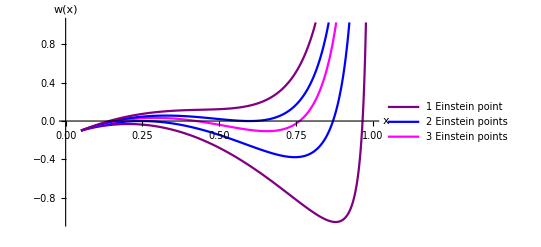

```mathematica
(*Plot w vs x for certain c values*)
(*Where w = 0 is where Einstein points exist*)
wplot=Plot[{w[x,c[[1]],cv],w[x,c[[2]],cv],w[x,c[[4]],cv],w[x,c[[6]],cv],w[x,c[[7]],cv]},{x,0,1},PlotLegends->{"1 Einstein point","2 Einstein points", "3 Einstein points"},PlotStyle->{Purple,Blue, Magenta,Blue,Purple},AxesLabel->{"x","w(x)"}]
```

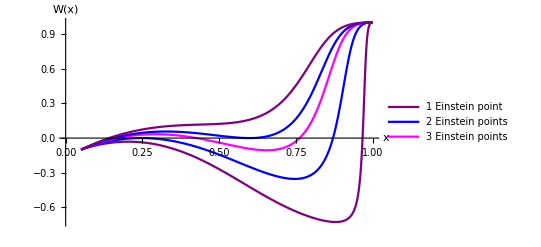

```mathematica
(*Plot compact W for certain c values*)
Wplot=Plot[{W[x,c[[1]],cv],W[x,c[[2]],cv],W[x,c[[4]],cv],W[x,c[[6]],cv],W[x,c[[7]],cv]},{x,0,1},PlotLegends->{"1 Einstein point","2 Einstein points", "3 Einstein points"},PlotStyle->{Purple,Blue, Magenta,Blue,Purple},AxesLabel->{"x","W(x)"},ImageSize->{400,400}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xY_Plots\\Wplot.pdf",Wplot]*)
```

```mathematica
(*Define zEinstein as w = 0 rearranged for z*)
zEinstein[x_]=3*R-(1+3*R)*x+3*x^2-2*v[x,cv];
```

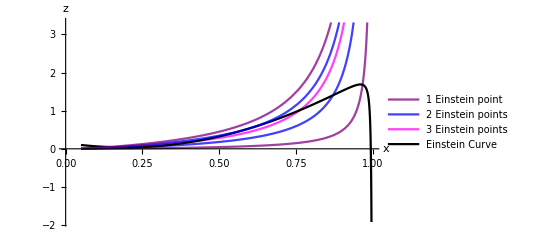

```mathematica
(*Plot of z(x) against the curves that show the number of Einstein points*)
zvsx=Plot[{z[x,c][[1]],z[x,c][[2]],z[x,c][[4]],zEinstein[x],z[x,c][[6]],z[x,c][[7]]},{x,0,1},PlotLegends->{"1 Einstein point","2 Einstein points", "3 Einstein points","Einstein Curve"},PlotStyle->{{Purple,Opacity[0.75]}, {Blue,Opacity[0.75]}, {Magenta,Opacity[0.75]},Black,{Blue,,Opacity[0.75]},{Purple,Opacity[0.75]}},AxesLabel->{"x","z"}]
```

```mathematica
(*Define ZEinstein as c omapct zEinstein*)
ZEinstein[x_]=zEinstein[x]/(1+zEinstein[x]);
```

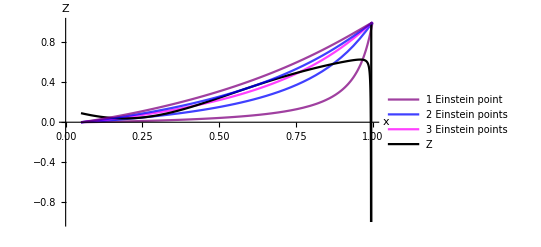

```mathematica
(*Plot of v(x) against the curves that show the number of Einstein points*)
Zvsx=Plot[{Z[x,c][[1]],Z[x,c][[2]],Z[x,c][[4]],ZEinstein[x],Z[x,c][[6]],Z[x,c][[7]]},{x,0,1},PlotLegends->{"1 Einstein point","2 Einstein points", "3 Einstein points","Z"},PlotStyle->{{Purple,Opacity[0.75]}, {Blue,Opacity[0.75]}, {Magenta,Opacity[0.75]},Black,{Blue,,Opacity[0.75]},{Purple,Opacity[0.75]}},AxesLabel->{"x","Z"}, PlotRange->{-1,1}]
```

## Calculate the Einstein Points

```mathematica
(*Numerically solve w(x) = 0 to find the x values of the Einstein fixed points in each case*)
(*FindRoot is a Newtonian approximation*)
```

### One Einstein Point: c1

```mathematica
xOneEinsteinPointc1=FindRoot[w[x,c[[1]],cv]==0,{x,0.9}];
```

```mathematica
(*Remove the arrow from the solution above*)
xOneEinsteinPointc1=x/.xOneEinsteinPointc1
```

0.967421

```mathematica
(*Calculate the Z value of the Einstein point*)
ZOneEinsteinPointc1=Z[xOneEinsteinPointc1,c[[1]]]
```

0.62664

```mathematica
(*Calculate the V value of the Einstein point*)
VOneEinsteinPointc1=V[xOneEinsteinPointc1,cv]
```

0.0769768

```mathematica
(*Put the Einstein point into one variable name*)
EinsteinFP[1]={xOneEinsteinPointc1,0,ZOneEinsteinPointc1,VOneEinsteinPointc1}
```

{0.967421,0,0.62664,0.0769768}

### Two Einstein Points: c2 (1st Limiting Case)

```mathematica
xTwoEinsteinPointsc2i=FindRoot[w[x,c[[2]],cv]==0,{x,0.1}];
xTwoEinsteinPointsc2ii=FindRoot[w[x,c[[2]],cv]==0,{x,0.9}];
```

```mathematica
(*Put the x values of the Einstein points into one variable name for this case*)
xTwoEinsteinPointsc2={x/.xTwoEinsteinPointsc2i,x/.xTwoEinsteinPointsc2ii}
```

{0.246738,0.871103}

```mathematica
(*Calculate the Z values of the Einstein points*)
ZTwoEinsteinPointsc2=Z[xTwoEinsteinPointsc2,c[[2]]]
```

{0.0463988,0.584023}

```mathematica
(*Calculate the V values of the Einstein points*)
VTwoEinsteinPointsc2=V[xTwoEinsteinPointsc2,cv]
```

{0.000117007,0.0102506}

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFP[2]={xTwoEinsteinPointsc2[[1]],0,ZTwoEinsteinPointsc2[[1]],VTwoEinsteinPointsc2[[1]]}
EinsteinFP[3]={xTwoEinsteinPointsc2[[2]],0,ZTwoEinsteinPointsc2[[2]],VTwoEinsteinPointsc2[[2]]}
```

{0.246738,0,0.0463988,0.000117007}

{0.871103,0,0.584023,0.0102506}

### Three Einstein Points: c3

```mathematica
xThreeEinsteinPointsc3i=FindRoot[w[x,c[[3]],cv]==0,{x,0.1}];
xThreeEinsteinPointsc3ii=FindRoot[w[x,c[[3]],cv]==0,{x,0.4}];
xThreeEinsteinPointsc3iii=FindRoot[w[x,c[[3]],cv]==0,{x,0.9}];
```

```mathematica
(*Put the x values of the Einstein points into one variable name for this case*)
xThreeEinsteinPointsc3={x/.xThreeEinsteinPointsc3i,x/.xThreeEinsteinPointsc3ii,x/.xThreeEinsteinPointsc3iii}
```

{0.190763,0.339647,0.8311}

```mathematica
(*Calculate the Z values of the Einstein points*)
ZThreeEinsteinPointsc3=Z[xThreeEinsteinPointsc3,c[[3]]]
```

{0.0381488,0.0950237,0.556187}

```mathematica
(*Calculate the V values of the Einstein points*)
VThreeEinsteinPointsc3=V[xThreeEinsteinPointsc3,cv]
```

{0.0000661406,0.000242189,0.00656399}

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFP[4]={xThreeEinsteinPointsc3[[1]],0,ZThreeEinsteinPointsc3[[1]],VThreeEinsteinPointsc3[[1]]}
EinsteinFP[5]={xThreeEinsteinPointsc3[[2]],0,ZThreeEinsteinPointsc3[[2]],VThreeEinsteinPointsc3[[2]]}
EinsteinFP[6]={xThreeEinsteinPointsc3[[3]],0,ZThreeEinsteinPointsc3[[3]],VThreeEinsteinPointsc3[[3]]}
```

{0.190763,0,0.0381488,0.0000661406}

{0.339647,0,0.0950237,0.000242189}

{0.8311,0,0.556187,0.00656399}

### Three Einstein Points: c4

```mathematica
xThreeEinsteinPointsc4i=FindRoot[w[x,c[[4]],cv]==0,{x,0.1}];
xThreeEinsteinPointsc4ii=FindRoot[w[x,c[[4]],cv]==0,{x,0.4}];
xThreeEinsteinPointsc4iii=FindRoot[w[x,c[[4]],cv]==0,{x,0.9}];
```

```mathematica
(*Put the x values of the Einstein points into one variable name for this case*)
xThreeEinsteinPointsc4={x/.xThreeEinsteinPointsc4i,x/.xThreeEinsteinPointsc4ii,x/.xThreeEinsteinPointsc4iii}
```

{0.169206,0.426181,0.762176}

```mathematica
(*Calculate the Z values of the Einstein points*)
ZThreeEinsteinPointsc4=Z[xThreeEinsteinPointsc4,c[[4]]]
```

{0.0395735,0.169387,0.502254}

```mathematica
(*Calculate the V values of the Einstein points*)
VThreeEinsteinPointsc4=V[xThreeEinsteinPointsc4,cv]
```

{0.0000504818,0.000425625,0.00357739}

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFP[7]={xThreeEinsteinPointsc4[[1]],0,ZThreeEinsteinPointsc4[[1]],VThreeEinsteinPointsc4[[1]]}
EinsteinFP[8]={xThreeEinsteinPointsc4[[2]],0,ZThreeEinsteinPointsc4[[2]],VThreeEinsteinPointsc4[[2]]}
EinsteinFP[9]={xThreeEinsteinPointsc4[[3]],0,ZThreeEinsteinPointsc4[[3]],VThreeEinsteinPointsc4[[3]]}
```

{0.169206,0,0.0395735,0.0000504818}

{0.426181,0,0.169387,0.000425625}

{0.762176,0,0.502254,0.00357739}

### Three Einstein Points: c5

```mathematica
xThreeEinsteinPointsc5i=FindRoot[w[x,c[[5]],cv]==0,{x,0.1}];
xThreeEinsteinPointsc5ii=FindRoot[w[x,c[[5]],cv]==0,{x,0.4}];
xThreeEinsteinPointsc5iii=FindRoot[w[x,c[[5]],cv]==0,{x,0.9}];
```

```mathematica
(*Put the x values of the Einstein points into one variable name for this case*)
xThreeEinsteinPointsc5={x/.xThreeEinsteinPointsc5i,x/.xThreeEinsteinPointsc5ii,x/.xThreeEinsteinPointsc5iii}
```

{0.162421,0.476643,0.716724}

```mathematica
(*Calculate the Z values of the Einstein points*)
ZThreeEinsteinPointsc5=Z[xThreeEinsteinPointsc5,c[[5]]]
```

{0.0405517,0.220133,0.462864}

```mathematica
(*Calculate the V values of the Einstein points*)
VThreeEinsteinPointsc5=V[xThreeEinsteinPointsc5,cv]
```

{0.0000459683,0.000577826,0.00255394}

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFP[10]={xThreeEinsteinPointsc5[[1]],0,ZThreeEinsteinPointsc5[[1]],VThreeEinsteinPointsc5[[1]]}
EinsteinFP[11]={xThreeEinsteinPointsc5[[2]],0,ZThreeEinsteinPointsc5[[2]],VThreeEinsteinPointsc5[[2]]}
EinsteinFP[12]={xThreeEinsteinPointsc5[[3]],0,ZThreeEinsteinPointsc5[[3]],VThreeEinsteinPointsc5[[3]]}
```

{0.162421,0,0.0405517,0.0000459683}

{0.476643,0,0.220133,0.000577826}

{0.716724,0,0.462864,0.00255394}

### Two Einstein Points: c6 (2nd Limiting Case)

```mathematica
xTwoEinsteinPointsc6i=FindRoot[w[x,c[[6]],cv]==0,{x,0.1}];
xTwoEinsteinPointsc6ii=FindRoot[w[x,c[[6]],cv]==0,{x,0.9}];
```

```mathematica
(*Put the x values of the Einstein points into one variable name for this case*)
xTwoEinsteinPointsc6={x/.xTwoEinsteinPointsc6i,x/.xTwoEinsteinPointsc6ii}
```

{0.156331,0.598794}

```mathematica
(*Calculate the Z values of the Einstein points*)
ZTwoEinsteinPointsc6=Z[xTwoEinsteinPointsc6,c[[6]]]
```

{0.0416437,0.348389}

```mathematica
(*Calculate the V values of the Einstein points*)
VTwoEinsteinPointsc6=V[xTwoEinsteinPointsc6,cv]
```

{0.0000420821,0.001194}

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFP[13]={xTwoEinsteinPointsc6[[1]],0,ZTwoEinsteinPointsc6[[1]],VTwoEinsteinPointsc6[[1]]}
EinsteinFP[14]={xTwoEinsteinPointsc6[[2]],0,ZTwoEinsteinPointsc6[[2]],VTwoEinsteinPointsc6[[2]]}
```

{0.156331,0,0.0416437,0.0000420821}

{0.598794,0,0.348389,0.001194}

### One Einstein Point: c7

```mathematica
xOneEinsteinPointc7=FindRoot[w[x,c[[7]],cv]==0,{x,0.1}];
```

```mathematica
(*Remove the arrow from the solution above*)
xOneEinsteinPointc7=x/.xOneEinsteinPointc7
```

0.141399

```mathematica
(*Calculate the Z value of the Einstein point*)
ZOneEinsteinPointc7=Z[xOneEinsteinPointc7,c[[7]]]
```

0.0451691

```mathematica
(*Calculate the V value of the Einstein point*)
VOneEinsteinPointc7=V[xOneEinsteinPointc7,cv]
```

0.0000332021

```mathematica
(*Put the Einstein point into one variable name*)
EinsteinFP[15]={xOneEinsteinPointc7,0,ZOneEinsteinPointc7,VOneEinsteinPointc7}
```

{0.141399,0,0.0451691,0.0000332021}

```mathematica
(*Find the eigenvalues of the Einstein fixed points*)
```

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFPs=Table[EinsteinFP[i],{i,1,15}];
```

```mathematica
(*Find the Jacobian and eigenvalues for each Einstein fixed point*)
TableForm[Table[{EinsteinFPs[[i]]//MatrixForm,Simplify[J/.{x->EinsteinFPs[[i,1]],Y->EinsteinFPs[[i,2]],Z->EinsteinFPs[[i,3]],V->EinsteinFPs[[i,4]]}]//MatrixForm,Simplify[Eigenvalues[J/.{x->EinsteinFPs[[i,1]],Y->EinsteinFPs[[i,2]],Z->EinsteinFPs[[i,3]],V->EinsteinFPs[[i,4]]}]]//MatrixForm},{i,1,15}],TableHeadings->{{"c1","c2","","c3","","","c4","","","c5","","","c6","","c7"},{"Einstein Fixed Point", "Jacobian","Eigenvalues"}}]
```

| Einstein Fixed Point | Jacobian | Eigenvalues
c1 | (0.967421
0
0.62664
0.0769768) | (0. | -0.0896672 | 0 | 0
0.775754 | 0. | -1.19562 | -0.391249
0 | -0.701887 | 0. | 0
0 | -0.284205 | 0 | 0.) | (0.938523
-0.938523
7.96254×10^-17
0.)
c2 | (0.246738
0
0.0463988
0.000117007) | (0. | -0.444587 | 0 | 0
0.0550718 | 0. | -0.18328 | -0.333411
0 | -0.132738 | 0. | 0
0 | -0.000467972 | 0 | 0.) | (-0.00005637
0.0000563699
1.33882×10^-10
0.)
 | (0.871103
0
0.584023
0.0102506) | (0. | -0.317514 | 0 | 0
0.679436 | 0. | -0.963185 | -0.340274
0 | -0.728821 | 0. | 0
0 | -0.040582 | 0 | 0.) | (0.707154
-0.707154
5.36455×10^-17
0.)
c3 | (0.190763
0
0.0381488
0.0000661406) | (0. | -0.341731 | 0 | 0
-0.000904133 | 0. | -0.180149 | -0.333377
0 | -0.11008 | 0. | 0
0 | -0.000264545 | 0 | 0.) | (-0.142225
0.142225
8.12045×10^-18
0.)
 | (0.339647
0
0.0950237
0.000242189) | (0. | -0.573807 | 0 | 0
0.14798 | 0. | -0.203505 | -0.333495
0 | -0.257982 | 0. | 0
0 | -0.00096852 | 0 | 0.) | (-6.01468×10^-17+0.179132 ⅈ
-6.01468×10^-17-0.179132 ⅈ
1.03856×10^-16+0. ⅈ
0.+0. ⅈ)
 | (0.8311
0
0.556187
0.00656399) | (0. | -0.395783 | 0 | 0
0.639433 | 0. | -0.846153 | -0.337753
0 | -0.740529 | 0. | 0
0 | -0.0260836 | 0 | 0.) | (0.618331
-0.618331
-6.67169×10^-17
0.)
c4 | (0.169206
0
0.0395735
0.0000504818) | (0. | -0.297108 | 0 | 0
-0.0224602 | 0. | -0.180684 | -0.333367
0 | -0.114022 | 0. | 0
0 | -0.000201917 | 0 | 0.) | (-0.165356
0.165356
-8.58732×10^-20
0.)
 | (0.426181
0
0.169387
0.000425625) | (0. | -0.647579 | 0 | 0
0.234514 | 0. | -0.241575 | -0.333617
0 | -0.422085 | 0. | 0
0 | -0.00170178 | 0 | 0.) | (5.5299×10^-17+0.222111 ⅈ
5.5299×10^-17-0.222111 ⅈ
-8.82802×10^-18+0. ⅈ
0.+0. ⅈ)
 | (0.762176
0
0.502254
0.00357739) | (0. | -0.508117 | 0 | 0
0.57051 | 0. | -0.672717 | -0.335731
0 | -0.749985 | 0. | 0
0 | -0.0142584 | 0 | 0.) | (0.468432
-0.468432
1.05611×10^-17
0.)
c5 | (0.162421
0
0.0405517
0.0000459683) | (0. | -0.282485 | 0 | 0
-0.0292454 | 0. | -0.181053 | -0.333364
0 | -0.116722 | 0. | 0
0 | -0.000183865 | 0 | 0.) | (-0.171626
0.171626
2.48758×10^-18
0.)
 | (0.476643
0
0.220133
0.000577826) | (0. | -0.66986 | 0 | 0
0.284976 | 0. | -0.274036 | -0.333719
0 | -0.515023 | 0. | 0
0 | -0.00230997 | 0 | 0.) | (1.25475×10^-16+0.221333 ⅈ
1.25475×10^-16-0.221333 ⅈ
4.86337×10^-17+0. ⅈ
0.+0. ⅈ)
 | (0.716724
0
0.462864
0.00255394) | (0. | -0.566601 | 0 | 0
0.525057 | 0. | -0.577671 | -0.335043
0 | -0.745863 | 0. | 0
0 | -0.0101897 | 0 | 0.) | (0.369837
-0.369837
-2.60869×10^-16
0.)
c6 | (0.156331
0
0.0416437
0.0000420821) | (0. | -0.269126 | 0 | 0
-0.0353352 | 0. | -0.181466 | -0.333361
0 | -0.119728 | 0. | 0
0 | -0.000168322 | 0 | 0.) | (0.176896
-0.176896
1.49757×10^-18
0.)
 | (0.598794
0
0.348389
0.001194) | (0. | -0.660538 | 0 | 0
0.407127 | 0. | -0.392529 | -0.334131
0 | -0.681043 | 0. | 0
0 | -0.00477029 | 0 | 0.) | (-0.000100137
0.000100136
1.23469×10^-9
0.)
c7 | (0.141399
0
0.0451691
0.0000332021) | (0. | -0.235425 | 0 | 0
-0.0502681 | 0. | -0.182808 | -0.333355
0 | -0.129387 | 0. | 0
0 | -0.000132804 | 0 | 0.) | (-0.188498
0.188498
9.76266×10^-18
0.)

## Submanifolds

## Set-up

### Submanifolds

```mathematica
(*Define the scale factor (a) in terms of x*)
(*ca is the integration constant of a(x)*)
ca[x0_]=(1-x0)/(x0-R);
a[x_,x0_]=(ca[x0]*((x-R)/(1-x)))^((-1)/(3*(1-R)));
```

```mathematica
(*Define compact radiation (V) and the scale factor (a) in terms of compact dark matter (Z)*)
vz[z_,cz_]=cz*z^(4/3);
Vz[Z_,cz_]=vz[Z/(1-Z),cz]/(1+vz[Z/(1-Z),cz]);

az[Z_,Z0_]=(((1-Z)/Z)(Z0/(1-Z0)))^(1/3);
```

```mathematica
(*Define compact dark matter (Z) and the scale factor (a) in terms of compact radiation (V)*)
zv[v_,cz_]=(v/cz)^(3/4);
Zv[v_,cz_]=zv[V/(1-V),cz]/(1+zv[V/(1-V),cz]);

av[V_,V0_]=(((1-V)/V)(V0/(1-V0)))^(1/4);
```

```mathematica
(*Calculate cz*)
(*Rearrange z for cz*)
cz=cz/.Simplify[Solve[z0==zv[v0,cz],cz][[1]]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

v0/z0^(4/3)

```mathematica
(*Define z0*)
z0=ρ0/ρc;
```

```mathematica
(*Calculate ρ0*)
ρ0=3*H0^2*Ωm
```

4272.53

```mathematica
(*Define v0*)
v0=ρr0/ρc
```

0.0000133291

```mathematica
(*Calculate ρr0*)
ρr0=3*H0^2*Ωr
```

1.26108

```mathematica
(*Value of cz*)
cz =cz
```

0.000828849

```mathematica
(*Clear z0 and v0*)
Clear[z0,v0]
```

```mathematica
(*Define w, the the RHS of y', for the submanifolds*)
wSubMan[x_,z_,v_]=-(1/6)*(z+2v-3*R+x*(1+3*R)-3*x^2);
```

```mathematica
(*Define the Flat Friedmann Separatrix for the submanifolds*)
(*Define ffs = Y^2/(1-Y^2)*)
ffsSubMan[x_,Z_,V_]=x/3+Z/(3*(1-Z))+V/(3*(1-V));
```

```mathematica
(*Rearrange the above for Y*)
FFSSubMan[x_,Z_,V_]=Sqrt[ffsSubMan[x,Z,V]/(1+ffsSubMan[x,Z,V])];
```

```mathematica
(*Define the Closed Friedmann Separatrix (CFS) for the submanifolds in terms of x*)
(*Define cfs = Y^2/(1-Y^2)*)
cfsSubManx[x_,x0_,Z_,Z0_,V_,V0_]= x/3+Z/(3*(1-Z))+V/(3*(1-V))-(1/a[x,x0]^2)*(x0/3+Z0/(3*(1-Z0))+V0/(3*(1-V0)));
```

```mathematica
(*Rearrange above equation for Y*)
CFSSubManx[x_,x0_,Z_,Z0_,V_,V0_]=Sqrt[cfsSubManx[x,x0,Z,Z0,V,V0]/(1+cfsSubManx[x,x0,Z,Z0,V,V0])];
```

```mathematica
(*Define the Closed Friedmann Separatrix (CFS) in terms of Z*)
(*Define cfs = Y^2/(1-Y^2)*)
cfsSubManZ[x_,x0_,Z_,Z0_,V_,V0_]= x/3+Z/(3*(1-Z))+V/(3*(1-V))-(1/az[Z,Z0]^2)*(x0/3+Z0/(3*(1-Z0))+V0/(3*(1-V0)));
```

```mathematica
(*Rearrange above equation for Y*)
CFSSubManZ[x_,x0_,Z_,Z0_,V_,V0_]=Sqrt[cfsSubManZ[x,x0,Z,Z0,V,V0]/(1+cfsSubManZ[x,x0,Z,Z0,V,V0])];
```

```mathematica
(*Define the Closed Friedmann Separatrix (CFS) in terms of V*)
(*Define cfs = Y^2/(1-Y^2)*)
cfsSubManV[x_,x0_,Z_,Z0_,V_,V0_]= x/3+Z/(3*(1-Z))+V/(3*(1-V))-(1/av[V,V0]^2)*(x0/3+Z0/(3*(1-Z0))+V0/(3*(1-V0)));
```

```mathematica
(*Rearrange above equation for Y*)
CFSSubManV[x_,x0_,Z_,Z0_,V_,V0_]=Sqrt[cfsSubManV[x,x0,Z,Z0,V,V0]/(1+cfsSubManV[x,x0,Z,Z0,V,V0])];
```

```mathematica
(*Set up plot for x = R and x = 1 separatrices*)
Sepx=ContourPlot[{x==R,x==1},{x,0,1.1},{Y,-1,1},ContourStyle->{Black},PlotRange->Full];
```

```mathematica
(*Set up plot of the cv surface in terms of x and the cz surface in terms of Z*)
Surfacecv=ParametricPlot3D[{x,Y,V[x,cv]},{x,0,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
Surfacecz=ParametricPlot3D[{Z,Y,Vz[Z,cz]},{Z,0,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
```

### Potentials

```mathematica
(*Define the potential in terms of a, x, Z and V*)
USubMan[a_,x_,Z_,V_]=-a^2*(x/6+Z/(6*(1-Z))+V/(6*(1-V)));
```

## Qualitative ΛCDM Dynamics

```mathematica
(*These cases have the same qualitiative dynamics as ΛCDM, except here the Λs are asymptotic values*)
```

### x = R, V = 0

```mathematica
(*Trajectories for the phase space*)
trajxRV0[Y0_,Z0_]:=Y^2/(1-Y^2)==R/3+Z/(3*(1-Z))-(1/az[Z,Z0]^2)*(R/3+Z0/(3*(1-Z0))-Y0^2/(1-Y0^2));
```

```mathematica
xRV0traj[1]=ContourPlot[Evaluate[trajxRV0[0,0.03]],{Z,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
xRV0traj[2]=ContourPlot[Evaluate[trajxRV0[0,0.03]],{Z,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xRV0traj[3]=ContourPlot[Evaluate[trajxRV0[0,0.6]],{Z,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xRV0traj[4]=ContourPlot[Evaluate[trajxRV0[0,0.9]],{Z,0.6,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xRV0traj[5]=ContourPlot[Evaluate[trajxRV0[0.4,0.45]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xRV0traj[6]=ContourPlot[Evaluate[trajxRV0[0.4,0.45]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xRV0traj[7]=ContourPlot[Evaluate[trajxRV0[0.9,0.3]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xRV0traj[8]=ContourPlot[Evaluate[trajxRV0[0.9,0.3]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xRV0traj[9]=ContourPlot[Evaluate[trajxRV0[0.75,0.5]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xRV0traj[10]=ContourPlot[Evaluate[trajxRV0[0.75,0.5]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
TrajxRV0=Table[xRV0traj[i],{i,1,10}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSxRV0=Plot[{FFSSubMan[R,Z,0],-FFSSubMan[R,Z,0]},{Z,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSxRV0=Plot[{{CFSSubManZ[R,R,Z,2*R/(1+2*R),0,0]},{-CFSSubManZ[R,R,Z,2*R/(1+2*R),0,0]}},{Z,0,1},PlotStyle->Black];
```

```mathematica
(*Plot the fixed points*)
FPShowxRV0=ListPlot[{{0,1},{0,-1},{1,1},{1,-1},{0,Sqrt[R/(3+R)]},{0,-Sqrt[R/(3+R)]},{2*R/(1+2*R),0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

```mathematica
(*Plot the two invariant manifolds*)
SepxRV0=Plot[{-1,1},{Z,0,1},PlotStyle->Black];
```

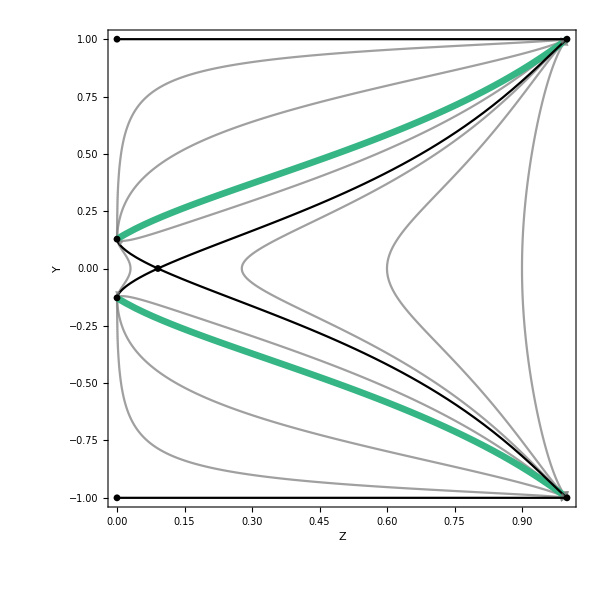

```mathematica
xRV0SubMan=Show[TrajxRV0,FFSxRV0,CFSxRV0,FPShowxRV0,SepxRV0,FrameLabel->{"Z",Rotate["Y",300]},PlotRange->{{0,1},{-1,1}},ImageSize->{600,600}]
```

```mathematica
av[V,V0]
```

(((1-V) V0)/(V (1-V0)))^(1/4)

### x = R, Z = 0

```mathematica
(*Trajectories for the phase space*)
trajxRZ0[Y0_,V0_]:=Y^2/(1-Y^2)==R/3+V/(3*(1-V))-(1/(av[V,V0]^2))*(R/3+V0/(3*(1-V0))-Y0^2/(1-Y0^2));
```

```mathematica
xRZ0traj[1]=ContourPlot[Evaluate[trajxRZ0[0,0.01]],{V,0,0.1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
xRZ0traj[2]=ContourPlot[Evaluate[trajxRZ0[0,0.01]],{V,0.1,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xRZ0traj[3]=ContourPlot[Evaluate[trajxRZ0[0,0.6]],{V,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xRZ0traj[4]=ContourPlot[Evaluate[trajxRZ0[0,0.9]],{V,0.6,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xRZ0traj[5]=ContourPlot[Evaluate[trajxRZ0[0.4,0.45]],{V,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xRZ0traj[6]=ContourPlot[Evaluate[trajxRZ0[0.4,0.45]],{V,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xRZ0traj[7]=ContourPlot[Evaluate[trajxRZ0[0.9,0.3]],{V,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xRZ0traj[8]=ContourPlot[Evaluate[trajxRZ0[0.9,0.3]],{V,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xRZ0traj[9]=ContourPlot[Evaluate[trajxRZ0[0.75,0.5]],{V,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xRZ0traj[10]=ContourPlot[Evaluate[trajxRZ0[0.75,0.5]],{V,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
TrajxRZ0=Table[xRZ0traj[i],{i,1,10}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSxRZ0=Plot[{FFSSubMan[R,0,V],-FFSSubMan[R,0,V]},{V,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSxRZ0=Plot[{{CFSSubManV[R,R,0,0,V,R/(1+R)]},{-CFSSubManV[R,R,0,0,V,R/(1+R)]}},{V,0,1},PlotStyle->Black,PlotPoints->500];
```

```mathematica
(*Plot the fixed points*)
FPShowxRZ0=ListPlot[{{0,1},{0,-1},{1,1},{1,-1},{0,Sqrt[R/(3+R)]},{0,-Sqrt[R/(3+R)]},{R/(1+R),0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

```mathematica
(*Plot the two invariant manifolds*)
SepxRZ0=Plot[{-1,1},{V,0,1},PlotStyle->Black];
```

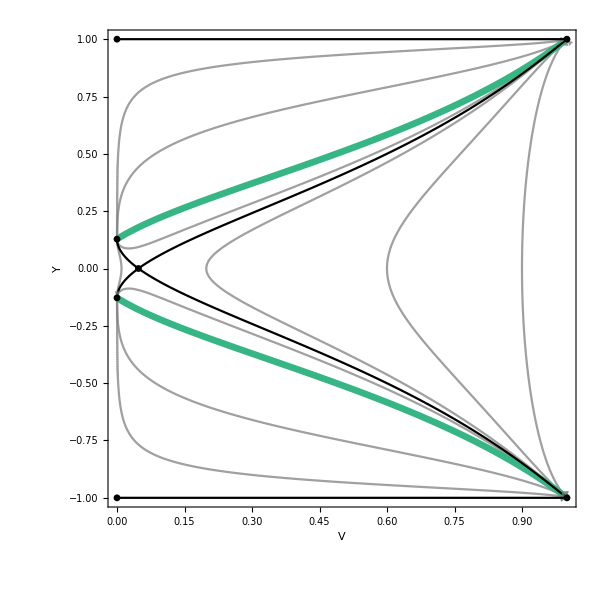

```mathematica
xRZ0SubMan=Show[TrajxRZ0,FFSxRZ0,CFSxRZ0,FPShowxRZ0,SepxRZ0,FrameLabel->{"V",Rotate["Y",300]},PlotRange->{{0,1},{-1,1}},ImageSize->{600,600}]
```

### x = R

### Y = 0 fixed points

```mathematica
(*Solve for Z when Y = 0*)
xRY0=Solve[wSubMan[R,Z/(1-Z),Vz[Z,cz]/(1-Vz[Z,cz])]==0,Z]
```

{{Z→0.0908456}}

```mathematica
(*Remove arrow and de-nest solution*)
xRY0=Z/.xRY0[[1]]
```

0.0908456

### Plot the Submanifold

```mathematica
(*Trajectories for the phase space*)
traj3DxR[Y0_,Z0_]=R/3+Z/(3*(1-Z))+Vz[Z,cz]/(3*(1-Vz[Z,cz]))-(1/az[Z,Z0]^2)*(R/3+Z0/(3*(1-Z0))+Vz[Z0,cz]/(3*(1-Vz[Z0,cz]))-Y0^2/(1-Y0^2));
```

```mathematica
(*Rearrange above equation for Y*)
traj3DxR[Y0_,Z0_]=Sqrt[traj3DxR[Y0,Z0]/(1+traj3DxR[Y0,Z0])];
```

```mathematica
xRtraj3D[1]=ParametricPlot3D[{Z,traj3DxR[0,0.03],Vz[Z,cz]},{Z,0,xRY0},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[2]=ParametricPlot3D[{Z,-traj3DxR[0,0.03],Vz[Z,cz]},{Z,0,xRY0},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
xRtraj3D[3]=ParametricPlot3D[{Z,traj3DxR[0,0.03],Vz[Z,cz]},{Z,xRY0,1},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[4]=ParametricPlot3D[{Z,-traj3DxR[0,0.03],Vz[Z,cz]},{Z,xRY0,1},PlotPoints->200,PlotRange->All,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[5]=ParametricPlot3D[{Z,traj3DxR[0,0.6],Vz[Z,cz]},{Z,0,xRY0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[6]=ParametricPlot3D[{Z,-traj3DxR[0,0.6],Vz[Z,cz]},{Z,0,xRY0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
xRtraj3D[7]=ParametricPlot3D[{Z,traj3DxR[0,0.6],Vz[Z,cz]},{Z,xRY0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[8]=ParametricPlot3D[{Z,-traj3DxR[0,0.6],Vz[Z,cz]},{Z,xRY0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[9]=ParametricPlot3D[{Z,traj3DxR[0,0.9],Vz[Z,cz]},{Z,0,xRY0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[10]=ParametricPlot3D[{Z,-traj3DxR[0,0.9],Vz[Z,cz]},{Z,0,xRY0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
xRtraj3D[11]=ParametricPlot3D[{Z,traj3DxR[0,0.9],Vz[Z,cz]},{Z,xRY0,1},PlotPoints->2000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[12]=ParametricPlot3D[{Z,-traj3DxR[0,0.9],Vz[Z,cz]},{Z,xRY0,1},PlotPoints->2000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[13]=ParametricPlot3D[{Z,traj3DxR[0.4,0.45],Vz[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[14]=ParametricPlot3D[{Z,-traj3DxR[0.4,0.45],Vz[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[15]=ParametricPlot3D[{Z,traj3DxR[0.9,0.3],Vz[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[16]=ParametricPlot3D[{Z,-traj3DxR[0.9,0.3],Vz[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[17]=ParametricPlot3D[{Z,traj3DxR[0.75,0.5],Vz[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[18]=ParametricPlot3D[{Z,-traj3DxR[0.75,0.5],Vz[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Traj3DxR=Table[xRtraj3D[i],{i,1,18}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFS3DxR=ParametricPlot3D[{{Z,FFSSubMan[R,Z/(1-Z),Vz[Z,cz]],Vz[Z,cz]},{Z,-FFSSubMan[R,Z/(1-Z),Vz[Z,cz]],Vz[Z,cz]}},{Z,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFS3DxR=ParametricPlot3D[{{Z,CFSSubManZ[R,R,Z,xRY0,Vz[Z,cz],Vz[xRY0,cz]],Vz[Z,cz]},{Z,-CFSSubManZ[R,R,Z,xRY0,Vz[Z,cz],Vz[xRY0,cz]],Vz[Z,cz]}},{Z,0,1},PlotStyle->Black];
```

```mathematica
(*Plot the fixed points*)
FPShow3DxR=ListPointPlot3D[{{0,1,0},{0,-1,0},{1,1,1},{1,-1,1},{0,Sqrt[R/(3+R)],0},{0,-Sqrt[R/(3+R)],0},{xRY0,0,Vz[xRY0,cz]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
xRSubMan3D=Show[Traj3DxR,FFS3DxR,CFS3DxR,FPShow3DxR,Surfacecz,AxesLabel->{"Z","Y","V"},PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\xRSubMan3D.pdf",xRSubMan3D]*)
```

### x = 1, V = 0

```mathematica
(*Trajectories for the phase space*)
trajx1V0[Y0_,Z0_]:=Y^2/(1-Y^2)==1/3+Z/(3*(1-Z))-(1/az[Z,Z0]^2)*(1/3+Z0/(3*(1-Z0))-Y0^2/(1-Y0^2));
```

```mathematica
x1V0traj[1]=ContourPlot[Evaluate[trajx1V0[0,0.1]],{Z,0,2/3},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1V0traj[2]=ContourPlot[Evaluate[trajx1V0[0,0.1]],{Z,2/3,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
x1V0traj[3]=ContourPlot[Evaluate[trajx1V0[0,0.25]],{Z,0,2/3},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1V0traj[4]=ContourPlot[Evaluate[trajx1V0[0,0.25]],{Z,2/3,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1V0traj[5]=ContourPlot[Evaluate[trajx1V0[0,0.4]],{Z,0,2/3},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
x1V0traj[6]=ContourPlot[Evaluate[trajx1V0[0,0.4]],{Z,2/3,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1V0traj[7]=ContourPlot[Evaluate[trajx1V0[0.25,0.55]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1V0traj[8]=ContourPlot[Evaluate[trajx1V0[0.25,0.55]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1V0traj[9]=ContourPlot[Evaluate[trajx1V0[0.5,0.3]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1V0traj[10]=ContourPlot[Evaluate[trajx1V0[0.5,0.3]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1V0traj[11]=ContourPlot[Evaluate[trajx1V0[0.9,0.3]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1V0traj[12]=ContourPlot[Evaluate[trajx1V0[0.9,0.3]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajx1V0=Table[x1V0traj[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSx1V0=Plot[{FFSSubMan[1,Z,0],-FFSSubMan[1,Z,0]},{Z,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSx1V0=Plot[{CFSSubManZ[1,1,Z,2/3,0,0],-CFSSubManZ[1,1,Z,2/3,0,0]},{Z,0,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points*)
FPShowx1V0=ListPlot[{{0,1},{0,-1},{1,1},{1,-1},{0,1/2},{0,-1/2}, {2/3,0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

```mathematica
(*Plot the two invariant manifolds*)
Sepx1V0=Plot[{-1,1},{Z,0,1},PlotStyle->Black];
```

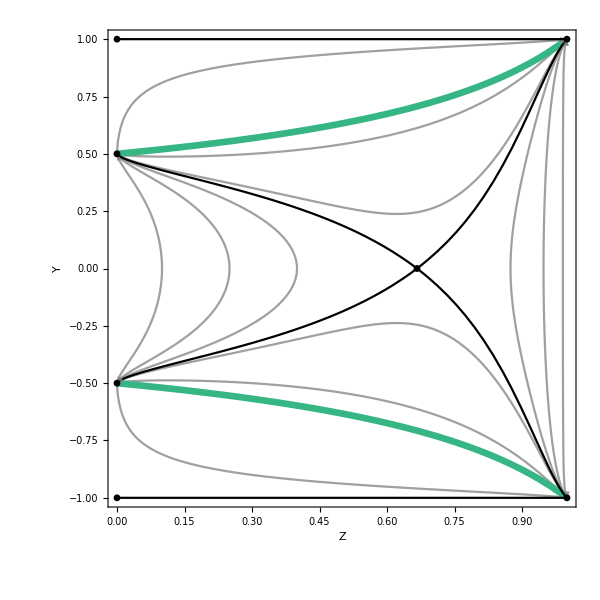

```mathematica
x1V0SubMan=Show[Trajx1V0,FFSx1V0,CFSx1V0,FPShowx1V0,Sepx1V0,FrameLabel->{"Z",Rotate["Y",300]},PlotRange->{{0,1},{-1,1}},ImageSize->{600,600}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\x1SubMan.pdf",x1SubMan]*)
```

### x = 1, Z = 0

```mathematica
(*Trajectories for the phase space*)
trajx1Z0[Y0_,V0_]:=Y^2/(1-Y^2)==1/3+V/(3*(1-V))-(1/av[V,V0]^2)*(1/3+V0/(3*(1-V0))-Y0^2/(1-Y0^2));
```

```mathematica
x1Z0traj[1]=ContourPlot[Evaluate[trajx1Z0[0,0.1]],{V,0,1/2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[2]=ContourPlot[Evaluate[trajx1Z0[0,0.1]],{V,1/2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[3]=ContourPlot[Evaluate[trajx1Z0[0,0.25]],{V,0,1/2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[4]=ContourPlot[Evaluate[trajx1Z0[0,0.25]],{V,1/2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[5]=ContourPlot[Evaluate[trajx1Z0[0,0.4]],{V,0,1/2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[6]=ContourPlot[Evaluate[trajx1Z0[0,0.4]],{V,1/2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[7]=ContourPlot[Evaluate[trajx1Z0[0.25,0.55]],{V,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[8]=ContourPlot[Evaluate[trajx1Z0[0.25,0.55]],{V,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[9]=ContourPlot[Evaluate[trajx1Z0[0.5,0.3]],{V,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[10]=ContourPlot[Evaluate[trajx1Z0[0.5,0.3]],{V,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[11]=ContourPlot[Evaluate[trajx1Z0[0.9,0.3]],{V,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[12]=ContourPlot[Evaluate[trajx1Z0[0.9,0.3]],{V,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajx1Z0=Table[x1Z0traj[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSx1Z0=Plot[{FFSSubMan[1,0,V],-FFSSubMan[1,0,V]},{V,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSx1Z0=Plot[{CFSSubManV[1,1,0,0,V,1/2],-CFSSubManV[1,1,0,0,V,1/2]},{V,0,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points*)
FPShowx1Z0=ListPlot[{{0,1},{0,-1},{1,1},{1,-1},{0,1/2},{0,-1/2}, {1/2,0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

```mathematica
(*Plot the two invariant manifolds*)
Sepx1Z0=Plot[{-1,1},{V,0,1},PlotStyle->Black];
```

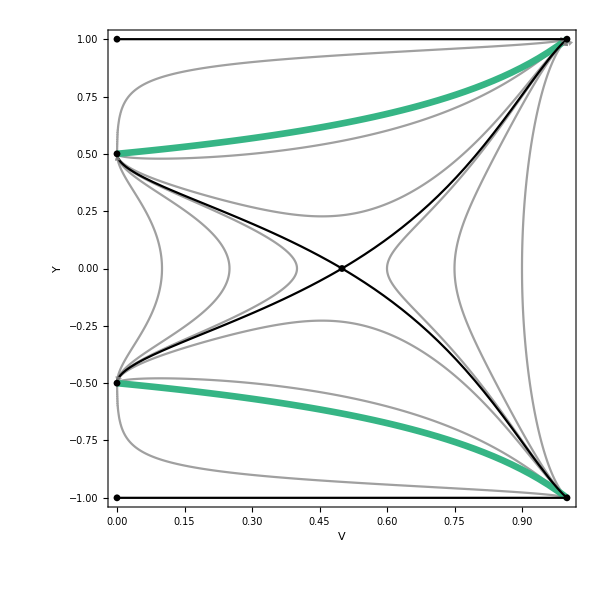

```mathematica
x1Z0SubMan=Show[Trajx1Z0,FFSx1Z0,CFSx1Z0,FPShowx1Z0,Sepx1Z0,FrameLabel->{"V",Rotate["Y",300]},PlotRange->{{0,1},{-1,1}},ImageSize->{600,600}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\x1SubMan.pdf",x1SubMan]*)
```

### x = 1

## Dynamic Dark Energy

```mathematica
(*These cases have a dynamical dark energy component*)
```

### Z = 0, V = 0

### V = 0

### Z = 0

## General Case

```mathematica
(*This is the most general case, where all components are present*)
```

## z = 0 Submanifold

### Find the Y = 0 fixed points

```mathematica
zY0=FindRoot[wSubMan[x,0,v[x,cv]]==0,{x,0.99}];
```

```mathematica
zY0=x/.zY0
```

0.994231

### Plot the 3D Submanifold

```mathematica
(*Trajectories for the phase space*)
traj3Dz[Y0_,x0_]:=x/3+v[x,cv]/3-(1/a[x,x0]^2)*(x0/3+v[x0,cv]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Rearrange above equation for Y*)
traj3Dz[Y0_,x0_]=Sqrt[traj3Dz[Y0,x0]/(1+traj3Dz[Y0,x0])];
```

```mathematica
ztraj3D[1]=ParametricPlot3D[{x,traj3Dz[0,0.3],V[x,cv]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj3D[2]=ParametricPlot3D[{x,-traj3Dz[0,0.3],V[x,cv]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj3D[3]=ParametricPlot3D[{x,traj3Dz[0,0.5],V[x,cv]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj3D[4]=ParametricPlot3D[{x,-traj3Dz[0,0.5],V[x,cv]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj3D[5]=ParametricPlot3D[{x,traj3Dz[0,0.7],V[x,cv]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj3D[6]=ParametricPlot3D[{x,-traj3Dz[0,0.7],V[x,cv]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj3D[7]=ParametricPlot3D[{x,traj3Dz[0,0.99],V[x,cv]},{x,0,1},PlotPoints->1000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj3D[8]=ParametricPlot3D[{x,-traj3Dz[0,0.99],V[x,cv]},{x,0,1},PlotPoints->1000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj3D[9]=ParametricPlot3D[{x,traj3Dz[0.4,0.2],V[x,cv]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj3D[10]=ParametricPlot3D[{x,-traj3Dz[0.4,0.2],V[x,cv]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj3D[11]=ParametricPlot3D[{x,traj3Dz[0.9,0.3],V[x,cv]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj3D[12]=ParametricPlot3D[{x,-traj3Dz[0.9,0.3],V[x,cv]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj3D[13]=ParametricPlot3D[{x,traj3Dz[0.4,0.99],V[x,cv]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj3D[14]=ParametricPlot3D[{x,-traj3Dz[0.4,0.99],V[x,cv]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Traj3Dz=Table[ztraj3D[i],{i,1,14}];
```

```mathematica
(*Flat Friedmann Separatrix*)
(*Two plots needed as sqrt taken for Y part, so + and - parts need plotting separately*)
FFS3Dz=ParametricPlot3D[{{x,FFSSubMan[x,0,v[x,cv]],V[x,cv]},{x,-FFSSubMan[x,0,v[x,cv]],V[x,cv]}},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFS3Dz=ParametricPlot3D[{{x,CFSSubManx[x,zY0,0,0,v[x,cv],v[zY0,cv]],V[x,cv]},{x,-CFSSubManx[x,zY0,0,0,v[x,cv],v[zY0,cv]],V[x,cv]}},{x,0,1},PlotStyle->{{Black}},PlotRange->All];
```

```mathematica
(*Plot the fixed points*)
FPShow3Dz = ListPointPlot3D[{{R,Sqrt[R/(3+R)],0},{R,-Sqrt[R/(3+R)],0},{1,1,1},{1,-1,1},{R,1,0},{R,-1,0},{zY0,0,V[zY0,cv]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
zSubMan3D=Show[Traj3Dz,FFS3Dz,CFS3Dz,FPShow3Dz,Surfacecv,AxesLabel->{"x","Y","V"},ImageSize->{600,400},PlotRange->{{0,1},{-1,1},{0,1}}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\zSubMan3D.pdf",zSubMan3D]*)
```

### Plot the Projected x-Y Submanifold

```mathematica
(*Trajectories for the phase space*)
trajz[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+v[x,cv]/3-(1/a[x,x0]^2)*(x0/3+v[x0,cv]/3-Y0^2/(1-Y0^2));
```

```mathematica
ztraj[1]=ContourPlot[Evaluate[trajz[0,0.1]],{x,0,0.95},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj[2]=ContourPlot[Evaluate[trajz[0,0.3]],{x,0,0.95},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj[3]=ContourPlot[Evaluate[trajz[0,0.5]],{x,0,0.95},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj[4]=ContourPlot[Evaluate[trajz[0,0.7]],{x,0,0.95},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj[5]=ContourPlot[Evaluate[trajz[0,0.9]],{x,0,0.95},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj[6]=ContourPlot[Evaluate[trajz[0.4,0.2]],{x,0,1},{Y,0.1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj[7]=ContourPlot[Evaluate[trajz[0.4,0.2]],{x,0,1},{Y,-1,-0.1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj[8]=ContourPlot[Evaluate[trajz[0.9,0.3]],{x,0,1},{Y,0.1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj[9]=ContourPlot[Evaluate[trajz[0.9,0.3]],{x,0,1},{Y,-1,-0.1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj[10]=ContourPlot[Evaluate[trajz[0.4,0.99]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj[11]=ContourPlot[Evaluate[trajz[0.4,0.99]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajz=Table[ztraj[i],{i,1,11}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSz=Plot[{FFSSubMan[x,0,v[x,cv]],-FFSSubMan[x,0,v[x,cv]]},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotPoints->200];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSz=Plot[{{CFSSubManx[x,zY0,0,0,v[x,cv],v[zY0,cv]]},{-CFSSubManx[x,zY0,0,0,v[x,cv],v[zY0,cv]]}},{x,0,1},PlotStyle->Black];
```

```mathematica
(*Plot the fixed points*)
FPShowz = ListPlot[{{1,1},{1,-1},{R,1},{R,-1}, {R,Sqrt[R/(3+R)]},{R,-Sqrt[R/(3+R)]},{zY0,0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

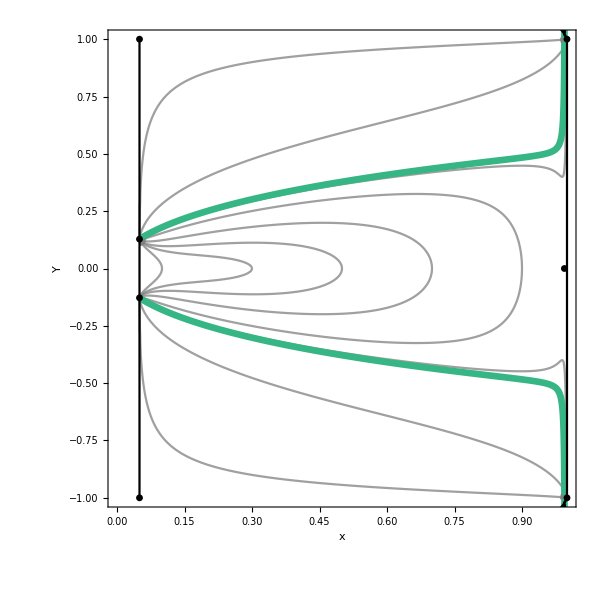

```mathematica
zSubMan=Show[Trajz,FFSz,CFSz,FPShowz,Sepx,FrameLabel->{"x",Rotate["Y",300]},ImageSize->{600,600},PlotRange->{{0,1},{-1,1}}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\zSubMan.pdf",zSubMan]*)
```

### Potential

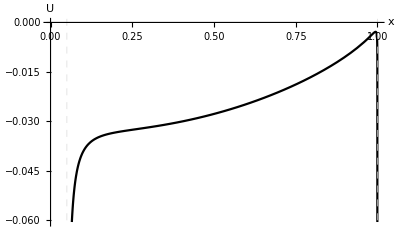

```mathematica
(*Plot the potential for this case*)
Uz0=Plot[{USubMan[a[x,0.2],x,0,V[x,cv]]},{x,0,1},AxesLabel->{"x","U"},PlotStyle->{Black},GridLines->{{.05,1},{}},GridLinesStyle->Directive[Thick,Dashed]]
```

## v = 0 Submanifold

### Find the Y = 0 fixed points

```mathematica
(*Plot the c1, c4 and c7 surfaces for the v = 0 submanifold*)
```

```mathematica
vY0c1=FindRoot[wSubMan[x,z[x,c[[1]]],0]==0,{x,0.9}];
```

```mathematica
vY0c1=x/.vY0c1[[1]]
```

0.970338

```mathematica
vY0c7=FindRoot[wSubMan[x,z[x,c[[7]]],0]==0,{x,0.9}];
```

```mathematica
vY0c7=x/.vY0c7[[1]]
```

0.141472

### Plot the 3D Submanifold

```mathematica
(*Trajectories for the phase space*)
traj3Dv[Y0_,x0_]:=x/3+z[x,c]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Rearrange above equation for Y*)
traj3Dv[Y0_,x0_]=Sqrt[traj3Dv[Y0,x0]/(1+traj3Dv[Y0,x0])];
```

```mathematica
vtraj3D[1]=ParametricPlot3D[{x,traj3Dv[0,0.3][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->35000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[2]=ParametricPlot3D[{x,-traj3Dv[0,0.3][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->35000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[3]=ParametricPlot3D[{x,traj3Dv[0,0.5][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->35000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[4]=ParametricPlot3D[{x,-traj3Dv[0,0.5][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->35000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[5]=ParametricPlot3D[{x,traj3Dv[0,0.7][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->35000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[6]=ParametricPlot3D[{x,-traj3Dv[0,0.7][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->35000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[7]=ParametricPlot3D[{x,traj3Dv[0,0.9][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->35000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[8]=ParametricPlot3D[{x,-traj3Dv[0,0.9][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->35000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[9]=ParametricPlot3D[{x,traj3Dv[0.4,0.2][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[10]=ParametricPlot3D[{x,-traj3Dv[0.4,0.2][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[11]=ParametricPlot3D[{x,traj3Dv[0.9,0.3][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[12]=ParametricPlot3D[{x,-traj3Dv[0.9,0.3][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[13]=ParametricPlot3D[{x,traj3Dv[0.4,0.9][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[14]=ParametricPlot3D[{x,-traj3Dv[0.4,0.9][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[15]=ParametricPlot3D[{x,traj3Dv[0,0.3][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->35000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[16]=ParametricPlot3D[{x,-traj3Dv[0,0.3][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->35000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[17]=ParametricPlot3D[{x,traj3Dv[0,0.5][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->35000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[18]=ParametricPlot3D[{x,-traj3Dv[0,0.5][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->35000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[19]=ParametricPlot3D[{x,traj3Dv[0,0.7][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->35000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[20]=ParametricPlot3D[{x,-traj3Dv[0,0.7][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->35000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[21]=ParametricPlot3D[{x,traj3Dv[0,0.9][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->35000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[22]=ParametricPlot3D[{x,-traj3Dv[0,0.9][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->35000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[23]=ParametricPlot3D[{x,traj3Dv[0.4,0.2][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[24]=ParametricPlot3D[{x,-traj3Dv[0.4,0.2][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[25]=ParametricPlot3D[{x,traj3Dv[0.9,0.3][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[26]=ParametricPlot3D[{x,-traj3Dv[0.9,0.3][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[27]=ParametricPlot3D[{x,traj3Dv[0.4,0.9][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj3D[28]=ParametricPlot3D[{x,-traj3Dv[0.4,0.9][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Traj3Dv=Table[vtraj3D[i],{i,1,28}];
```

```mathematica
(*Flat Friedmann Separatrix*)
(*Two plots needed as sqrt taken for Y part, so + and - parts need plotting separately*)
FFS3Dv=ParametricPlot3D[{{x,FFSSubMan[x,z[x,c][[1]],0],Z[x,c][[1]]},{x,-FFSSubMan[x,z[x,c][[1]],0],Z[x,c][[1]]},{x,FFSSubMan[x,z[x,c][[1]],0],Z[x,c][[7]]},{x,-FFSSubMan[x,z[x,c][[7]],0],Z[x,c][[7]]}},{x,0,1},PlotStyle->{RGBColor[0.21,0.71,0.52]},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFS3Dv=ParametricPlot3D[{{x,CFSSubManx[x,vY0c1,z[x,c[[1]]],z[vY0c1,c[[1]]],0,0],Z[x,c[[1]]]},{x,-CFSSubManx[x,vY0c1,z[x,c[[1]]],z[vY0c1,c[[1]]],0,0],Z[x,c[[1]]]},{x,CFSSubManx[x,vY0c7,z[x,c[[7]]],z[vY0c7,c[[7]]],0,0],Z[x,c[[7]]]},{x,-CFSSubManx[x,vY0c7,z[x,c[[7]]],z[vY0c7,c[[7]]],0,0],Z[x,c[[7]]]}},{x,0,1},PlotStyle->Black,PlotRange->All];
```

```mathematica
(*Plot the fixed points*)
FPShow3Dv = ListPointPlot3D[{{R,Sqrt[R/(3+R)],0},{R,-Sqrt[R/(3+R)],0},{R,1,0},{R,-1,0},{1,1,1},{1,-1,1},{vY0c1,0,Z[vY0c1,c[[1]]]},{vY0c7,0,Z[vY0c7,c[[7]]]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Set up plot of the cv surface*)
Surfacev=ParametricPlot3D[{{x,Y,Z[x,c[[1]]]},{x,Y,Z[x,c[[7]]]}},{x,0,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]},{Red, Opacity[0.25]}},Mesh->None];
```

```mathematica
vSubMan3D=Show[Traj3Dv,FFS3Dv,CFS3Dv,FPShow3Dv,Surfacev,AxesLabel->{"x","Y","Z"},ImageSize->{600,400},PlotRange->{{0,1},{-1,1},{0,1}}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\vSubMan3D.pdf",vSubMan3D]*)
```

### Plot the Projected x-Y Submanifold

```mathematica
(*Trajectories for the c1 surface of the phase space*)
trajv[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c[[1]]]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c[[1]]]/3-Y0^2/(1-Y0^2));
```

```mathematica
vtraj[1]=ContourPlot[Evaluate[trajv[0,0.3]],{x,0,vY0c1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj[2]=ContourPlot[Evaluate[trajv[0,0.3]],{x,vY0c1,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj[3]=ContourPlot[Evaluate[trajv[0,0.5]],{x,0,vY0c1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj[4]=ContourPlot[Evaluate[trajv[0,0.5]],{x,vY0c1,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj[5]=ContourPlot[Evaluate[trajv[0,0.7]],{x,0,vY0c1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj[6]=ContourPlot[Evaluate[trajv[0,0.7]],{x,vY0c1,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj[7]=ContourPlot[Evaluate[trajv[0,0.9]],{x,0,vY0c1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj[8]=ContourPlot[Evaluate[trajv[0,0.9]],{x,vY0c1,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj[9]=ContourPlot[Evaluate[trajv[0.4,0.2]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj[10]=ContourPlot[Evaluate[trajv[0.4,0.2]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj[11]=ContourPlot[Evaluate[trajv[0.9,0.3]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj[12]=ContourPlot[Evaluate[trajv[0.9,0.3]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj[13]=ContourPlot[Evaluate[trajv[0.4,0.9]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
vtraj[14]=ContourPlot[Evaluate[trajv[0.4,0.9]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajv=Table[vtraj[i],{i,1,14}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSv=Plot[{FFSSubMan[x,z[x,c[[1]]],0],-FFSSubMan[x,z[x,c[[1]]],0]},{x,R,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSv=Plot[{{CFSSubManx[x,vY0c1,0,0,z[x,c[[1]]],z[vY0c1,c[[1]]]]},{-CFSSubManx[x,vY0c1,0,0,z[x,c[[1]]],z[vY0c1,c[[1]]]]}},{x,0,1},PlotStyle->Black];
```

```mathematica
(*Plot the fixed points*)
FPShowv = ListPlot[{{1,1},{1,-1},{R,1},{R,-1}, {R,Sqrt[R/(3+R)]},{R,-Sqrt[R/(3+R)]},{vY0c1,0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

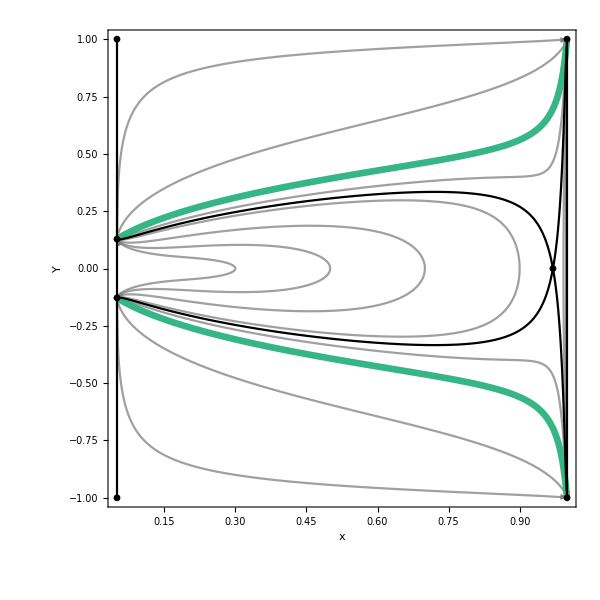

```mathematica
vSubMan=Show[Trajv,FFSv,CFSv,FPShowv,Sepx,FrameLabel->{"x",Rotate["Y",300]},ImageSize->{600,600},PlotRange->All]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\vSubMan.pdf",vSubMan]*)
```

### Potential

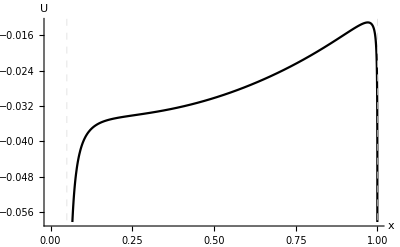

```mathematica
(*Plot the potential for this case*)
Uv0=Plot[{USubMan[a[x,0.2],x,Z[x,c[[1]]],0]},{x,0,1},AxesLabel->{"x","U"},PlotStyle->{Black},GridLines->{{.05,1},{}},GridLinesStyle->Directive[Thick,Dashed]]
```

## x = R Submanifold

### Y = 0 fixed points

```mathematica
(*Solve for Z when Y = 0*)
xRY0=Solve[wSubMan[R,Z/(1-Z),Vz[Z,cz]/(1-Vz[Z,cz])]==0,Z]
```

{{Z→0.0908456}}

```mathematica
(*Remove arrow and de-nest solution*)
xRY0=Z/.xRY0[[1]]
```

0.0908456

### Plot the 3D Submanifold

```mathematica
(*Trajectories for the phase space*)
traj3DxR[Y0_,Z0_]=R/3+Z/(3*(1-Z))+Vz[Z,cz]/(3*(1-Vz[Z,cz]))-(1/az[Z,Z0]^2)*(R/3+Z0/(3*(1-Z0))+Vz[Z0,cz]/(3*(1-Vz[Z0,cz]))-Y0^2/(1-Y0^2));
```

```mathematica
(*Rearrange above equation for Y*)
traj3DxR[Y0_,Z0_]=Sqrt[traj3DxR[Y0,Z0]/(1+traj3DxR[Y0,Z0])];
```

```mathematica
xRtraj3D[1]=ParametricPlot3D[{Z,traj3DxR[0,0.03],Vz[Z,cz]},{Z,0,xRY0},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[2]=ParametricPlot3D[{Z,-traj3DxR[0,0.03],Vz[Z,cz]},{Z,0,xRY0},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
xRtraj3D[3]=ParametricPlot3D[{Z,traj3DxR[0,0.03],Vz[Z,cz]},{Z,xRY0,1},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[4]=ParametricPlot3D[{Z,-traj3DxR[0,0.03],Vz[Z,cz]},{Z,xRY0,1},PlotPoints->200,PlotRange->All,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[5]=ParametricPlot3D[{Z,traj3DxR[0,0.6],Vz[Z,cz]},{Z,0,xRY0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[6]=ParametricPlot3D[{Z,-traj3DxR[0,0.6],Vz[Z,cz]},{Z,0,xRY0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
xRtraj3D[7]=ParametricPlot3D[{Z,traj3DxR[0,0.6],Vz[Z,cz]},{Z,xRY0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[8]=ParametricPlot3D[{Z,-traj3DxR[0,0.6],Vz[Z,cz]},{Z,xRY0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[9]=ParametricPlot3D[{Z,traj3DxR[0,0.9],Vz[Z,cz]},{Z,0,xRY0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[10]=ParametricPlot3D[{Z,-traj3DxR[0,0.9],Vz[Z,cz]},{Z,0,xRY0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
xRtraj3D[11]=ParametricPlot3D[{Z,traj3DxR[0,0.9],Vz[Z,cz]},{Z,xRY0,1},PlotPoints->2000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[12]=ParametricPlot3D[{Z,-traj3DxR[0,0.9],Vz[Z,cz]},{Z,xRY0,1},PlotPoints->2000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[13]=ParametricPlot3D[{Z,traj3DxR[0.4,0.45],Vz[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[14]=ParametricPlot3D[{Z,-traj3DxR[0.4,0.45],Vz[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[15]=ParametricPlot3D[{Z,traj3DxR[0.9,0.3],Vz[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[16]=ParametricPlot3D[{Z,-traj3DxR[0.9,0.3],Vz[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[17]=ParametricPlot3D[{Z,traj3DxR[0.75,0.5],Vz[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
xRtraj3D[18]=ParametricPlot3D[{Z,-traj3DxR[0.75,0.5],Vz[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Traj3DxR=Table[xRtraj3D[i],{i,1,18}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFS3DxR=ParametricPlot3D[{{Z,FFSSubMan[R,Z/(1-Z),Vz[Z,cz]],Vz[Z,cz]},{Z,-FFSSubMan[R,Z/(1-Z),Vz[Z,cz]],Vz[Z,cz]}},{Z,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFS3DxR=ParametricPlot3D[{{Z,CFSSubManZ[R,R,Z,xRY0,Vz[Z,cz],Vz[xRY0,cz]],Vz[Z,cz]},{Z,-CFSSubManZ[R,R,Z,xRY0,Vz[Z,cz],Vz[xRY0,cz]],Vz[Z,cz]}},{Z,0,1},PlotStyle->Black];
```

```mathematica
(*Plot the fixed points*)
FPShow3DxR=ListPointPlot3D[{{0,1,0},{0,-1,0},{1,1,1},{1,-1,1},{0,Sqrt[R/(3+R)],0},{0,-Sqrt[R/(3+R)],0},{xRY0,0,Vz[xRY0,cz]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
xRSubMan3D=Show[Traj3DxR,FFS3DxR,CFS3DxR,FPShow3DxR,Surfacecz,AxesLabel->{"Z","Y","V"},PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\xRSubMan3D.pdf",xRSubMan3D]*)
```

### Plot the Projected Z-Y Submanifold

```mathematica
(*Trajectories for the phase space*)
trajxR[Y0_,Z0_]:=Y^2/(1-Y^2)==R/3+Z/(3*(1-Z))+Vz[Z,cz]/(3*(1-Vz[Z,cz]))-(1/az[Z,Z0]^2)*(R/3+Z0/(3*(1-Z0))+Vz[Z0,cz]/(3*(1-Vz[Z0,cz]))-Y0^2/(1-Y0^2));
```

```mathematica
xRtraj[1]=ContourPlot[Evaluate[trajxR[0,0.03]],{Z,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
xRtraj[2]=ContourPlot[Evaluate[trajxR[0,0.03]],{Z,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xRtraj[3]=ContourPlot[Evaluate[trajxR[0,0.6]],{Z,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xRtraj[4]=ContourPlot[Evaluate[trajxR[0,0.9]],{Z,0.6,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xRtraj[5]=ContourPlot[Evaluate[trajxR[0.4,0.45]],{Z,0,1},{Y,0.1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xRtraj[6]=ContourPlot[Evaluate[trajxR[0.4,0.45]],{Z,0,1},{Y,-1,-0.1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xRtraj[7]=ContourPlot[Evaluate[trajxR[0.9,0.3]],{Z,0,1},{Y,0.1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xRtraj[8]=ContourPlot[Evaluate[trajxR[0.9,0.3]],{Z,0,1},{Y,-1,-0.1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xRtraj[9]=ContourPlot[Evaluate[trajxR[0.75,0.5]],{Z,0,1},{Y,0.1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xRtraj[10]=ContourPlot[Evaluate[trajxR[0.75,0.5]],{Z,0,1},{Y,-1,-0.1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
TrajxR=Table[xRtraj[i],{i,1,10}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSxR=Plot[{FFSSubMan[R,Z/(1-Z),Vz[Z,cz]],-FFSSubMan[R,Z/(1-Z),Vz[Z,cz]]},{Z,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSxR=Plot[{{CFSSubManZ[R,R,Z,xRY0,Vz[Z,cz],Vz[xRY0,cz]]},{-CFSSubManZ[R,R,Z,xRY0,Vz[Z,cz],Vz[xRY0,cz]]}},{Z,0,1},PlotStyle->Black];
```

```mathematica
(*Plot the fixed points*)
FPShowxR=ListPlot[{{0,1},{0,-1},{1,1},{1,-1},{0,Sqrt[R/(3+R)]},{0,-Sqrt[R/(3+R)]},{xRY0,0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

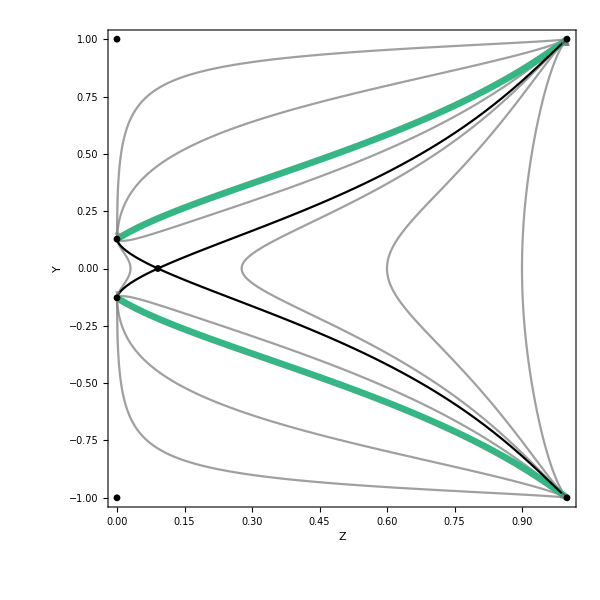

```mathematica
xRSubMan=Show[TrajxR,FFSxR,CFSxR,FPShowxR,FrameLabel->{"Z",Rotate["Y",300]},PlotRange->{{0,1},{-1,1}},ImageSize->{600,600}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\xRSubMan.pdf",xRSubMan]*)
```

### Potential

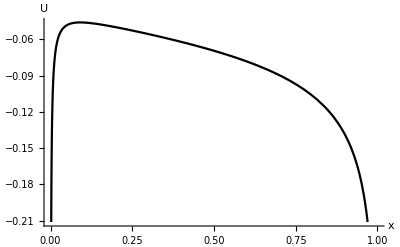

```mathematica
(*Plot the potential for this case*)
UxR=Plot[{USubMan[az[Z,0.2],R,Z,Vz[Z,cz]]},{Z,0,1},AxesLabel->{"x","U"},PlotStyle->{Black}]
```

## x = 1 Submanifold

### Y = 0 fixed points

```mathematica
(*Solve for Z when Y = 0*)
x1Y0=Solve[wSubMan[1,Z/(1-Z),Vz[Z,cz]/(1-Vz[Z,cz])]==0,Z];
```

```mathematica
(*Remove arrow and de-nest solution*)
x1Y0=Z/.x1Y0[[1]]
```

0.666203

### Plot the 3D Submanifold

```mathematica
(*Trajectories for the phase space*)
traj3Dx1[Y0_,Z0_]=1/3+Z/(3*(1-Z))+Vz[Z,cz]/(3*(1-Vz[Z,cz]))-(1/az[Z,Z0]^2)*(1/3+Z0/(3*(1-Z0))+Vz[Z0,cv]/(3*(1-Vz[Z0,cv]))-Y0^2/(1-Y0^2));
```

```mathematica
(*Rearrange above equation for Y*)
traj3Dx1[Y0_,Z0_]=Sqrt[traj3Dx1[Y0,Z0]/(1+traj3Dx1[Y0,Z0])];
```

```mathematica
x1traj3D[1]=ParametricPlot3D[{Z,traj3Dx1[0,0.1],Vz[Z,cz]},{Z,0,x1Y0},PlotPoints->1000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[2]=ParametricPlot3D[{Z,-traj3Dx1[0,0.1],Vz[Z,cz]},{Z,0,x1Y0},PlotPoints->1000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[3]=ParametricPlot3D[{Z,traj3Dx1[0,0.1],Vz[Z,cz]},{Z,x1Y0,1},PlotPoints->20000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[4]=ParametricPlot3D[{Z,-traj3Dx1[0,0.1],Vz[Z,cz]},{Z,x1Y0,1},PlotPoints->20000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[5]=ParametricPlot3D[{Z,traj3Dx1[0,0.25],Vz[Z,cz]},{Z,0,x1Y0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[6]=ParametricPlot3D[{Z,-traj3Dx1[0,0.25],Vz[Z,cz]},{Z,0,x1Y0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[7]=ParametricPlot3D[{Z,traj3Dx1[0,0.25],Vz[Z,cz]},{Z,x1Y0,1},PlotPoints->2000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[8]=ParametricPlot3D[{Z,-traj3Dx1[0,0.25],Vz[Z,cz]},{Z,x1Y0,1},PlotPoints->2000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[9]=ParametricPlot3D[{Z,traj3Dx1[0,0.4],Vz[Z,cz]},{Z,0,x1Y0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[10]=ParametricPlot3D[{Z,-traj3Dx1[0,0.4],Vz[Z,cz]},{Z,0,x1Y0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[11]=ParametricPlot3D[{Z,traj3Dx1[0,0.4],Vz[Z,cz]},{Z,x1Y0,1},PlotPoints->1000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[12]=ParametricPlot3D[{Z,-traj3Dx1[0,0.4],Vz[Z,cz]},{Z,x1Y0,1},PlotPoints->1000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[13]=ParametricPlot3D[{Z,traj3Dx1[0.25,0.55],Vz[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[14]=ParametricPlot3D[{Z,-traj3Dx1[0.25,0.55],Vz[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[15]=ParametricPlot3D[{Z,traj3Dx1[0.5,0.3],Vz[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[16]=ParametricPlot3D[{Z,-traj3Dx1[0.5,0.3],Vz[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[17]=ParametricPlot3D[{Z,traj3Dx1[0.9,0.3],Vz[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[18]=ParametricPlot3D[{Z,-traj3Dx1[0.9,0.3],Vz[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Traj3Dx1=Table[x1traj3D[i],{i,1,18}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFS3Dx1=ParametricPlot3D[{{Z,FFSSubMan[1,Z/(1-Z),Vz[Z,cz]/(1-Vz[Z,cz])],Vz[Z,cz]},{Z,-FFSSubMan[1,Z/(1-Z),Vz[Z,cz]/(1-Vz[Z,cz])],Vz[Z,cz]}},{Z,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFS3Dx1=ParametricPlot3D[{{Z,CFSSubManZ[1,1,Z,x1Y0,Vz[Z,cz],Vz[x1Y0,cz]],Vz[Z,cz]},{Z,-CFSSubManZ[1,1,Z,x1Y0,Vz[Z,cz],Vz[x1Y0,cz]],Vz[Z,cz]}},{Z,0,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points*)
FPShow3Dx1=ListPointPlot3D[{{0,1/2,0},{0,-1/2,0},{0,1,0},{0,-1,0},{1,1,1},{1,-1,1}, {x1Y0,0,Vz[x1Y0,cz]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
x1SubMan3D=Show[Traj3Dx1,FFS3Dx1,CFS3Dx1,FPShow3Dx1,Surfacecz,AxesLabel->{"Z","Y","V"},PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\x1SubMan3D.pdf",x1SubMan3D]*)
```

### Plot the Projected Z-Y Submanifold

```mathematica
(*Trajectories for the phase space*)
trajx1[Y0_,Z0_]:=Y^2/(1-Y^2)==1/3+Z/(3*(1-Z))+Vz[Z,cz]/(3*(1-Vz[Z,cz]))-(1/az[Z,Z0]^2)*(1/3+Z0/(3*(1-Z0))+Vz[Z0,cv]/(3*(1-Vz[Z0,cv]))-Y0^2/(1-Y0^2));
```

```mathematica
x1traj[1]=ContourPlot[Evaluate[trajx1[0,0.1]],{Z,0,x1Y0},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[2]=ContourPlot[Evaluate[trajx1[0,0.1]],{Z,x1Y0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[3]=ContourPlot[Evaluate[trajx1[0,0.25]],{Z,0,x1Y0},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[4]=ContourPlot[Evaluate[trajx1[0,0.25]],{Z,x1Y0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[5]=ContourPlot[Evaluate[trajx1[0,0.4]],{Z,0,x1Y0},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[6]=ContourPlot[Evaluate[trajx1[0,0.4]],{Z,x1Y0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[7]=ContourPlot[Evaluate[trajx1[0.25,0.55]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[8]=ContourPlot[Evaluate[trajx1[0.25,0.55]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[9]=ContourPlot[Evaluate[trajx1[0.5,0.3]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[10]=ContourPlot[Evaluate[trajx1[0.5,0.3]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[11]=ContourPlot[Evaluate[trajx1[0.9,0.3]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[12]=ContourPlot[Evaluate[trajx1[0.9,0.3]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajx1=Table[x1traj[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSx1=Plot[{FFSSubMan[1,Z/(1-Z),Vz[Z,cz]/(1-Vz[Z,cz])],-FFSSubMan[1,Z/(1-Z),Vz[Z,cz]/(1-Vz[Z,cz])]},{Z,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSx1=Plot[{CFSSubManZ[1,1,Z,x1Y0,Vz[Z,cz],Vz[x1Y0,cz]],-CFSSubManZ[1,1,Z,x1Y0,Vz[Z,cz],Vz[x1Y0,cz]]},{Z,0,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points*)
FPShowx1=ListPlot[{{0,1},{0,-1},{0,1/2},{0,-1/2},{1,1},{1,-1}, {x1Y0,0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

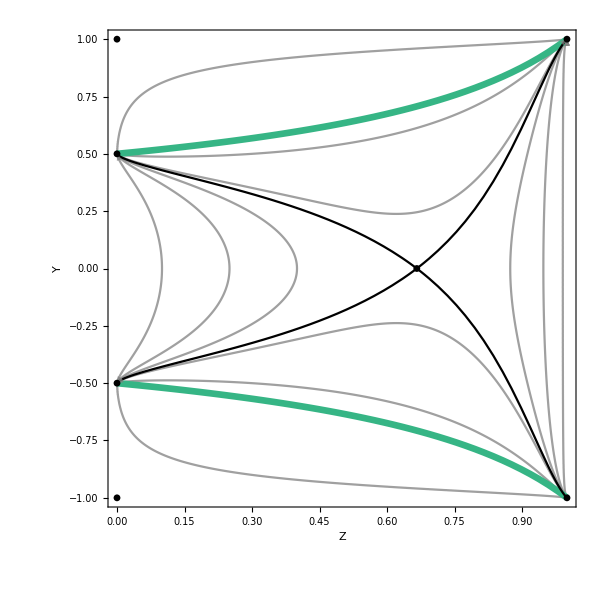

```mathematica
x1SubMan=Show[Trajx1,FFSx1,CFSx1,FPShowx1,FrameLabel->{"Z",Rotate["Y",300]},PlotRange->{{0,1},{-1,1}},ImageSize->{600,600}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\x1SubMan.pdf",x1SubMan]*)
```

### Potential

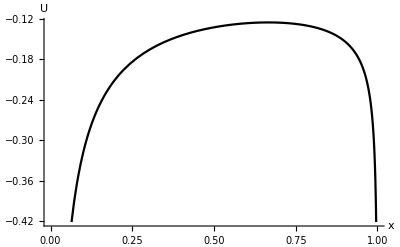

```mathematica
(*Plot the potential for this case*)
Ux1=Plot[{USubMan[az[Z,0.2],1,Z,Vz[Z,cz]]},{Z,0,1},AxesLabel->{"x","U"},PlotStyle->{Black}]
```

## Y = 0 Submanifold

### Plot the 3D Submanifold

```mathematica
(*Trajectories for the phase space*)
(*Written in terms of z*)
Y0z[x_,x0_,Z0_,V_,V0_]=(1/(a[x,x0]^2))*(x0+Z0/(1-Z0)+V0/(1-V0))-x-V/(1-V);
```

```mathematica
(*Write in terms of compact Z*)
(*x' = Z' = V' = 0, so x = x0, Z = Z0 and V = V0*)
Y0Z=Simplify[Y0z[x0,x0,Z0,V0,V0]/(1+Y0z[x0,x0,Z0,V0,V0])]
```

1. Z0

```mathematica
(*Z is always a constant for any value of x and V, which are also always constants independent of each other*)
traj3DYZ[Z0_]:=Z0
```

```mathematica
(*Similarly, we can write the above equation in terms of V*)
Y0v[x_,x0_,Z_,Z0_,V0_]=(1/(a[x0,x0]^2))*(x0+Z0/(1-Z0)+V0/(1-V0))-x-Z/(1-Z);
Y0V=Simplify[Y0v[x0,x0,Z0,Z0,V0]/(1+Y0v[x0,x0,Z0,Z0,V0])]
```

1. V0

```mathematica
(*V is always a constant for any value of x and Z, which are also always constants independent of each other*)
traj3DYV[V0_]:=V0
```

```mathematica
Ytraj3D[1]=ParametricPlot3D[{x,traj3DYZ[0.1],traj3DYV[0.1]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj3D[2]=ParametricPlot3D[{x,traj3DYZ[0.1],traj3DYV[0.3]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0,0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj3D[3]=ParametricPlot3D[{x,traj3DYZ[0.1],traj3DYV[0.5]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj3D[4]=ParametricPlot3D[{x,traj3DYZ[0.1],traj3DYV[0.7]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj3D[5]=ParametricPlot3D[{x,traj3DYZ[0.1],traj3DYV[0.9]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj3D[6]=ParametricPlot3D[{x,traj3DYZ[0.3],traj3DYV[0.1]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0,0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj3D[7]=ParametricPlot3D[{x,traj3DYZ[0.3],traj3DYV[0.3]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0,0,0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj3D[8]=ParametricPlot3D[{x,traj3DYZ[0.3],traj3DYV[0.5]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj3D[9]=ParametricPlot3D[{x,traj3DYZ[0.3],traj3DYV[0.7]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj3D[10]=ParametricPlot3D[{x,traj3DYZ[0.3],traj3DYV[0.9]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj3D[11]=ParametricPlot3D[{x,traj3DYZ[0.5],traj3DYV[0.1]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj3D[12]=ParametricPlot3D[{x,traj3DYZ[0.5],traj3DYV[0.3]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0,0,0,0,0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj3D[13]=ParametricPlot3D[{x,traj3DYZ[0.5],traj3DYV[0.5]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj3D[14]=ParametricPlot3D[{x,traj3DYZ[0.5],traj3DYV[0.7]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj3D[15]=ParametricPlot3D[{x,traj3DYZ[0.5],traj3DYV[0.9]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj3D[16]=ParametricPlot3D[{x,traj3DYZ[0.7],traj3DYV[0.1]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0,0,0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj3D[17]=ParametricPlot3D[{x,traj3DYZ[0.7],traj3DYV[0.3]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0,-.02},1]]],Arrow[x]};
```

```mathematica
Ytraj3D[18]=ParametricPlot3D[{x,traj3DYZ[0.7],traj3DYV[0.5]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj3D[19]=ParametricPlot3D[{x,traj3DYZ[0.7],traj3DYV[0.7]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj3D[20]=ParametricPlot3D[{x,traj3DYZ[0.7],traj3DYV[0.9]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj3D[21]=ParametricPlot3D[{x,traj3DYZ[0.9],traj3DYV[0.1]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj3D[22]=ParametricPlot3D[{x,traj3DYZ[0.9],traj3DYV[0.3]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj3D[23]=ParametricPlot3D[{x,traj3DYZ[0.9],traj3DYV[0.5]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj3D[24]=ParametricPlot3D[{x,traj3DYZ[0.9],traj3DYV[0.7]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj3D[25]=ParametricPlot3D[{x,traj3DYZ[0.9],traj3DYV[0.9]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Traj3DY=Table[Ytraj3D[i],{i,1,25}];
```

```mathematica
(*Curve of possible Einstein points (where Y = 0)*)
wSubMan[x,z,v]
```

1/6 (0.15-2 v-1.15 x+3 x^2-z)

```mathematica
(*Define wSubMan = 0 in terms of z*)
zSepY0=z/.Simplify[Solve[wSubMan[x,z,V/(1-V)]==0,z]][[1]]
```

0.15+(2. V)/(-1.+1. V)-1.15 x+3. x^2

```mathematica
(*For positive values of x and v, z can be positive or negative, so the compactification is done in the same way as Y*)
ZSepY0[x_,V_]=zSepY0/Sqrt[1+zSepY0^2]
```

(0.15+(2. V)/(-1.+1. V)-1.15 x+3. x^2)/(√(1+(0.15+(2. V)/(-1.+1. V)-1.15 x+3. x^2)^2))

```mathematica
Sep3DY=ParametricPlot3D[{x,ZSepY0[x,V],V},{x,0,1},{V,0,1},PlotStyle->{Cyan}];
```

```mathematica
(*Show all components of plot*)
YSubMan3D=Show[Traj3DY,Sep3DY,AxesLabel->{"x","Z","V"},ImageSize->{600,600},PlotRange->{{0,1},{0,1},{0,1}}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\YSubMan3D.pdf",YSubMan3D]*)
```

### Plot the V = 0 Sub-submanifold

```mathematica
(*Define trajectories for the sub-submanifold*)
(*Z = Z0 *)
trajYZ[Z0_]:=Z0
```

```mathematica
Ytraj[1]=Plot[Evaluate[trajYZ[0]],{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj[2]=Plot[Evaluate[trajYZ[0.2]],{x,0,0.5},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj[3]=Plot[Evaluate[trajYZ[0.4]],{x,0,0.65},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj[4]=Plot[Evaluate[trajYZ[0.6]],{x,0,0.9},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj[5]=Plot[Evaluate[trajYZ[0.8]],{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj[6]=Plot[Evaluate[trajYZ[1]],{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj[7]=Plot[Evaluate[trajYZ[0.2]],{x,0.5,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj[8]=Plot[Evaluate[trajYZ[0.4]],{x,0.65,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj[9]=Plot[Evaluate[trajYZ[0.6]],{x,0.9,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
TrajY=Table[Ytraj[i],{i,1,9}];
```

```mathematica
(*Curve of possible Einstein points (where Y = 0)*)
SepY=ContourPlot[{Z/(1-Z)==3*R-(1+3*R)*x+3*x^2},{x,0,1},{Z,0,1},ContourStyle->{Black},Frame->True,PlotRange->{{0,1},{-0.05,1.05}},PlotPoints->200];
```

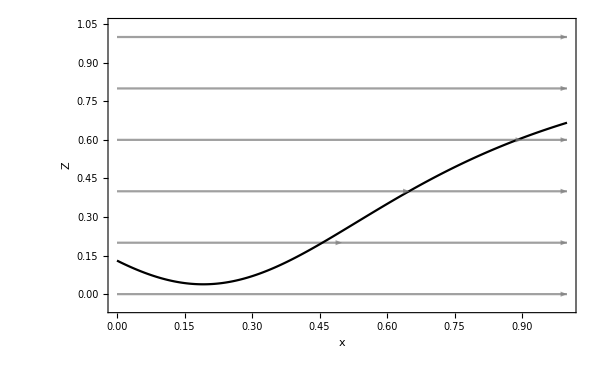

```mathematica
(*Show all components of plot*)
YSubManV0=Show[TrajY,SepY,FrameLabel->{"x","Z"},ImageSize->{600,400}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\YSubManV0.pdf",YSubManV0]*)
```

### Potential

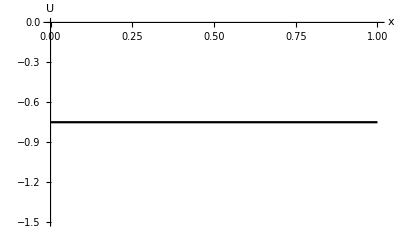

```mathematica
(*Plot the potential for this case*)
(*Y^2/(1-Y^2) + U = E --> U = E*)
UY0V0=Plot[{USubMan[a[x0,x0],0.5,0.8,0]},{x,0,1},AxesLabel->{"x","U"},PlotStyle->{Black}]
```

### Plot the Z = 0 Sub-submanifold

```mathematica
(*V = V0 *)
trajYV[V0_]:=V0
```

```mathematica
Ytraj[1]=Plot[Evaluate[trajYV[0]],{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj[2]=Plot[Evaluate[trajYV[0.2]],{x,0,0.5},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj[3]=Plot[Evaluate[trajYV[0.4]],{x,0,0.65},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj[4]=Plot[Evaluate[trajYV[0.6]],{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj[5]=Plot[Evaluate[trajYV[0.8]],{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj[6]=Plot[Evaluate[trajYV[1]],{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj[7]=Plot[Evaluate[trajYV[0.2]],{x,0.5,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj[8]=Plot[Evaluate[trajYV[0.4]],{x,0.65,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,0,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
TrajY=Table[Ytraj[i],{i,1,8}];
```

```mathematica
(*Curve of possible Einstein points (where Y = 0)*)
SepYV=ContourPlot[{2*V/(1-V)==3*R-(1+3*R)*x+3*x^2},{x,0,1},{V,0,1},ContourStyle->{Black},Frame->True,PlotRange->{{0,1},{-0.05,1.05}},PlotPoints->200];
```

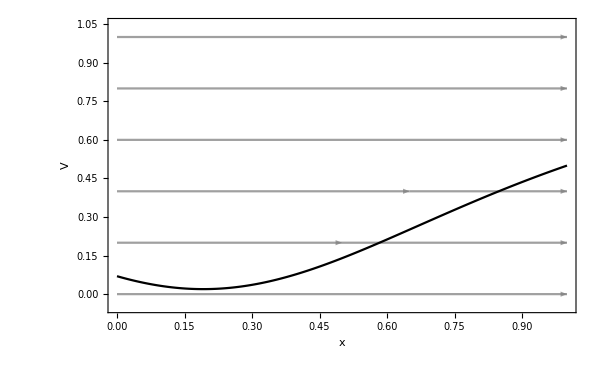

```mathematica
(*Show all components of plot*)
YSubManZ0=Show[TrajY,SepYV,FrameLabel->{"x","V"},ImageSize->{600,400}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\YSubManZ0.pdf",YSubManZ0]*)
```

### Potential

```mathematica
(*Plot the potential for this case*)
(*Y^2/(1-Y^2) + U = E --> U = E*)
UY0Z0=Plot[{USubMan[a[x0,x0],0.5,0,0.8]},{x,0,1},AxesLabel->{"x","U"},PlotStyle->{Black}]
```

-Graphics-

## k = 0 Submanifold

### Find the Y = 0 fixed points

```mathematica
(*z in the flat case*)
zk0[Y_,x_]=3*Y^2/(1-Y^2)-x-v[x,cv];
```

```mathematica
(*Compact Z in the flat case*)
Zk0[Y_,x_]=zk0[Y,x]/Sqrt[1+zk0[Y,x]^2];
```

```mathematica
kY0=FindRoot[wSubMan[x,zk0[0,x],v[x,cv]]==0,{x,0.99}];
```

```mathematica
kY0=x/.kY0
```

0.997371

### Plot the 3D Submanifold

```mathematica
(*Defining ck, the first integral of z(x), for this case*)
ck[Y0_,x0_]=zk0[Y0,x0]*((1-x0)/(x0-R))^(1/(1-R));
```

```mathematica
(*Trajectories for the phase space*)
traj3Dk[Y0_,x0_]=x/3+z[x,ck[Y0,x0]]/3+v[x,cv]/3;
```

```mathematica
(*Rearrange above equation for Y*)
traj3Dk[Y0_,x0_]=Sqrt[traj3Dk[Y0,x0]/(1+traj3Dk[Y0,x0])];
```

```mathematica
ktraj3D[1]=ParametricPlot3D[{x,traj3Dk[0,0.2],Zk0[traj3Dk[0,0.2],x]},{x,0,kY0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj3D[2]=ParametricPlot3D[{x,-traj3Dk[0,0.2],Zk0[-traj3Dk[0,0.2],x]},{x,0,kY0},PlotPoints->100,AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj3D[3]=ParametricPlot3D[{x,traj3Dk[0,0.2],Zk0[traj3Dk[0,0.2],x]},{x,kY0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj3D[4]=ParametricPlot3D[{x,-traj3Dk[0,0.2],Zk0[-traj3Dk[0,0.2],x]},{x,kY0,1},PlotPoints->100,AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj3D[5]=ParametricPlot3D[{x,traj3Dk[0,0.6],Zk0[traj3Dk[0,0.6],x]},{x,0,0.9},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj3D[6]=ParametricPlot3D[{x,-traj3Dk[0,0.6],Zk0[-traj3Dk[0,0.6],x]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj3D[7]=ParametricPlot3D[{x,traj3Dk[0,0.9],Zk0[traj3Dk[0,0.9],x]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj3D[8]=ParametricPlot3D[{x,-traj3Dk[0,0.9],Zk0[-traj3Dk[0,0.9],x]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj3D[9]=ParametricPlot3D[{x,traj3Dk[0.4,0.45],Zk0[traj3Dk[0.4,0.45],x]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj3D[10]=ParametricPlot3D[{x,-traj3Dk[0.4,0.45],Zk0[-traj3Dk[0.4,0.45],x]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj3D[11]=ParametricPlot3D[{x,traj3Dk[0.9,0.3],Zk0[traj3Dk[0.9,0.3],x]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj3D[12]=ParametricPlot3D[{x,-traj3Dk[0.9,0.3],Zk0[-traj3Dk[0.9,0.3],x]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj3D[13]=ParametricPlot3D[{x,traj3Dk[0.75,0.5],Zk0[traj3Dk[0.75,0.5],x]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj3D[14]=ParametricPlot3D[{x,-traj3Dk[0.75,0.5],Zk0[-traj3Dk[0.75,0.5],x]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj3D[15]=ParametricPlot3D[{x,traj3Dk[0.48,0.95],Zk0[traj3Dk[0.48,0.95],x]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj3D[16]=ParametricPlot3D[{x,-traj3Dk[0.48,0.95],Zk0[-traj3Dk[0.48,0.95],x]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Traj3Dk=Table[ktraj3D[i],{i,1,16}];
```

```mathematica
(*Separatrix where Z = 0*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
Sep3Dk=ParametricPlot3D[{{x,Sqrt[(x+v[x,cv])/(3+x+v[x,cv])],V[x,cv]},{x,-Sqrt[(x+v[x,cv])/(3+x+v[x,cv])],V[x,cv]}},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
traj3Dk[0,kY0]
```

√((-0.00270241 ((-0.05+x)/(1-x))^1.05263+0.000256723 ((-0.05+x)/(1-x))^1.40351+x/3)/(1-0.00270241 ((-0.05+x)/(1-x))^1.05263+0.000256723 ((-0.05+x)/(1-x))^1.40351+x/3))

```mathematica
(*Plot the separatrix for the fixed point where Y = 0*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFS3Dk=ParametricPlot3D[{{x,traj3Dk[0,kY0],Zk0[traj3Dk[0,kY0],x]},{x,-traj3Dk[0,kY0],Zk0[traj3Dk[0,kY0],x]}},{x,0,1},PlotStyle->{Black},PlotRange->{{0,1},{-1,1},{-2,1}}];
```

```mathematica
(*Fixed points of the system*)
FPShow3Dk=ListPointPlot3D[{{1,1,1},{1,-1,1},{1,1,-1},{1,-1,-1},{R,1,0},{R,-1,0},{R,Sqrt[R/(3+R)],0},{R,-Sqrt[R/(3+R)],0},{kY0,0,Zk0[0,kY0]}},PlotStyle->{Black},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Show all components of plot*)
kSubMan3D=Show[Traj3Dk,Sep3Dk,CFS3Dk,FPShow3Dk,AxesLabel->{"x","Y","Z"},ImageSize->{600,400},PlotRange->{{0,1},{-1,1},{-1,1}}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\kSubMan3D.pdf",kSubMan3D]*)
```

### Plot the Projected x-Y Submanifold

```mathematica
(*Trajectories for the phase space*)
trajk[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,ck[Y0,x0]]/3+v[x,cv]/3;
```

```mathematica
ktraj[1]=ContourPlot[Evaluate[trajk[0,0.2]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj[2]=ContourPlot[Evaluate[trajk[0,0.6]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj[3]=ContourPlot[Evaluate[trajk[0,0.9]],{x,0,kY0},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj[4]=ContourPlot[Evaluate[trajk[0,0.9]],{x,kY0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj[5]=ContourPlot[Evaluate[trajk[0.4,0.45]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj[6]=ContourPlot[Evaluate[trajk[0.4,0.45]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj[7]=ContourPlot[Evaluate[trajk[0.9,0.3]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj[8]=ContourPlot[Evaluate[trajk[0.9,0.3]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj[9]=ContourPlot[Evaluate[trajk[0.75,0.5]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj[10]=ContourPlot[Evaluate[trajk[0.75,0.5]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj[11]=ContourPlot[Evaluate[trajk[0.48,0.95]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj[12]=ContourPlot[Evaluate[trajk[0.48,0.95]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajk=Table[ktraj[i],{i,1,12}];
```

```mathematica
(*Separatrix where z = 0*)
Sepk=ContourPlot[{3*Y^2/(1-Y^2)-x-v[x,cv]==0},{x,0,1},{Y,-1,1},ContourStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]},PlotPoints->100];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSk=Plot[{traj3Dk[0,kY0],-traj3Dk[0,kY0]},{x,0,1},PlotStyle->{Black}];
```

```mathematica
(*Fixed points of the system*)
FPShowk=ListPlot[{{1,1},{1,-1},{R,1},{R,-1},{R,Sqrt[R/(3+R)]},{R,-Sqrt[R/(3+R)]},{kY0,0}},PlotStyle->{Black},PlotMarkers->{Automatic,Medium}, PlotStyle->{Black}];
```

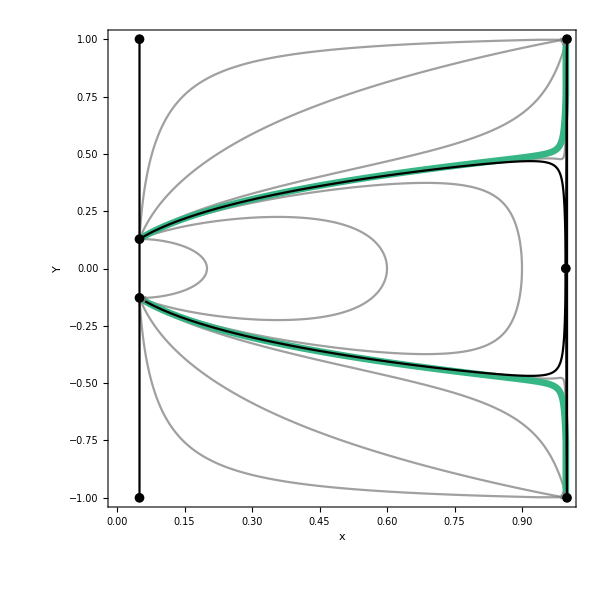

```mathematica
(*Show all components of plot*)
kSubMan=Show[Trajk,Sepk,CFSk,FPShowk,Sepx,FrameLabel->{"x",Rotate["Y",300]},ImageSize->{600,600}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\kSubMan.pdf",kSubMan]*)
```

### Potential

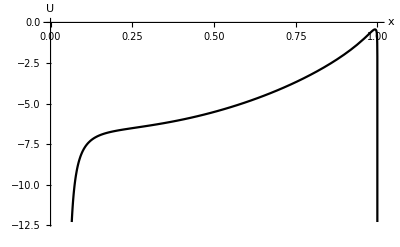

```mathematica
(*Plot the potential for this case*)
Uk0=Plot[{USubMan[a[x,kY0],x,z[x,ck[0,kY0]]/Sqrt[1+z[x,ck[0,kY0]]^2],V[x,cv]]},{x,0,1},AxesLabel->{"x","U"},PlotStyle->{Black}]
```

## x-Y Phase Spaces and Potentials

## Set-up

### Phase Spaces

```mathematica
(*Define the Flat Friedmann Separatrix (FFS)*)
(*Define ffs = Y^2/(1-Y^2)*)
ffs=(1/3)*(x+z[x,c]+v[x,cv]);
```

```mathematica
(*Rearrange for Y*)
FFS=Sqrt[ffs/(1+ffs)];
```

```mathematica
(*Set up the plot for the x = R and x = 1 separatrices*)
Sep=ContourPlot[{x==R,x==1},{x,0,1},{Y,-1,1},ContourStyle->{Black}];
```

```mathematica
(*Define the Closed Friedmann Separatrix (CFS)*)
(*Define cfs = Y^2/(1-Y^2)*)
cfs[x0_]= x/3+z[x,c]/3+v[x,cv]/3-(x0/3+z[x0,c]/3+v[x0,cv]/3)/(a[x,x0]^2);
```

```mathematica
(*Rearrange above equation for Y*)
CFS[x0_]=Sqrt[cfs[x0]/(1+cfs[x0])];
```

```mathematica
(*Set up plot for the common fixed points*)
FPShow=ListPlot[{{R,Sqrt[R/(3+R)]},{R,-Sqrt[R/(3+R)]},{R,1},{R,-1},{1,1},{1,-1}},PlotStyle->{Black},PlotMarkers->{Automatic,Small}, PlotStyle->{Black}];
```

```mathematica
(*Define the acceleration*)
Accn=z[x,c]+x+2*v[x,cv]-3*R+3*R*x-3*x^2;
```

### Potentials

```mathematica
(*Define the potential*)
U[x_,x0_]=-a[x,x0]^2*(x/6+z[x,c]/6+v[x,cv]/6);
```

```mathematica
(*Find the first derivative of U with respect to x*)
dUdx=Simplify[D[U[x,x0],x]];
```

```mathematica
(*Find the second derivative of U with respect to x*)
d2Udx2[x_,x0_]=Simplify[D[U[x,x0],{x,2}]];
```

```mathematica
(*Define the energy of the trajectories*)
Energy[x0_,Y0_]=-(x0/6+z[x0,c]/6+v[x0,cv]/6-Y0^2/(2*(1-Y0^2)));
```

## One Einstein Point: c1

### Phase Space

```mathematica
(*Trajectories for the phase space*)
(*We plot the trajectories using the first integral (Friedmann equation) rather than the differential equations*)
trajc1[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[1]]/3+v[x,cv]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[1]]/3+v[x0,cv]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Trajectories plotted individually to ensure arrows are pointing in the right direction*)
```

```mathematica
c1traj[1]=ContourPlot[Evaluate[trajc1[0,0.2]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[2]=ContourPlot[Evaluate[trajc1[0,0.2]],{x,0.6,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[3]=ContourPlot[Evaluate[trajc1[0.12,0.2]],{x,0,0.8},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[4]=ContourPlot[Evaluate[trajc1[0.12,0.2]],{x,0.9,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[5]=ContourPlot[Evaluate[trajc1[0.18,0.2]],{x,0,0.9},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[6]=ContourPlot[Evaluate[trajc1[0.18,0.2]],{x,0.9,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[7]=ContourPlot[Evaluate[trajc1[0.225,0.2]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[8]=ContourPlot[Evaluate[trajc1[0.225,0.2]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[9]=ContourPlot[Evaluate[trajc1[0.5,0.2]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[10]=ContourPlot[Evaluate[trajc1[0.5,0.2]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[11]=ContourPlot[Evaluate[trajc1[0.9,0.2]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[12]=ContourPlot[Evaluate[trajc1[0.9,0.2]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc1=Table[c1traj[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc1=Plot[{FFS[[1]],-FFS[[1]]},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc1=Plot[{CFS[xOneEinsteinPointc1][[1]],-CFS[xOneEinsteinPointc1][[1]]},{x,0,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc1=ListPlot[{{xOneEinsteinPointc1,0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc1=ContourPlot[Accn[[1]]==0,{x,0,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

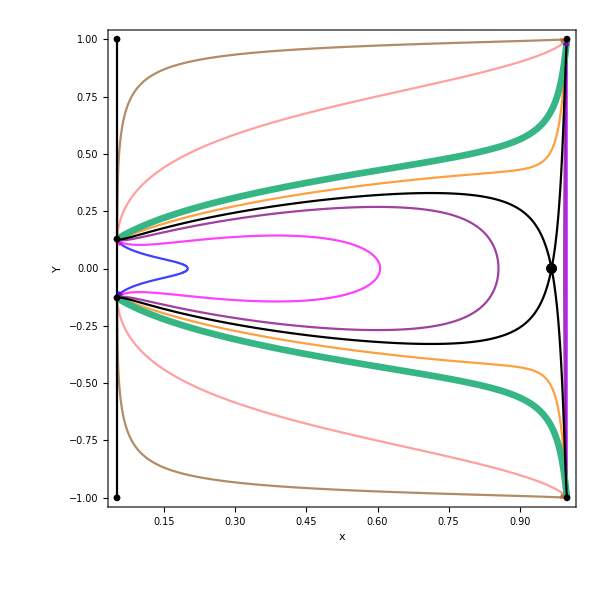

```mathematica
(*Show all components of plots*)
PhaseSpacec1=Show[Trajc1, FFSc1,CFSc1,Einsteinc1,Sep,FPShow,PlotRange->All,FrameLabel->{"x",Rotate["Y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative to find whether point is a maximum or a minimum*)
(*A positive/negative value means it's a minimum/maximum*)
d2Udx2[xOneEinsteinPointc1,0.2][[1]]
```

-3.25213

```mathematica
(*Plot the potential for this case*)
Uc1=Plot[{U[x,0.2][[1]]},{x,0,1},AxesLabel->{"x","U"},PlotStyle->{Black},GridLines->{{.05,1},{}},GridLinesStyle->Directive[Thick,Dashed]];
```

```mathematica
(*Plot the energy from each trajectory in the phase space*)
```

```mathematica
c1Energy[1]=Plot[{Energy[0.2,0][[1]]},{x,0.05,0.2},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c1Energy[2]=Plot[{Energy[0.2,0.12][[1]]},{x,0.05,0.6},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c1Energy[3]=Plot[{Energy[0.2,0.18][[1]]},{x,0.05,0.85},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c1Energy[4]=Plot[{Energy[0.2,0.225][[1]]},{x,0.1,0.45},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c1Energy[5]=Plot[{Energy[0.2,0.5][[1]]},{x,0.6,0.73},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c1Energy[6]=Plot[{Energy[0.2,0.5][[1]]},{x,0.27,1},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c1Energy[7]=Plot[{Energy[0.2,0.9][[1]]},{x,0.05,0.12},AxesLabel->{"x","U"},PlotStyle->{Brown,Dashed,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c1Energy[8]=Plot[{0},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c1Energy[9]=Plot[{Energy[0.2,0][[1]]},{x,0.2,1},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c1Energy[10]=Plot[{Energy[0.2,0.12][[1]]},{x,0.6,1},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c1Energy[11]=Plot[{Energy[0.2,0.18][[1]]},{x,0.85,1},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc1=Table[c1Energy[i],{i,1,11}];
```

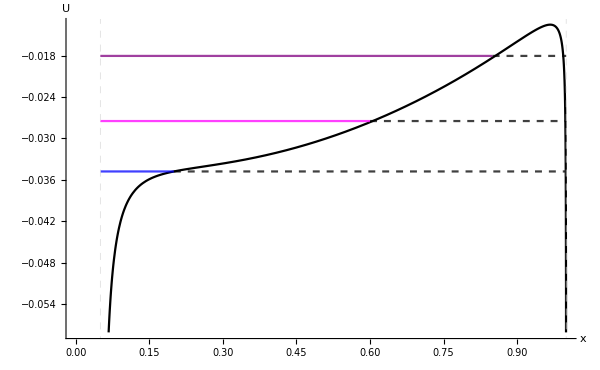

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc1=Show[Uc1,Energyc1,ImageSize->{600,400},BaseStyle->{FontSize->14}]
```

### Final Plot

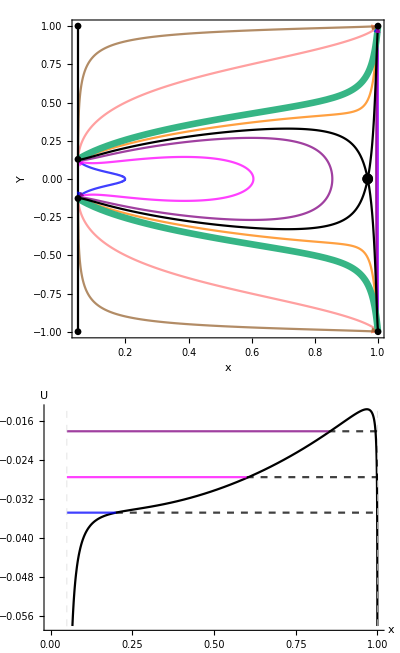

```mathematica
(*Plot the phase space and potential together*)
xYc1=GraphicsColumn[{PhaseSpacec1,Potentialc1},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xY_Plots\\xYc1.pdf",xYc1]*)
```

## Two Einstein Points: c2

### Phase Space

```mathematica
(*Trajectories for the phase space*)
(*We plot the trajectories using the first integral (Friedmann equation) rather than the differential equations*)
trajc2[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[2]]/3+v[x,cv]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[2]]/3+v[x0,cv]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Trajectories plotted individually to ensure arrows are pointing in the right direction*)
```

```mathematica
c2traj[1]=ContourPlot[Evaluate[trajc2[0,0.1]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[2]=ContourPlot[Evaluate[trajc2[0,0.1]],{x,0.8,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[3]=ContourPlot[Evaluate[trajc2[0.07,0.1]],{x,0,0.6},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[4]=ContourPlot[Evaluate[trajc2[0.07,0.1]],{x,0.8,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[5]=ContourPlot[Evaluate[trajc2[0.09,0.1]],{x,0,0.8},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[6]=ContourPlot[Evaluate[trajc2[0.09,0.1]],{x,0.8,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[7]=ContourPlot[Evaluate[trajc2[0.13,0.1]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[8]=ContourPlot[Evaluate[trajc2[0.4,0.1]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[9]=ContourPlot[Evaluate[trajc2[0.4,0.1]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[10]=ContourPlot[Evaluate[trajc2[0.9,0.1]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[11]=ContourPlot[Evaluate[trajc2[0.9,0.1]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc2=Table[c2traj[i],{i,1,11}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc2=Plot[{FFS[[2]],-FFS[[2]]},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS curves*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc2=Plot[{CFS[xTwoEinsteinPointsc2][[2]],-CFS[xTwoEinsteinPointsc2][[2]]},{x,0,1},PlotStyle->{Black},PlotRange->Full,PlotPoints->500];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc2=ListPlot[{{xTwoEinsteinPointsc2[[1]],0},{xTwoEinsteinPointsc2[[2]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc2=ContourPlot[Accn[[2]]==0,{x,0,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

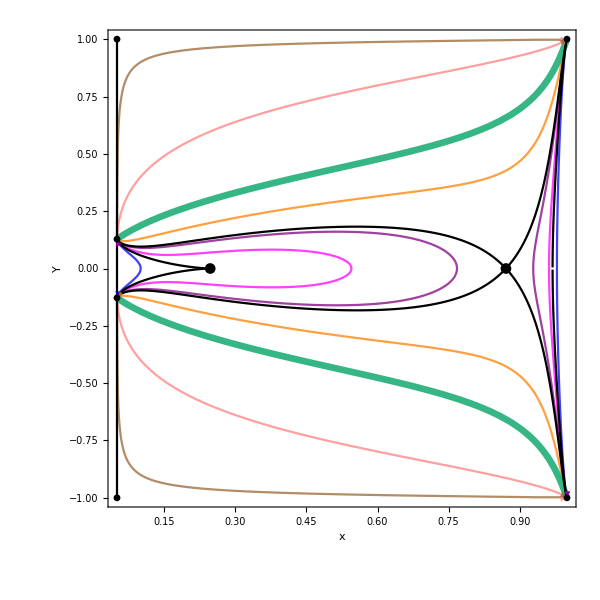

```mathematica
(*Show all components of plots*)
PhaseSpacec2=Show[Trajc2, FFSc2,CFSc2,Einsteinc2,Sep,FPShow,PlotRange->All,FrameLabel->{"x",Rotate["Y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative to find whether point is a maximum or a minimum*)
(*A positive/negative value means it's a minimum/maximum*)
d2Udx2[xTwoEinsteinPointsc2[[1]],0.1][[2]]
```

-5.42565×10^-9

```mathematica
d2Udx2[xTwoEinsteinPointsc2[[2]],0.1][[2]]
```

-0.177947

```mathematica
(*Plot the potential for this case*)
Uc2=Plot[{U[x,0.1][[2]]},{x,0,1},AxesLabel->{"x","U"},PlotStyle->{Black},GridLines->{{.05,1},{}},GridLinesStyle->Directive[Thick,Dashed]];
```

```mathematica
c2Energy[1]=Plot[{Energy[0.1,0][[2]]},{x,0.05,0.1},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c2Energy[2]=Plot[{Energy[0.1,0][[2]]},{x,0.98,1},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c2Energy[3]=Plot[{Energy[0.1,0.07][[2]]},{x,0.05,0.54},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c2Energy[4]=Plot[{Energy[0.1,0.07][[2]]},{x,0.965,1},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c2Energy[5]=Plot[{Energy[0.1,0.09][[2]]},{x,0.05,0.765},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c2Energy[6]=Plot[{Energy[0.1,0.09][[2]]},{x,0.93,1},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c2Energy[7]=Plot[{Energy[0.1,0.13][[2]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c2Energy[8]=Plot[{Energy[0.1,0.4][[2]]},{x,0.2,1},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c2Energy[9]=Plot[{Energy[0.1,0.9][[2]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c2Energy[10]=Plot[{0},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c2Energy[11]=Plot[{Energy[0.1,0][[2]]},{x,0.1,0.98},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c2Energy[12]=Plot[{Energy[0.1,0.07][[2]]},{x,0.54,0.965},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c2Energy[13]=Plot[{Energy[0.1,0.09][[2]]},{x,0.765,0.93},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc2=Table[c2Energy[i],{i,1,13}];
```

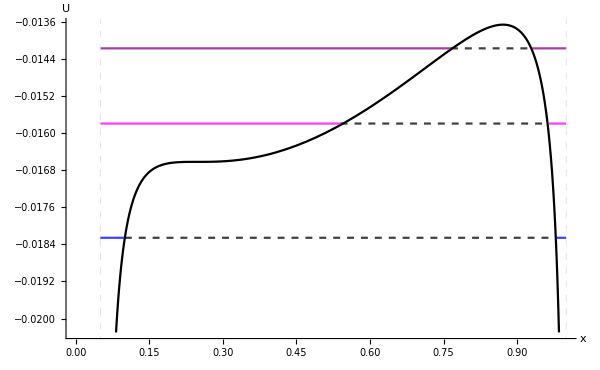

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc2=Show[Uc2,Energyc2,ImageSize->{600,400},BaseStyle->{FontSize->14}]
```

### Final Plot

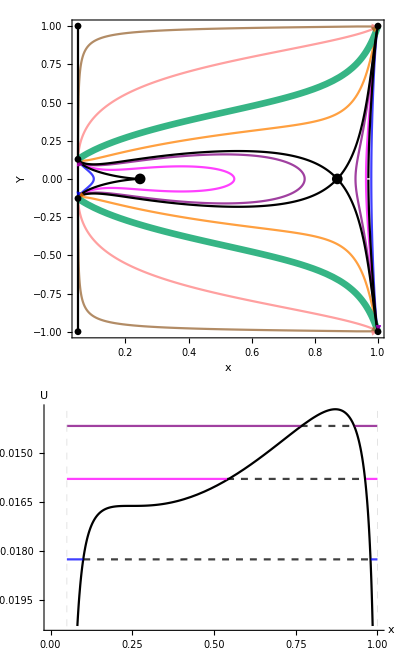

```mathematica
(*Plot the phase space and potential together*)
xYc2=GraphicsColumn[{PhaseSpacec2,Potentialc2},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xY_Plots\\xYc2.pdf",xYc2]*)
```

## Three Einstein Points: c3

```mathematica
(*This is the case where there is an extra bouncing regime*)
```

### Phase Space

```mathematica
(*Trajectories for the phase space*)
(*We plot the trajectories using the first integral (Friedmann equation) rather than the differential equations*)
trajc3[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[3]]/3+v[x,cv]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[3]]/3+v[x0,cv]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Trajectories plotted individually to ensure arrows are pointing in the right direction*)
```

```mathematica
c3traj[1]=ContourPlot[Evaluate[trajc3[0.071,0.08]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[2]=ContourPlot[Evaluate[trajc3[0.071,0.08]],{x,0.2,0.5},{Y,-1,1},PlotPoints->200,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[3]=ContourPlot[Evaluate[trajc3[0.071,0.08]],{x,0.6,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[4]=ContourPlot[Evaluate[trajc3[0.08,0.08]],{x,0,0.8},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[5]=ContourPlot[Evaluate[trajc3[0.08,0.08]],{x,0.8,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[6]=ContourPlot[Evaluate[trajc3[0.04,0.08]],{x,0,0.8},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[7]=ContourPlot[Evaluate[trajc3[0.04,0.08]],{x,0.8,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[8]=ContourPlot[Evaluate[trajc3[0.12,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[9]=ContourPlot[Evaluate[trajc3[0.12,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[10]=ContourPlot[Evaluate[trajc3[0.3,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[11]=ContourPlot[Evaluate[trajc3[0.3,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[12]=ContourPlot[Evaluate[trajc3[0.6,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[13]=ContourPlot[Evaluate[trajc3[0.6,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc3=Table[c3traj[i],{i,1,13}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc3=Plot[{FFS[[3]],-FFS[[3]]},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS curves*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc3=Plot[{CFS[xThreeEinsteinPointsc3][[3]],-CFS[xThreeEinsteinPointsc3][[3]]},{x,0,1},PlotStyle->{Black},PlotRange->Full,PlotPoints->600];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc3=ListPlot[{{xThreeEinsteinPointsc3[[1]],0},{xThreeEinsteinPointsc3[[2]],0},{xThreeEinsteinPointsc3[[3]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc3=ContourPlot[Accn[[3]]==0,{x,0,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

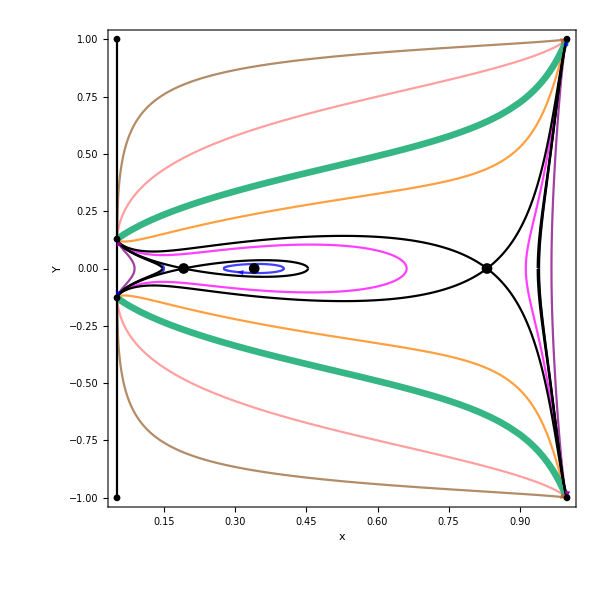

```mathematica
(*Show all components of plots*)
PhaseSpacec3=Show[Trajc3, FFSc3,CFSc3,Einsteinc3,Sep,FPShow,PlotRange->All,FrameLabel->{"x",Rotate["Y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative to find whether point is a maximum or a minimum*)
(*A positive/negative value means it's a minimum/maximum*)
d2Udx2[xThreeEinsteinPointsc3[[1]],0.155][[3]]
```

-0.136796

```mathematica
d2Udx2[xThreeEinsteinPointsc3[[2]],0.155][[3]]
```

0.0402181

```mathematica
d2Udx2[xThreeEinsteinPointsc3[[3]],0.155][[3]]
```

-0.192864

```mathematica
(*Plot the potential for this case*)
Uc3=Plot[{U[x,0.08][[3]]},{x,0,1},AxesLabel->{"x","U"},PlotStyle->{Black},GridLines->{{.05,1},{}},GridLinesStyle->Directive[Thick,Dashed],PlotRange->{-0.016,-0.0105}];
```

```mathematica
c3Energy[1]=Plot[{Energy[0.08,0.071][[3]]},{x,0.05,0.15},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c3Energy[2]=Plot[{Energy[0.08,0.071][[3]]},{x,0.275,0.4},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c3Energy[3]=Plot[{Energy[0.08,0.071][[3]]},{x,0.94,1},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c3Energy[4]=Plot[{Energy[0.08,0.08][[3]]},{x,0.05,0.655},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c3Energy[5]=Plot[{Energy[0.08,0.08][[3]]},{x,0.92,1},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c3Energy[6]=Plot[{Energy[0.08,0.04][[3]]},{x,0.05,0.09},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c3Energy[7]=Plot[{Energy[0.08,0.04][[3]]},{x,0.97,1},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c3Energy[8]=Plot[{Energy[0.08,0.12][[3]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c3Energy[9]=Plot[{Energy[0.08,0.3][[3]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c3Energy[10]=Plot[{Energy[0.08,0.6][[3]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c3Energy[11]=Plot[{0},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c3Energy[12]=Plot[{Energy[0.08,0.071][[3]]},{x,0.15,0.275},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energy[13]=Plot[{Energy[0.08,0.071][[3]]},{x,0.4,0.94},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energy[14]=Plot[{Energy[0.08,0.08][[3]]},{x,0.655,0.92},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energy[15]=Plot[{Energy[0.08,0.04][[3]]},{x,0.09,0.97},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc3=Table[c3Energy[i],{i,1,15}];
```

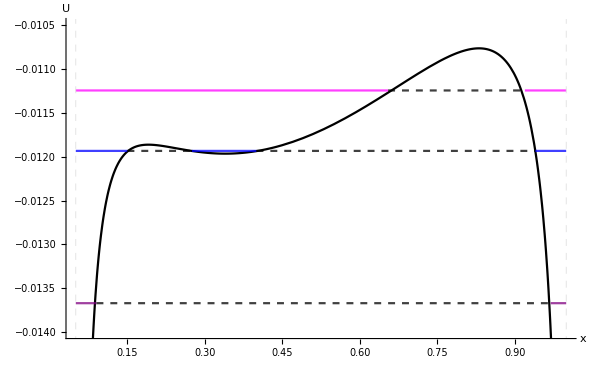

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc3=Show[Uc3,Energyc3,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{-0.014,-0.0105}]
```

### Final Plot

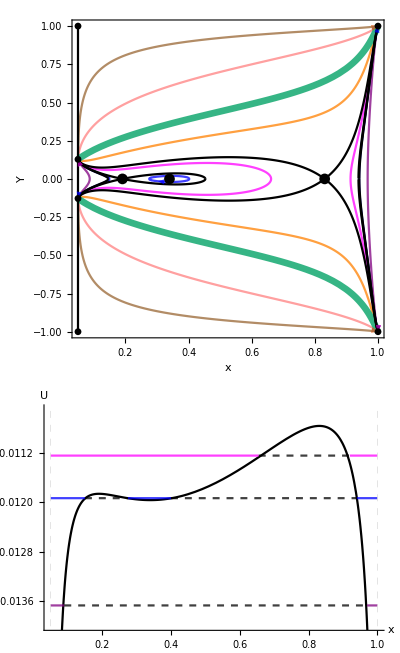

```mathematica
(*Plot the phase space and potential together*)
xYc3=GraphicsColumn[{PhaseSpacec3,Potentialc3},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xY_Plots\\xYc3.pdf",xYc3]*)
```

## Three Einstein Points: c4

```mathematica
(*This is the limiting 3 Einstein point case*)
```

### Phase Space

```mathematica
(*Trajectories for the phase space*)
(*We plot the trajectories using the first integral (Friedmann equation) rather than the differential equations*)
trajc4[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[4]]/3+v[x,cv]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[4]]/3+v[x0,cv]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Trajectories plotted individually to ensure arrows are pointing in the right direction*)
```

```mathematica
c4traj[1]=ContourPlot[Evaluate[trajc4[0.065,0.08]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[2]=ContourPlot[Evaluate[trajc4[0.065,0.08]],{x,0.2,0.7},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[3]=ContourPlot[Evaluate[trajc4[0.065,0.08]],{x,0.7,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[4]=ContourPlot[Evaluate[trajc4[0.05,0.08]],{x,0,0.3},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[5]=ContourPlot[Evaluate[trajc4[0.05,0.08]],{x,0.7,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[6]=ContourPlot[Evaluate[trajc4[0.11,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[7]=ContourPlot[Evaluate[trajc4[0.11,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[8]=ContourPlot[Evaluate[trajc4[0.3,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[9]=ContourPlot[Evaluate[trajc4[0.3,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[10]=ContourPlot[Evaluate[trajc4[0.6,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[11]=ContourPlot[Evaluate[trajc4[0.6,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc4=Table[c4traj[i],{i,1,11}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc4=Plot[{FFS[[4]],-FFS[[4]]},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS curves*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc4=Plot[{CFS[xThreeEinsteinPointsc4][[4]],-CFS[xThreeEinsteinPointsc4][[4]]},{x,0,1},PlotStyle->{Black},PlotRange->Full,PlotPoints->300];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc4=ListPlot[{{xThreeEinsteinPointsc4[[1]],0},{xThreeEinsteinPointsc4[[2]],0},{xThreeEinsteinPointsc4[[3]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc4=ContourPlot[Accn[[4]]==0,{x,0,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

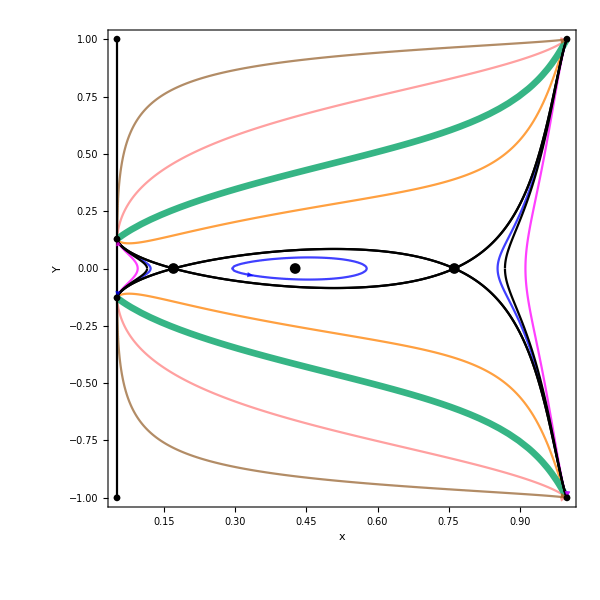

```mathematica
(*Show all components of plots*)
PhaseSpacec4=Show[Trajc4, FFSc4,CFSc4,Einsteinc4,Sep,FPShow,PlotRange->All,FrameLabel->{"x",Rotate["Y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative to find whether point is a maximum or a minimum*)
(*A positive/negative value means it's a minimum/maximum*)
d2Udx2[xThreeEinsteinPointsc4[[1]],0.08][[4]]
```

-0.109509

```mathematica
d2Udx2[xThreeEinsteinPointsc4[[2]],0.08][[4]]
```

0.0143208

```mathematica
d2Udx2[xThreeEinsteinPointsc4[[3]],0.08][[4]]
```

-0.0356306

```mathematica
(*Plot the potential for this case*)
Uc4=Plot[{U[x,0.08][[4]]},{x,0,1},AxesLabel->{"x","U"},PlotStyle->{Black},GridLines->{{.05,1},{}},GridLinesStyle->Directive[Thick,Dashed]];
```

```mathematica
c4Energy[1]=Plot[{Energy[0.08,0.065][[4]]},{x,0.05,0.12},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c4Energy[2]=Plot[{Energy[0.08,0.065][[4]]},{x,0.3,0.57},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c4Energy[3]=Plot[{Energy[0.08,0.065][[4]]},{x,0.855,1},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c4Energy[4]=Plot[{Energy[0.08,0.05][[4]]},{x,0.05,0.095},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c4Energy[5]=Plot[{Energy[0.08,0.05][[4]]},{x,0.91,1},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c4Energy[6]=Plot[{Energy[0.08,0.11][[4]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c4Energy[7]=Plot[{Energy[0.08,0.3][[4]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c4Energy[8]=Plot[{Energy[0.08,0.6][[4]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c4Energy[9]=Plot[{0},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c4Energy[10]=Plot[{Energy[0.08,0.065][[4]]},{x,0.12,0.3},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c4Energy[11]=Plot[{Energy[0.08,0.065][[4]]},{x,0.57,0.855},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c4Energy[12]=Plot[{Energy[0.08,0.05][[4]]},{x,0.095,0.91},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc4=Table[c4Energy[i],{i,1,12}];
```

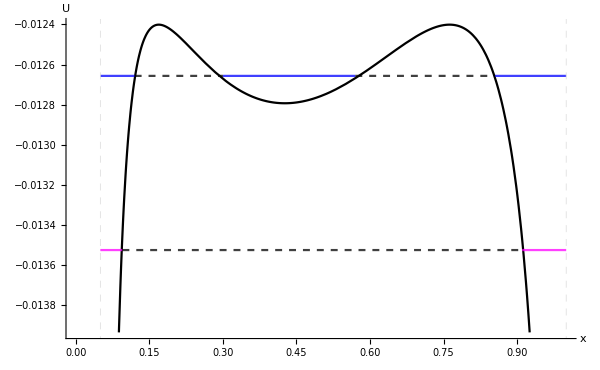

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc4=Show[Uc4,Energyc4,ImageSize->{600,400},BaseStyle->{FontSize->14}]
```

### Final Plot

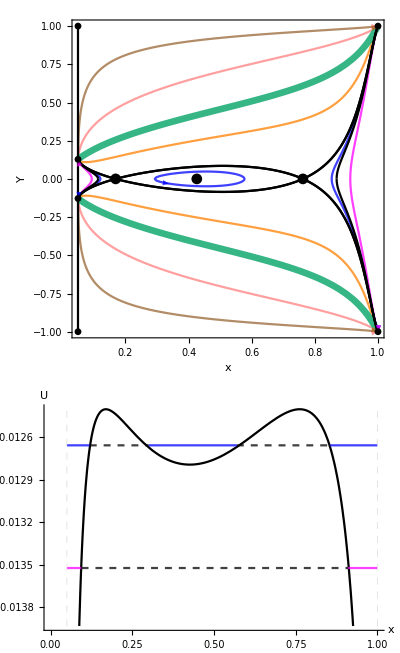

```mathematica
(*Plot the phase space and potential together*)
xYc4=GraphicsColumn[{PhaseSpacec4,Potentialc4},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xY_Plots\\xYc4.pdf",xYc4]*)
```

## Three Einstein Points: c5

```mathematica
(*The case with an extra turn-around region*)
```

### Phase Space

```mathematica
(*Trajectories for the phase space*)
(*We plot the trajectories using the first integral (Friedmann equation) rather than the differential equations*)
trajc5[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[5]]/3+v[x,cv]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[5]]/3+v[x0,cv]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Trajectories plotted individually to ensure arrows are pointing in the right direction*)
```

```mathematica
c5traj[1]=ContourPlot[Evaluate[trajc5[0.06,0.08]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[2]=ContourPlot[Evaluate[trajc5[0.06,0.08]],{x,0.2,0.7},{Y,-1,1},PlotPoints->150,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[3]=ContourPlot[Evaluate[trajc5[0.06,0.08]],{x,0.7,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[4]=ContourPlot[Evaluate[trajc5[0.065,0.08]],{x,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[5]=ContourPlot[Evaluate[trajc5[0.065,0.08]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[6]=ContourPlot[Evaluate[trajc5[0.05,0.08]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[7]=ContourPlot[Evaluate[trajc5[0.05,0.08]],{x,0.7,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[8]=ContourPlot[Evaluate[trajc5[0.11,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[9]=ContourPlot[Evaluate[trajc5[0.11,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[10]=ContourPlot[Evaluate[trajc5[0.3,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[11]=ContourPlot[Evaluate[trajc5[0.3,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[12]=ContourPlot[Evaluate[trajc5[0.6,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[13]=ContourPlot[Evaluate[trajc5[0.6,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc5=Table[c5traj[i],{i,1,13}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc5=Plot[{FFS[[5]],-FFS[[5]]},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS curves*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc5=Plot[{CFS[xThreeEinsteinPointsc5][[5]],-CFS[xThreeEinsteinPointsc5][[5]]},{x,0,1},PlotStyle->{Black},PlotRange->Full,PlotPoints->300];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc5=ListPlot[{{xThreeEinsteinPointsc5[[1]],0},{xThreeEinsteinPointsc5[[2]],0},{xThreeEinsteinPointsc5[[3]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc5=ContourPlot[Accn[[5]]==0,{x,0,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

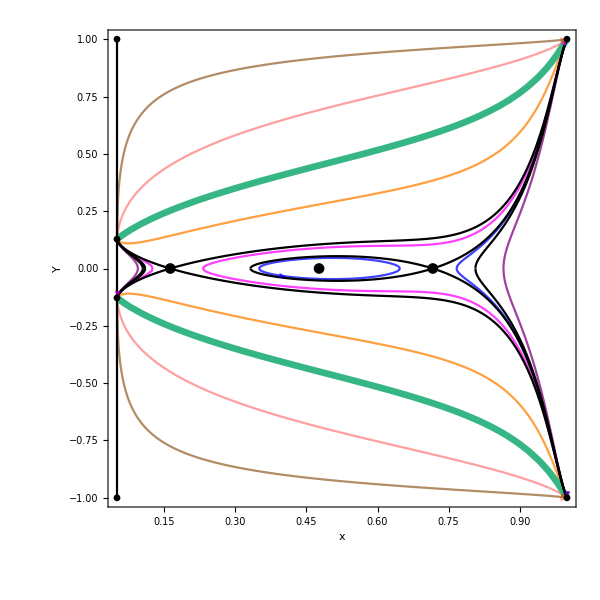

```mathematica
(*Show all components of plots*)
PhaseSpacec5=Show[Trajc5, FFSc5,CFSc5,Einsteinc5,Sep,FPShow,PlotRange->All,FrameLabel->{"x",Rotate["Y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative to find whether point is a maximum or a minimum*)
(*A positive/negative value means it's a minimum/maximum*)
d2Udx2[xThreeEinsteinPointsc5[[1]],0.08][[5]]
```

-0.136758

```mathematica
d2Udx2[xThreeEinsteinPointsc5[[2]],0.08][[5]]
```

0.0114056

```mathematica
d2Udx2[xThreeEinsteinPointsc5[[3]],0.08][[5]]
```

-0.0211506

```mathematica
(*Plot the potential for this case*)
Uc5=Plot[{U[x,0.08][[5]]},{x,0,1},AxesLabel->{"x","U"},PlotStyle->{Black},GridLines->{{.05,1},{}},GridLinesStyle->Directive[Thick,Dashed]];
```

```mathematica
c5Energy[1]=Plot[{Energy[0.08,0.06][[5]]},{x,0.05,0.11},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c5Energy[2]=Plot[{Energy[0.08,0.06][[5]]},{x,0.36,0.625},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c5Energy[3]=Plot[{Energy[0.08,0.06][[5]]},{x,0.78,1},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c5Energy[4]=Plot[{Energy[0.08,0.065][[5]]},{x,0.235,1},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c5Energy[5]=Plot[{Energy[0.08,0.065][[5]]},{x,0.05,0.125},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c5Energy[6]=Plot[{Energy[0.08,0.05][[5]]},{x,0.87,1},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c5Energy[7]=Plot[{Energy[0.08,0.05][[5]]},{x,0.05,0.095},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c5Energy[8]=Plot[{Energy[0.08,0.11][[5]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c5Energy[9]=Plot[{Energy[0.08,0.3][[5]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c5Energy[10]=Plot[{Energy[0.08,0.6][[5]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c5Energy[11]=Plot[{0},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c5Energy[12]=Plot[{Energy[0.08,0.06][[5]]},{x,0.11,0.36},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c5Energy[13]=Plot[{Energy[0.08,0.06][[5]]},{x,0.625,0.78},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c5Energy[14]=Plot[{Energy[0.08,0.065][[5]]},{x,0.125,0.235},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c5Energy[15]=Plot[{Energy[0.08,0.05][[5]]},{x,0.095,0.87},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc5=Table[c5Energy[i],{i,1,15}];
```

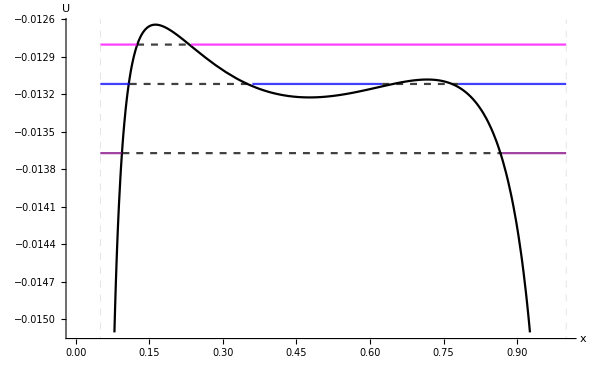

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc5=Show[Uc5,Energyc5,ImageSize->{600,400},BaseStyle->{FontSize->14}]
```

### Final Plot

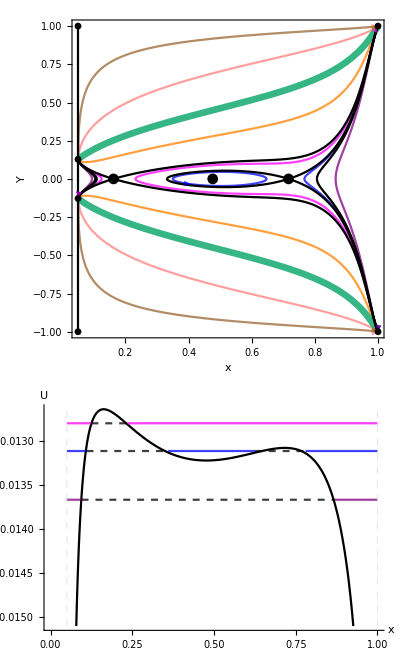

```mathematica
(*Plot the phase space and potential together*)
xYc5=GraphicsColumn[{PhaseSpacec5,Potentialc5},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xY_Plots\\xYc5.pdf",xYc5]*)
```

## Two Einstein Points: c6

### Phase Space

```mathematica
(*Trajectories for the phase space*)
(*We plot the trajectories using the first integral (Friedmann equation) rather than the differential equations*)
trajc6[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[6]]/3+v[x,cv]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[6]]/3+v[x0,cv]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Trajectories plotted individually to ensure arrows are pointing in the right direction*)
```

```mathematica
c6traj[1]=ContourPlot[Evaluate[trajc6[0,0.9]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[2]=ContourPlot[Evaluate[trajc6[0,0.9]],{x,0.6,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[3]=ContourPlot[Evaluate[trajc6[0.4,0.9]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[4]=ContourPlot[Evaluate[trajc6[0.4,0.9]],{x,0.3,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[5]=ContourPlot[Evaluate[trajc6[0.6,0.9]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[6]=ContourPlot[Evaluate[trajc6[0.6,0.9]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[7]=ContourPlot[Evaluate[trajc6[0.9,0.9]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[8]=ContourPlot[Evaluate[trajc6[0.9,0.9]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[9]=ContourPlot[Evaluate[trajc6[0.99,0.9]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[10]=ContourPlot[Evaluate[trajc6[0.99,0.9]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc6=Table[c6traj[i],{i,1,10}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc6=Plot[{FFS[[6]],-FFS[[6]]},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS curves*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc6=Plot[{CFS[xTwoEinsteinPointsc6][[6]],-CFS[xTwoEinsteinPointsc6][[6]]},{x,0,1},PlotStyle->{Black},PlotRange->Full,PlotPoints->500];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc6=ListPlot[{{xTwoEinsteinPointsc6[[1]],0},{xTwoEinsteinPointsc6[[2]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc6=ContourPlot[Accn[[6]]==0,{x,0,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

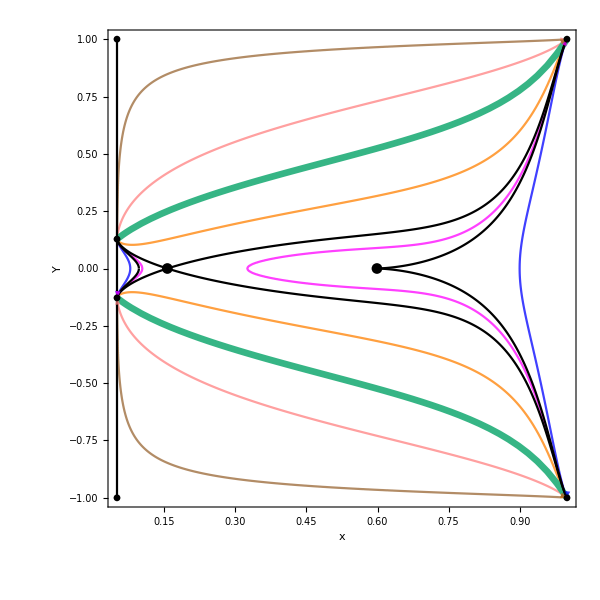

```mathematica
(*Show all components of plots*)
PhaseSpacec6=Show[Trajc6, FFSc6,CFSc6,Einsteinc6,Sep,FPShow,PlotRange->All,FrameLabel->{"x",Rotate["Y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative to find whether point is a maximum or a minimum*)
(*A positive/negative value means it's a minimum/maximum*)
d2Udx2[xTwoEinsteinPointsc6[[1]],0.9][[6]]
```

-8.29826

```mathematica
d2Udx2[xTwoEinsteinPointsc6[[2]],0.9][[6]]
```

-8.28221×10^-8

```mathematica
(*Plot the potential for this case*)
Uc6=Plot[{U[x,0.9][[6]]},{x,0,1},AxesLabel->{"x","U"},PlotStyle->{Black},GridLines->{{.05,1},{}},GridLinesStyle->Directive[Thick,Dashed]];
```

```mathematica
c6Energy[1]=Plot[{Energy[0.9,0][[6]]},{x,0.05,0.07},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c6Energy[2]=Plot[{Energy[0.9,0][[6]]},{x,0.9,1},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c6Energy[3]=Plot[{Energy[0.9,0.4][[6]]},{x,0.05,0.105},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c6Energy[4]=Plot[{Energy[0.9,0.4][[6]]},{x,0.322,1},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c6Energy[5]=Plot[{Energy[0.9,0.6][[6]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c6Energy[6]=Plot[{Energy[0.9,0.9][[6]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Pink,Dashed,Opacity[0.75]}];
```

```mathematica
c6Energy[7]=Plot[{Energy[0.9,0.99][[6]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c6Energy[8]=Plot[{0},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c6Energy[9]=Plot[{Energy[0.9,0][[6]]},{x,0.07,0.9},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c6Energy[10]=Plot[{Energy[0.9,0.4][[6]]},{x,0.105,0.322},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc6=Table[c6Energy[i],{i,1,10}];
```

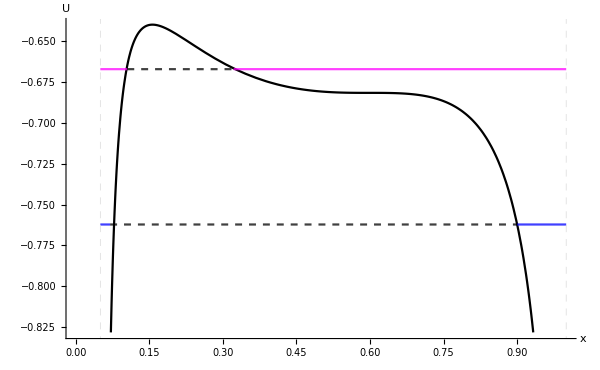

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc6=Show[Uc6,Energyc6,ImageSize->{600,400},BaseStyle->{FontSize->14}]
```

### Final Plot

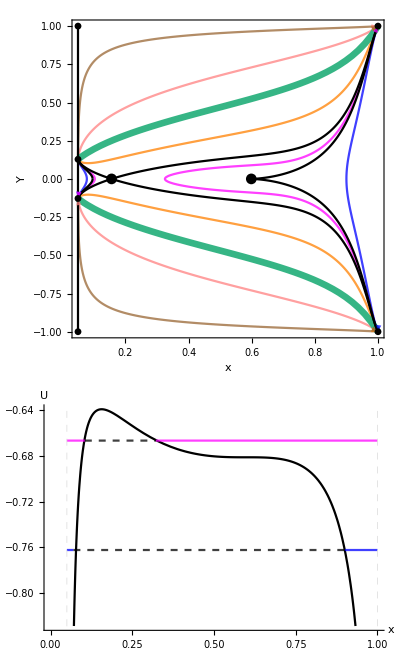

```mathematica
(*Plot the phase space and potential together*)
xYc6=GraphicsColumn[{PhaseSpacec6,Potentialc6},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xY_Plots\\xYc6.pdf",xYc6]*)
```

## One Einstein Point: c7

### Phase Space

```mathematica
(*Trajectories for the phase space*)
(*We plot the trajectories using the first integral (Friedmann equation) rather than the differential equations*)
trajc7[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[7]]/3+v[x,cv]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[7]]/3+v[x0,cv]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Trajectories plotted individually to ensure arrows are pointing in the right direction*)
```

```mathematica
c7traj[1]=ContourPlot[Evaluate[trajc7[0,0.9]],{x,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[2]=ContourPlot[Evaluate[trajc7[0,0.9]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[3]=ContourPlot[Evaluate[trajc7[0.5,0.9]],{x,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[4]=ContourPlot[Evaluate[trajc7[0.5,0.9]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[5]=ContourPlot[Evaluate[trajc7[0.56,0.9]],{x,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[6]=ContourPlot[Evaluate[trajc7[0.56,0.9]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[7]=ContourPlot[Evaluate[trajc7[0.7,0.9]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[8]=ContourPlot[Evaluate[trajc7[0.7,0.9]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[9]=ContourPlot[Evaluate[trajc7[0.92,0.9]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[10]=ContourPlot[Evaluate[trajc7[0.92,0.9]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[11]=ContourPlot[Evaluate[trajc7[0.99,0.9]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[12]=ContourPlot[Evaluate[trajc7[0.99,0.9]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc7=Table[c7traj[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc7=Plot[{FFS[[7]],-FFS[[7]]},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc7=Plot[{CFS[xOneEinsteinPointc7][[7]],-CFS[xOneEinsteinPointc7][[7]]},{x,0,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc7=ListPlot[{{xOneEinsteinPointc7,0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc7=ContourPlot[Accn[[7]]==0,{x,0,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

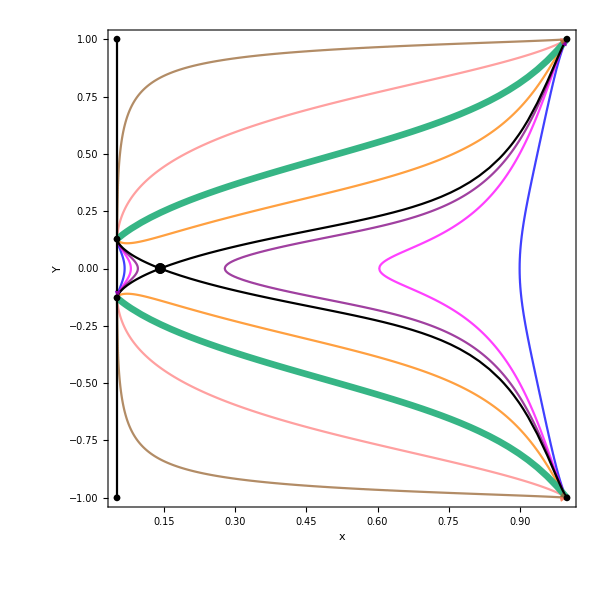

```mathematica
(*Show all components of plots*)
PhaseSpacec7=Show[Trajc7, FFSc7,CFSc7,Einsteinc7,Sep,FPShow,PlotRange->All,FrameLabel->{"x",Rotate["Y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative to find whether point is a maximum or a minimum*)
(*A positive/negative value means it's a minimum/maximum*)
d2Udx2[xOneEinsteinPointc7,0.9][[7]]
```

-13.8623

```mathematica
(*Plot the potential for this case*)
Uc7=Plot[{U[x,0.9][[7]]},{x,0,1},AxesLabel->{"x","U"},PlotStyle->{Black},GridLines->{{.05,1},{}},GridLinesStyle->Directive[Thick,Dashed]];
```

```mathematica
c7Energy[1]=Plot[{Energy[0.9,0][[7]]},{x,0.9,1},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c7Energy[2]=Plot[{Energy[0.9,0][[7]]},{x,0.05,0.06},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c7Energy[3]=Plot[{Energy[0.9,0.5][[7]]},{x,0.6,1},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c7Energy[4]=Plot[{Energy[0.9,0.5][[7]]},{x,0.05,0.08},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c7Energy[5]=Plot[{Energy[0.9,0.56][[7]]},{x,0.275,1},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c7Energy[6]=Plot[{Energy[0.9,0.56][[7]]},{x,0.05,0.099},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c7Energy[7]=Plot[{Energy[0.9,0.7][[7]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c7Energy[8]=Plot[{Energy[0.9,0.92][[7]]},{x,0.2,1},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c7Energy[9]=Plot[{Energy[0.9,0.99][[7]]},{x,0.6,1},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c7Energy[10]=Plot[{0},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c7Energy[11]=Plot[{Energy[0.9,0][[7]]},{x,0.06,0.9},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c7Energy[12]=Plot[{Energy[0.9,0.5][[7]]},{x,0.08,0.6},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c7Energy[13]=Plot[{Energy[0.9,0.56][[7]]},{x,0.099,0.275},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc7=Table[c7Energy[i],{i,1,13}];
```

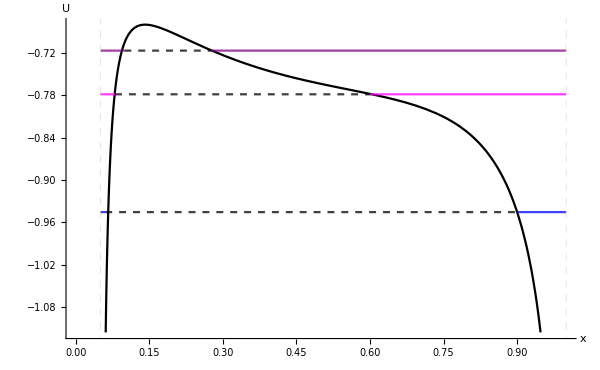

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc7=Show[Uc7,Energyc7,ImageSize->{600,400},BaseStyle->{FontSize->14}]
```

### Final Plot

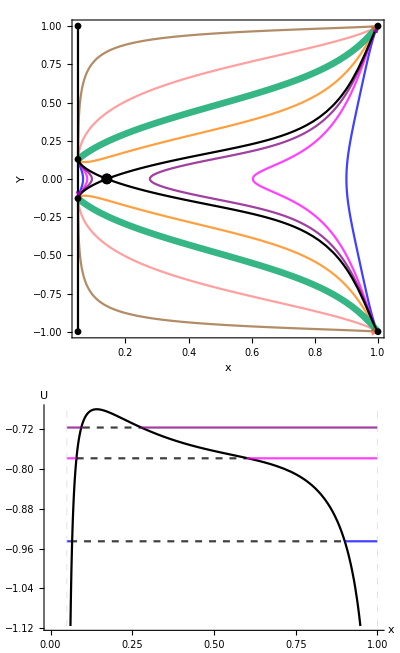

```mathematica
(*Plot the phase space and potential together*)
xYc7=GraphicsColumn[{PhaseSpacec7,Potentialc7},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xY_Plots\\xYc7.pdf",xYc7]*)
```

## 3D x-Y-Z Phase Spaces

## Set-up for x-Y-Z Phase Spaces

```mathematica
(*Use Friedmann equation (first integral) to plot the trajectories*)
(*First define trajc1 = Y^2/(1-Y^2)*)
trajxYZ[Y0_,x0_]:=x/3+z[x,c]/3+v[x,cv]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c]/3+v[x0,cv]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Rearrange above equation for Y*)
trajxYZ[Y0_,x0_]=Sqrt[trajxYZ[Y0,x0]/(1+trajxYZ[Y0,x0])];
```

```mathematica
(*Set up plot for the common fixed points*)
FPShowxYZ=ListPointPlot3D[{{R,-Sqrt[R/(3+R)],0},{R,Sqrt[R/(3+R)],0},{R,1,0},{R,-1,0},{1,1,1},{1,-1,1}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot the surface where accn = 0*)
AccnxYZ=ContourPlot3D[Z/(1-Z)+x+2*v[x,cv]-3*R+3*R*x-3*x^2==0,{x,0,1},{Y,-1,1},{Z,0,1}, ContourStyle->{Red,Opacity[0.3], Thick}];
```

## One Einstein Point: c1

```mathematica
(*Plot the trajectories*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
```

```mathematica
c1trajxYZ[1]=ParametricPlot3D[{x,trajxYZ[0,0.2][[1]],Z[x,c[[1]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[2]=ParametricPlot3D[{x,-trajxYZ[0,0.2][[1]],Z[x,c[[1]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[3]=ParametricPlot3D[{x,trajxYZ[0,0.2][[1]],Z[x,c[[1]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->All]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[4]=ParametricPlot3D[{x,-trajxYZ[0,0.2][[1]],Z[x,c[[1]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->All]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[5]=ParametricPlot3D[{x,trajxYZ[0.12,0.2][[1]],Z[x,c[[1]]]},{x,0,0.8},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[6]=ParametricPlot3D[{x,-trajxYZ[0.12,0.2][[1]],Z[x,c[[1]]]},{x,0,0.8},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[7]=ParametricPlot3D[{x,trajxYZ[0.12,0.2][[1]],Z[x,c[[1]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->All]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[8]=ParametricPlot3D[{x,-trajxYZ[0.12,0.2][[1]],Z[x,c[[1]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->All]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[9]=ParametricPlot3D[{x,trajxYZ[0.18,0.2][[1]],Z[x,c[[1]]]},{x,0,0.9},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->8000]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[10]=ParametricPlot3D[{x,-trajxYZ[0.18,0.2][[1]],Z[x,c[[1]]]},{x,0,0.9},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->8000]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[11]=ParametricPlot3D[{x,trajxYZ[0.18,0.2][[1]],Z[x,c[[1]]]},{x,0.9,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->All]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[12]=ParametricPlot3D[{x,-trajxYZ[0.18,0.2][[1]],Z[x,c[[1]]]},{x,0.9,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->All]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[13]=ParametricPlot3D[{x,trajxYZ[0.225,0.2][[1]],Z[x,c[[1]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[14]=ParametricPlot3D[{x,-trajxYZ[0.225,0.2][[1]],Z[x,c[[1]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[15]=ParametricPlot3D[{x,trajxYZ[0.5,0.2][[1]],Z[x,c[[1]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[16]=ParametricPlot3D[{x,-trajxYZ[0.5,0.2][[1]],Z[x,c[[1]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[17]=ParametricPlot3D[{x,trajxYZ[0.9,0.2][[1]],Z[x,c[[1]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[18]=ParametricPlot3D[{x,-trajxYZ[0.9,0.2][[1]],Z[x,c[[1]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
trajc1=Table[c1trajxYZ[i],{i,1,18}];
```

```mathematica
(*Plot the Einstein fixed points of the system*)
Einsteinc1=ListPointPlot3D[{{xOneEinsteinPointc1,0,ZOneEinsteinPointc1}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot the CFS*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
CFSc1=ParametricPlot3D[{{x,CFS[xOneEinsteinPointc1][[1]],Z[x,c[[1]]]},{x,-CFS[xOneEinsteinPointc1][[1]],Z[x,c[[1]]]}},{x,0,1},PlotStyle->Black,PlotRange->All,PlotPoints->500];
```

```mathematica
(*Flat Friedmann Separatrix*)
(*Two plots needed as sqrt taken for Y part, so + and - parts need plotting separately*)
FFSc1=ParametricPlot3D[{{x,FFS[[1]],Z[x,c[[1]]]},{x,-FFS[[1]],Z[x,c[[1]]]}},{x,0,1},PlotStyle->{RGBColor[0.21,0.71,0.52]},PlotRange->All];
```

```mathematica
(*Plot the c surface*)
Surfacec1=ParametricPlot3D[{x,Y,Z[x,c[[1]]]},{x,0,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
```

```mathematica
xYZc1=Show[CFSc1,FFSc1, Einsteinc1,FPShowxYZ,Surfacec1,trajc1,PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},AxesLabel->{"x","Y","Z"}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xYZ_Plots\\xYZc1.pdf",xYZc1]*)
```

## Two Einstein Points: c2

```mathematica
(*Plot the trajectories*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
```

```mathematica
c2trajxYZ[1]=ParametricPlot3D[{x,trajxYZ[0,0.1][[2]],Z[x,c[[2]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500,AxesLabel->{"Y","x","Z"}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[2]=ParametricPlot3D[{x,-trajxYZ[0,0.1][[2]],Z[x,c[[2]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[3]=ParametricPlot3D[{x,trajxYZ[0,0.1][[2]],Z[x,c[[2]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[4]=ParametricPlot3D[{x,-trajxYZ[0,0.1][[2]],Z[x,c[[2]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[5]=ParametricPlot3D[{x,trajxYZ[0.065,0.1][[2]],Z[x,c[[2]]]},{x,0,0.8},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[6]=ParametricPlot3D[{x,-trajxYZ[0.065,0.1][[2]],Z[x,c[[2]]]},{x,0,0.8},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[7]=ParametricPlot3D[{x,trajxYZ[0.065,0.1][[2]],Z[x,c[[2]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[8]=ParametricPlot3D[{x,-trajxYZ[0.065,0.1][[2]],Z[x,c[[2]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[9]=ParametricPlot3D[{x,trajxYZ[0.085,0.1][[2]],Z[x,c[[2]]]},{x,0,0.8},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[10]=ParametricPlot3D[{x,-trajxYZ[0.085,0.1][[2]],Z[x,c[[2]]]},{x,0,0.8},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[11]=ParametricPlot3D[{x,trajxYZ[0.085,0.1][[2]],Z[x,c[[2]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[12]=ParametricPlot3D[{x,-trajxYZ[0.085,0.1][[2]],Z[x,c[[2]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[13]=ParametricPlot3D[{x,trajxYZ[0.13,0.1][[2]],Z[x,c[[2]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[14]=ParametricPlot3D[{x,-trajxYZ[0.13,0.1][[2]],Z[x,c[[2]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[15]=ParametricPlot3D[{x,trajxYZ[0.4,0.1][[2]],Z[x,c[[2]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[16]=ParametricPlot3D[{x,-trajxYZ[0.4,0.1][[2]],Z[x,c[[2]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[17]=ParametricPlot3D[{x,trajxYZ[0.9,0.1][[2]],Z[x,c[[2]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[18]=ParametricPlot3D[{x,-trajxYZ[0.9,0.1][[2]],Z[x,c[[2]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
trajc2=Table[c2trajxYZ[i],{i,1,18}];
```

```mathematica
(*Plot the Einstein fixed points of the system*)
Einsteinc2=ListPointPlot3D[{{xTwoEinsteinPointsc2[[1]],0,ZTwoEinsteinPointsc2[[1]]},{xTwoEinsteinPointsc2[[2]],0,ZTwoEinsteinPointsc2[[2]]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot the CFS*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
CFSc2=ParametricPlot3D[{{x,CFS[xTwoEinsteinPointsc2[[1]]][[2]],Z[x,c[[2]]]},{x,-CFS[xTwoEinsteinPointsc2[[1]]][[2]],Z[x,c[[2]]]},{x,CFS[xTwoEinsteinPointsc2[[2]]][[2]],Z[x,c[[2]]]},{x,-CFS[xTwoEinsteinPointsc2[[2]]][[2]],Z[x,c[[2]]]}},{x,0,1},PlotStyle->Black,PlotRange->All,PlotPoints->500];
```

```mathematica
(*Flat Friedmann Separatrix*)
(*Two plots needed as sqrt taken for Y part, so + and - parts need plotting separately*)
FFSc2=ParametricPlot3D[{{x,FFS[[2]],Z[x,c[[2]]]},{x,-FFS[[2]],Z[x,c[[2]]]}},{x,0,1},PlotStyle->{RGBColor[0.21,0.71,0.52]},PlotRange->All];
```

```mathematica
(*Plot the c surface*)
Surfacec2=ParametricPlot3D[{x,Y,Z[x,c[[2]]]},{x,0,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
```

```mathematica
xYZc2=Show[CFSc2,FFSc2, Einsteinc2,FPShowxYZ,Surfacec2,trajc2,PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},AxesLabel->{"x","Y","Z"}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xYZ_Plots\\xYZc2.pdf",xYZc2]*)
```

## Three Einstein Points: c3

```mathematica
(*Plot the trajectories*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
```

```mathematica
c3trajxYZ[1]=ParametricPlot3D[{x,trajxYZ[0.071,0.08][[3]],Z[x,c[[3]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500,AxesLabel->{"Y","x","Z"}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[2]=ParametricPlot3D[{x,-trajxYZ[0.071,0.08][[3]],Z[x,c[[3]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[3]=ParametricPlot3D[{x,trajxYZ[0.071,0.08][[3]],Z[x,c[[3]]]},{x,0.2,0.5},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[4]=ParametricPlot3D[{x,-trajxYZ[0.071,0.08][[3]],Z[x,c[[3]]]},{x,0.2,0.5},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[5]=ParametricPlot3D[{x,trajxYZ[0.071,0.08][[3]],Z[x,c[[3]]]},{x,0.6,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[6]=ParametricPlot3D[{x,-trajxYZ[0.071,0.08][[3]],Z[x,c[[3]]]},{x,0.6,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[7]=ParametricPlot3D[{x,trajxYZ[0.08,0.08][[3]],Z[x,c[[3]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[8]=ParametricPlot3D[{x,-trajxYZ[0.08,0.08][[3]],Z[x,c[[3]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[9]=ParametricPlot3D[{x,trajxYZ[0.04,0.08][[3]],Z[x,c[[3]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[10]=ParametricPlot3D[{x,-trajxYZ[0.04,0.08][[3]],Z[x,c[[3]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[11]=ParametricPlot3D[{x,trajxYZ[0.12,0.08][[3]],Z[x,c[[3]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[12]=ParametricPlot3D[{x,-trajxYZ[0.12,0.08][[3]],Z[x,c[[3]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[13]=ParametricPlot3D[{x,trajxYZ[0.3,0.08][[3]],Z[x,c[[3]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[14]=ParametricPlot3D[{x,-trajxYZ[0.3,0.08][[3]],Z[x,c[[3]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[15]=ParametricPlot3D[{x,trajxYZ[0.6,0.08][[3]],Z[x,c[[3]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[16]=ParametricPlot3D[{x,-trajxYZ[0.6,0.08][[3]],Z[x,c[[3]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
trajc3=Table[c3trajxYZ[i],{i,1,16}];
```

```mathematica
(*Plot the Einstein fixed points of the system*)
Einsteinc3=ListPointPlot3D[{{xThreeEinsteinPointsc3[[1]],0,ZThreeEinsteinPointsc3[[1]]},{xThreeEinsteinPointsc3[[2]],0,ZThreeEinsteinPointsc3[[2]]},{xThreeEinsteinPointsc3[[3]],0,ZThreeEinsteinPointsc3[[3]]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot the CFS*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
CFSc3=ParametricPlot3D[{{x,CFS[xThreeEinsteinPointsc3[[1]]][[3]],Z[x,c[[3]]]},{x,-CFS[xThreeEinsteinPointsc3[[1]]][[3]],Z[x,c[[3]]]},{x,CFS[xThreeEinsteinPointsc3[[2]]][[3]],Z[x,c[[3]]]},{x,-CFS[xThreeEinsteinPointsc3[[2]]][[3]],Z[x,c[[3]]]},{x,CFS[xThreeEinsteinPointsc3[[3]]][[3]],Z[x,c[[3]]]},{x,-CFS[xThreeEinsteinPointsc3[[3]]][[3]],Z[x,c[[3]]]}},{x,0,1},PlotStyle->Black,PlotRange->All,PlotPoints->500];
```

```mathematica
(*Flat Friedmann Separatrix*)
(*Two plots needed as sqrt taken for Y part, so + and - parts need plotting separately*)
FFSc3=ParametricPlot3D[{{x,FFS[[3]],Z[x,c[[3]]]},{x,-FFS[[3]],Z[x,c[[3]]]}},{x,0,1},PlotStyle->{RGBColor[0.21,0.71,0.52]},PlotRange->All];
```

```mathematica
(*Plot the c surface*)
Surfacec3=ParametricPlot3D[{x,Y,Z[x,c[[3]]]},{x,0,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
```

```mathematica
xYZc3=Show[CFSc3,FFSc3, Einsteinc3,FPShowxYZ,Surfacec3,trajc3,PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},AxesLabel->{"x","Y","Z"}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xYZ_Plots\\xYZc3.pdf",xYZc3]*)
```

## Three Einstein Points: c4

```mathematica
(*Plot the trajectories*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
```

```mathematica
(*Plotting trajectories with different values of k*)
c4trajxYZ[1]=ParametricPlot3D[{x,trajxYZ[0.065,0.08][[4]],Z[x,c[[4]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500,AxesLabel->{"Y","x","Z"}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[2]=ParametricPlot3D[{x,-trajxYZ[0.065,0.08][[4]],Z[x,c[[4]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500,AxesLabel->{"Y","x","Z"}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[3]=ParametricPlot3D[{x,-trajxYZ[0.065,0.08][[4]],Z[x,c[[4]]]},{x,0.2,0.7},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[4]=ParametricPlot3D[{x,trajxYZ[0.065,0.08][[4]],Z[x,c[[4]]]},{x,0.2,0.7},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[5]=ParametricPlot3D[{x,trajxYZ[0.065,0.08][[4]],Z[x,c[[4]]]},{x,0.7,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[6]=ParametricPlot3D[{x,-trajxYZ[0.065,0.08][[4]],Z[x,c[[4]]]},{x,0.7,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[7]=ParametricPlot3D[{x,trajxYZ[0.05,0.08][[4]],Z[x,c[[4]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[8]=ParametricPlot3D[{x,-trajxYZ[0.05,0.08][[4]],Z[x,c[[4]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[9]=ParametricPlot3D[{x,-trajxYZ[0.11,0.08][[4]],Z[x,c[[4]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[10]=ParametricPlot3D[{x,trajxYZ[0.11,0.08][[4]],Z[x,c[[4]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[11]=ParametricPlot3D[{x,-trajxYZ[0.3,0.08][[4]],Z[x,c[[4]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[12]=ParametricPlot3D[{x,trajxYZ[0.3,0.08][[4]],Z[x,c[[4]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[13]=ParametricPlot3D[{x,-trajxYZ[0.6,0.08][[4]],Z[x,c[[4]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[14]=ParametricPlot3D[{x,trajxYZ[0.6,0.08][[4]],Z[x,c[[4]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajc4=Table[c4trajxYZ[i],{i,1,14}];
```

```mathematica
(*Plot the Einstein fixed points of the system*)
Einsteinc4=ListPointPlot3D[{{xThreeEinsteinPointsc4[[1]],0,ZThreeEinsteinPointsc4[[1]]},{xThreeEinsteinPointsc4[[2]],0,ZThreeEinsteinPointsc4[[2]]},{xThreeEinsteinPointsc4[[3]],0,ZThreeEinsteinPointsc4[[3]]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot the CFS*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
CFSc4=ParametricPlot3D[{{x,CFS[xThreeEinsteinPointsc4[[1]]][[4]],Z[x,c[[4]]]},{x,-CFS[xThreeEinsteinPointsc4[[1]]][[4]],Z[x,c[[4]]]},{x,CFS[xThreeEinsteinPointsc4[[2]]][[4]],Z[x,c[[4]]]},{x,-CFS[xThreeEinsteinPointsc4[[2]]][[4]],Z[x,c[[4]]]},{x,CFS[xThreeEinsteinPointsc4[[3]]][[4]],Z[x,c[[4]]]},{x,-CFS[xThreeEinsteinPointsc4[[3]]][[4]],Z[x,c[[4]]]}},{x,0,1},PlotStyle->Black,PlotRange->All,PlotPoints->500];
```

```mathematica
(*Flat Friedmann Separatrix*)
(*Two plots needed as sqrt taken for Y part, so + and - parts need plotting separately*)
FFSc4=ParametricPlot3D[{{x,FFS[[4]],Z[x,c[[4]]]},{x,-FFS[[4]],Z[x,c[[4]]]}},{x,0,1},PlotStyle->{RGBColor[0.21,0.71,0.52]},PlotRange->All];
```

```mathematica
(*Plot the c surface*)
Surfacec4=ParametricPlot3D[{x,Y,Z[x,c[[4]]]},{x,0,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
```

```mathematica
xYZc4=Show[CFSc4,FFSc4, Einsteinc4,FPShowxYZ,Surfacec4,trajc4,PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},AxesLabel->{"x","Y","Z"}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xYZ_Plots\\xYZc4.pdf",xYZc4]*)
```

## Three Einstein Points: c5

```mathematica
(*Plot the trajectories*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
```

```mathematica
(*Plotting trajectories with different values of k*)
c5trajxYZ[1]=ParametricPlot3D[{x,trajxYZ[0.06,0.08][[5]],Z[x,c[[5]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500,AxesLabel->{"Y","x","Z"}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[2]=ParametricPlot3D[{x,-trajxYZ[0.06,0.08][[5]],Z[x,c[[5]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[3]=ParametricPlot3D[{x,trajxYZ[0.06,0.08][[5]],Z[x,c[[5]]]},{x,0.2,0.7},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[4]=ParametricPlot3D[{x,-trajxYZ[0.06,0.08][[5]],Z[x,c[[5]]]},{x,0.2,0.7},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[5]=ParametricPlot3D[{x,trajxYZ[0.06,0.08][[5]],Z[x,c[[5]]]},{x,0.7,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[6]=ParametricPlot3D[{x,-trajxYZ[0.06,0.08][[5]],Z[x,c[[5]]]},{x,0.7,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[7]=ParametricPlot3D[{x,trajxYZ[0.065,0.08][[5]],Z[x,c[[5]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[8]=ParametricPlot3D[{x,-trajxYZ[0.065,0.08][[5]],Z[x,c[[5]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[9]=ParametricPlot3D[{x,trajxYZ[0.05,0.08][[5]],Z[x,c[[5]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[10]=ParametricPlot3D[{x,-trajxYZ[0.05,0.08][[5]],Z[x,c[[5]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[11]=ParametricPlot3D[{x,trajxYZ[0.11,0.08][[5]],Z[x,c[[5]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[12]=ParametricPlot3D[{x,-trajxYZ[0.11,0.08][[5]],Z[x,c[[5]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[13]=ParametricPlot3D[{x,trajxYZ[0.3,0.08][[5]],Z[x,c[[5]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[14]=ParametricPlot3D[{x,-trajxYZ[0.3,0.08][[5]],Z[x,c[[5]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[15]=ParametricPlot3D[{x,trajxYZ[0.6,0.08][[5]],Z[x,c[[5]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[16]=ParametricPlot3D[{x,-trajxYZ[0.6,0.08][[5]],Z[x,c[[5]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajc5=Table[c5trajxYZ[i],{i,1,16}];
```

```mathematica
(*Plot the Einstein fixed points of the system*)
Einsteinc5=ListPointPlot3D[{{xThreeEinsteinPointsc5[[1]],0,ZThreeEinsteinPointsc5[[1]]},{xThreeEinsteinPointsc5[[2]],0,ZThreeEinsteinPointsc5[[2]]},{xThreeEinsteinPointsc5[[3]],0,ZThreeEinsteinPointsc5[[3]]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot the CFS*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
CFSc5=ParametricPlot3D[{{x,CFS[xThreeEinsteinPointsc5[[1]]][[5]],Z[x,c[[5]]]},{x,-CFS[xThreeEinsteinPointsc5[[1]]][[5]],Z[x,c[[5]]]},{x,CFS[xThreeEinsteinPointsc5[[2]]][[5]],Z[x,c[[5]]]},{x,-CFS[xThreeEinsteinPointsc5[[2]]][[5]],Z[x,c[[5]]]},{x,CFS[xThreeEinsteinPointsc5[[3]]][[5]],Z[x,c[[5]]]},{x,-CFS[xThreeEinsteinPointsc5[[3]]][[5]],Z[x,c[[5]]]}},{x,0,1},PlotStyle->Black,PlotRange->All,PlotPoints->500];
```

```mathematica
(*Flat Friedmann Separatrix*)
(*Two plots needed as sqrt taken for Y part, so + and - parts need plotting separately*)
FFSc5=ParametricPlot3D[{{x,FFS[[5]],Z[x,c[[5]]]},{x,-FFS[[5]],Z[x,c[[5]]]}},{x,0,1},PlotStyle->{RGBColor[0.21,0.71,0.52]},PlotRange->All];
```

```mathematica
(*Plot the c surface*)
Surfacec5=ParametricPlot3D[{x,Y,Z[x,c[[5]]]},{x,0,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
```

```mathematica
xYZc5=Show[CFSc5,FFSc5, Einsteinc5,FPShowxYZ,Surfacec5,trajc5,PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},AxesLabel->{"x","Y","Z"}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xYZ_Plots\\xYZc5.pdf",xYZc5]*)
```

## Two Einstein Points: c6

```mathematica
(*Plot the trajectories*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
```

```mathematica
c6trajxYZ[1]=ParametricPlot3D[{x,trajxYZ[0,0.9][[6]],Z[x,c[[6]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[2]=ParametricPlot3D[{x,-trajxYZ[0,0.9][[6]],Z[x,c[[6]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[3]=ParametricPlot3D[{x,trajxYZ[0,0.9][[6]],Z[x,c[[6]]]},{x,0.6,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[4]=ParametricPlot3D[{x,-trajxYZ[0,0.9][[6]],Z[x,c[[6]]]},{x,0.6,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[5]=ParametricPlot3D[{x,trajxYZ[0.4,0.9][[6]],Z[x,c[[6]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[6]=ParametricPlot3D[{x,-trajxYZ[0.4,0.9][[6]],Z[x,c[[6]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[7]=ParametricPlot3D[{x,trajxYZ[0.4,0.9][[6]],Z[x,c[[6]]]},{x,0.2,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[8]=ParametricPlot3D[{x,-trajxYZ[0.4,0.9][[6]],Z[x,c[[6]]]},{x,0.2,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[9]=ParametricPlot3D[{x,trajxYZ[0.6,0.9][[6]],Z[x,c[[6]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[10]=ParametricPlot3D[{x,-trajxYZ[0.6,0.9][[6]],Z[x,c[[6]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[11]=ParametricPlot3D[{x,trajxYZ[0.9,0.9][[6]],Z[x,c[[6]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[12]=ParametricPlot3D[{x,-trajxYZ[0.9,0.9][[6]],Z[x,c[[6]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[13]=ParametricPlot3D[{x,trajxYZ[0.99,0.9][[6]],Z[x,c[[6]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[14]=ParametricPlot3D[{x,-trajxYZ[0.99,0.9][[6]],Z[x,c[[6]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
trajc6=Table[c6trajxYZ[i],{i,1,14}];
```

```mathematica
(*Plot the Einstein fixed points of the system*)
Einsteinc6=ListPointPlot3D[{{xTwoEinsteinPointsc6[[1]],0,ZTwoEinsteinPointsc6[[1]]},{xTwoEinsteinPointsc6[[2]],0,ZTwoEinsteinPointsc6[[2]]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot the CFS*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
CFSc6=ParametricPlot3D[{{x,CFS[xTwoEinsteinPointsc6[[1]]][[6]],Z[x,c[[6]]]},{x,-CFS[xTwoEinsteinPointsc6[[1]]][[6]],Z[x,c[[6]]]},{x,CFS[xTwoEinsteinPointsc6[[2]]][[6]],Z[x,c[[6]]]},{x,-CFS[xTwoEinsteinPointsc6[[2]]][[6]],Z[x,c[[6]]]}},{x,0,1},PlotStyle->Black,PlotRange->All,PlotPoints->500];
```

```mathematica
(*Flat Friedmann Separatrix*)
(*Two plots needed as sqrt taken for Y part, so + and - parts need plotting separately*)
FFSc6=ParametricPlot3D[{{x,FFS[[6]],Z[x,c[[6]]]},{x,-FFS[[6]],Z[x,c[[6]]]}},{x,0,1},PlotStyle->{RGBColor[0.21,0.71,0.52]},PlotRange->All];
```

```mathematica
(*Plot the c surface*)
Surfacec6=ParametricPlot3D[{x,Y,Z[x,c[[6]]]},{x,0,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
```

```mathematica
xYZc6=Show[CFSc6,FFSc6, Einsteinc6,FPShowxYZ,Surfacec6,trajc6,PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},AxesLabel->{"x","Y","Z"}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xYZ_Plots\\xYZc6.pdf",xYZc6]*)
```

## One Einstein Point: c7

```mathematica
(*Plot the trajectories*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
```

```mathematica
c7trajxYZ[1]=ParametricPlot3D[{x,trajxYZ[0,0.9][[7]],Z[x,c[[7]]]},{x,0.2,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[2]=ParametricPlot3D[{x,-trajxYZ[0,0.9][[7]],Z[x,c[[7]]]},{x,0.2,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[3]=ParametricPlot3D[{x,trajxYZ[0,0.9][[7]],Z[x,c[[7]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[4]=ParametricPlot3D[{x,-trajxYZ[0,0.9][[7]],Z[x,c[[7]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[5]=ParametricPlot3D[{x,trajxYZ[0.5,0.9][[7]],Z[x,c[[7]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[6]=ParametricPlot3D[{x,-trajxYZ[0.5,0.9][[7]],Z[x,c[[7]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[7]=ParametricPlot3D[{x,trajxYZ[0.5,0.9][[7]],Z[x,c[[7]]]},{x,0.2,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[8]=ParametricPlot3D[{x,-trajxYZ[0.5,0.9][[7]],Z[x,c[[7]]]},{x,0.2,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[9]=ParametricPlot3D[{x,trajxYZ[0.56,0.9][[7]],Z[x,c[[7]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[10]=ParametricPlot3D[{x,-trajxYZ[0.56,0.9][[7]],Z[x,c[[7]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[11]=ParametricPlot3D[{x,trajxYZ[0.56,0.9][[7]],Z[x,c[[7]]]},{x,0.2,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[12]=ParametricPlot3D[{x,-trajxYZ[0.56,0.9][[7]],Z[x,c[[7]]]},{x,0.2,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[13]=ParametricPlot3D[{x,trajxYZ[0.7,0.9][[7]],Z[x,c[[7]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[14]=ParametricPlot3D[{x,-trajxYZ[0.7,0.9][[7]],Z[x,c[[7]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[15]=ParametricPlot3D[{x,trajxYZ[0.92,0.9][[7]],Z[x,c[[7]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[16]=ParametricPlot3D[{x,-trajxYZ[0.92,0.9][[7]],Z[x,c[[7]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[17]=ParametricPlot3D[{x,trajxYZ[0.99,0.9][[7]],Z[x,c[[7]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[18]=ParametricPlot3D[{x,-trajxYZ[0.99,0.9][[7]],Z[x,c[[7]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
trajc7=Table[c7trajxYZ[i],{i,1,18}];
```

```mathematica
(*Plot the Einstein fixed points of the system*)
Einsteinc7=ListPointPlot3D[{{xOneEinsteinPointc7,0,ZOneEinsteinPointc7}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot the CFS*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
CFSc7=ParametricPlot3D[{{x,CFS[xOneEinsteinPointc7][[7]],Z[x,c[[7]]]},{x,-CFS[xOneEinsteinPointc7][[7]],Z[x,c[[7]]]}},{x,0,1},PlotStyle->Black,PlotRange->All,PlotPoints->500];
```

```mathematica
(*Flat Friedmann Separatrix*)
(*Two plots needed as sqrt taken for Y part, so + and - parts need plotting separately*)
FFSc7=ParametricPlot3D[{{x,FFS[[7]],Z[x,c[[7]]]},{x,-FFS[[7]],Z[x,c[[7]]]}},{x,0,1},PlotStyle->{RGBColor[0.21,0.71,0.52]},PlotRange->All];
```

```mathematica
(*Plot the c surface*)
Surfacec7=ParametricPlot3D[{x,Y,Z[x,c[[7]]]},{x,0,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
```

```mathematica
xYZc7=Show[CFSc7,FFSc7, Einsteinc7,FPShowxYZ,Surfacec7,trajc7,PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},AxesLabel->{"x","Y","Z"}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xYZ_Plots\\xYZc7.pdf",xYZc7]*)
```

## a-y Phase Spaces and Potentials

## Set-up

### Variables in terms of a

```mathematica
(*Dark matter (z), radiation (v) and dark energy x written in terms of the scale factor a*)
xa[a_,x0_]=(a^(-3*(1-R))+ca[x0]*R)/(a^(-3*(1-R))+ca[x0]);

za[a_,x0_,c_]=c*((xa[a,x0]-R)/(1-xa[a,x0]))^(1/(1-R));

va[a_,x0_,cv_]=cv*((xa[a,x0]-R)/(1-xa[a,x0]))^(4/(3*(1-R)));
```

```mathematica
(*Define w(a), the resulting term left in y' when y = 0, which needs to be solved to find the Einstein fixed points*)
(*When w = 0, there is an Einstein fixed point*)
wa[a_,x0_,c_,cv_]=za[a,x0,c]+2*va[a,x0,cv]-3*R+xa[a,x0]*(1+3*R)-3*xa[a,x0]^2;
```

### Phase Spaces

```mathematica
(*Define the Flat Friedmann Separatrix (FFS)*)
(*Define ffs = y^2*)
ffsay[a_,x0_]=(1/3)*(xa[a,x0]+za[a,x0,c]+va[a,x0,cv]);
```

```mathematica
(*Rearrange for y*)
FFSay[a_,x0_]=Sqrt[ffsay[a,x0]];
```

```mathematica
(*Define the Closed Friedmann Separatrix (CFS)*)
(*Define cfs = y^2*)
(*aE denotes the a value of the Einstein fixed point*)
cfsay[a_,aE_,x0_]= xa[a,x0]/3+za[a,x0,c]/3+va[a,x0,cv]/3-((aE/a)^2)*(xa[aE,x0]/3+za[aE,x0,c]/3+va[aE,x0,cv]/3);
```

```mathematica
(*Rearrange above equation for y*)
CFSay[a_,aE_,x0_]=Sqrt[cfsay[a,aE,x0]];
```

```mathematica
(*Define the acceleration*)
Accnay=za[a,x0,c]+x+2*va[a,x0,cv]-3*R+3*R*xa[a,x0]-3*xa[a,x0]^2;
```

### Potentials

```mathematica
(*a0 = 1 today*)
a0=1;
```

```mathematica
(*Define the potential*)
Uay[a_,x0_]=-(a^2/6)*(xa[a,x0]+za[a,x0,c]+va[a,x0,cv]);
```

```mathematica
(*Define the energy of the trajectories from the phase space*)
Energyay[x0_,y0_]=-(xa[a0,x0]/6+za[a0,x0,c]/6+va[a0,x0,cv]/6-y0^2/2);
```

## Find the Einstein Points in Each Case

```mathematica
(*Numerically solve w = 0 to find the Einstein fixed points in each case*)
(*FindRoot is a Newtonian approximation*)
```

### One Einstein Point: c1

```mathematica
aOneEinsteinPointc1=FindRoot[wa[a,0.2,c,cv][[1]]==0,{a,0.2}]
```

{a→0.172295}

```mathematica
(*Remove the arrow from the solution above*)
aOneEinsteinPointc1=a/.aOneEinsteinPointc1
```

0.172295

### Two Einstein Points: c2 (1st Limiting Case)

```mathematica
aTwoEinsteinPointsc2i=FindRoot[wa[a,0.1,c,cv][[2]]==0,{a,0.1}];
aTwoEinsteinPointsc2ii=FindRoot[wa[a,0.1,c,cv][[2]]==0,{a,0.9}];
```

```mathematica
(*Put the Einstein points into one variable name for this case*)
aTwoEinsteinPointsc2={a/.aTwoEinsteinPointsc2i,a/.aTwoEinsteinPointsc2ii}
```

{0.189406,0.580945}

### Three Einstein Points: c3

```mathematica
aThreeEinsteinPointsc3i=FindRoot[wa[a,0.08,c,cv][[3]]==0,{a,0.1}];
aThreeEinsteinPointsc3ii=FindRoot[wa[a,0.08,c,cv][[3]]==0,{a,0.4}];
aThreeEinsteinPointsc3iii=FindRoot[wa[a,0.08,c,cv][[3]]==0,{a,0.9}];
```

```mathematica
(*Put the Einstein points into one variable name for this case*)
aThreeEinsteinPointsc3={a/.aThreeEinsteinPointsc3i,a/.aThreeEinsteinPointsc3ii,a/.aThreeEinsteinPointsc3iii}
```

{0.175793,0.401739,0.555757}

### Three Einstein Points: c4

```mathematica
aThreeEinsteinPointsc4i=FindRoot[wa[a,0.08,c,cv][[4]]==0,{a,0.1}];
aThreeEinsteinPointsc4ii=FindRoot[wa[a,0.08,c,cv][[4]]==0,{a,0.4}];
aThreeEinsteinPointsc4iii=FindRoot[wa[a,0.08,c,cv][[4]]==0,{a,0.6}];
```

```mathematica
(*Put the Einstein points into one variable name for this case*)
aThreeEinsteinPointsc4={a/.aThreeEinsteinPointsc4i,a/.aThreeEinsteinPointsc4ii,a/.aThreeEinsteinPointsc4iii}
```

{0.204752,0.348904,0.594593}

### Three Einstein Points: c5

```mathematica
aThreeEinsteinPointsc5i=FindRoot[wa[a,0.08,c,cv][[5]]==0,{a,0.1}];
aThreeEinsteinPointsc5ii=FindRoot[wa[a,0.08,c,cv][[5]]==0,{a,0.4}];
aThreeEinsteinPointsc5iii=FindRoot[wa[a,0.08,c,cv][[5]]==0,{a,0.6}];
```

```mathematica
(*Put the Einstein points into one variable name for this case*)
aThreeEinsteinPointsc5={a/.aThreeEinsteinPointsc5i,a/.aThreeEinsteinPointsc5ii,a/.aThreeEinsteinPointsc5iii}
```

{0.222807,0.323219,0.608681}

### Two Einstein Points: c6 (2nd Limiting Case)

```mathematica
aTwoEinsteinPointsc6i=FindRoot[wa[a,0.9,c,cv][[6]]==0,{a,2}];
aTwoEinsteinPointsc6ii=FindRoot[wa[a,0.9,c,cv][[6]]==0,{a,6}];
```

```mathematica
(*Put the Einstein points into one variable name for this case*)
aTwoEinsteinPointsc6={a/.aTwoEinsteinPointsc6i,a/.aTwoEinsteinPointsc6ii}
```

{1.89836,4.38258}

### One Einstein Point: c7

```mathematica
aOneEinsteinPointc7=FindRoot[wa[a,0.9,c,cv][[7]]==0,{a,0.1}];
```

```mathematica
(*Remove the arrow from the solution above*)
aOneEinsteinPointc7=a/.aOneEinsteinPointc7
```

4.65011

## One Einstein Point: c1

### Phase Space

```mathematica
(*Trajectories for the phase space*)

trajc1ay[y0_,x0_]:=y^2==xa[a,x0]/3+za[a,x0,c][[1]]/3+va[a,x0,cv]/3-(1/a^2)*(xa[a0,x0]/3+za[a0,x0,c][[1]]/3+va[a0,x0,cv]/3-y0^2);
```

```mathematica
c1trajay[1]=ContourPlot[Evaluate[trajc1ay[0,0.2]],{a,0,aOneEinsteinPointc1},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[2]=ContourPlot[Evaluate[trajc1ay[0,0.2]],{a,aOneEinsteinPointc1,3},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[3]=ContourPlot[Evaluate[trajc1ay[0.12,0.2]],{a,0,aOneEinsteinPointc1},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[4]=ContourPlot[Evaluate[trajc1ay[0.12,0.2]],{a,aOneEinsteinPointc1,3},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[5]=ContourPlot[Evaluate[trajc1ay[0.18,0.2]],{a,0,aOneEinsteinPointc1},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[6]=ContourPlot[Evaluate[trajc1ay[0.18,0.2]],{a,aOneEinsteinPointc1,3},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[7]=ContourPlot[Evaluate[trajc1ay[0.23,0.2]],{a,0,3},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[8]=ContourPlot[Evaluate[trajc1ay[0.23,0.2]],{a,0,3},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[9]=ContourPlot[Evaluate[trajc1ay[0.58,0.2]],{a,0,3},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[10]=ContourPlot[Evaluate[trajc1ay[0.58,0.2]],{a,0,3},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[11]=ContourPlot[Evaluate[trajc1ay[2.06,0.2]],{a,0,3},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[12]=ContourPlot[Evaluate[trajc1ay[2.06,0.2]],{a,0,3},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
trajc1ay=Table[c1trajay[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc1ay=Plot[{FFSay[a,0.2][[1]],-FFSay[a,0.2][[1]]},{a,0,3},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc1ay=Plot[{CFSay[a,aOneEinsteinPointc1,0.2][[1]],-CFSay[a,aOneEinsteinPointc1,0.2][[1]]},{a,0,3},PlotStyle->{Black},PlotRange->All];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc1ay=ListPlot[{{aOneEinsteinPointc1,0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the Accna = 0 curve for this case*)
Accnc1ay=ContourPlot[Accnay[[1]]==0,{a,0,3},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

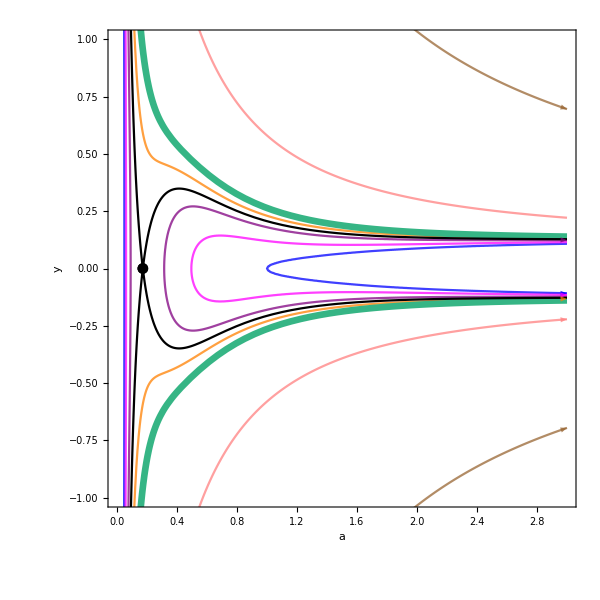

```mathematica
(*Show all components of plots*)
PhaseSpacec1ay=Show[trajc1ay,FFSc1ay,CFSc1ay,Einsteinc1ay,PlotRange->{-1,1},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc1ay=Plot[{Uay[a,0.2][[1]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
(*Plot the energy from each trajectory in the phase space*)
```

```mathematica
c1Energyay[1]=Plot[{Energyay[0.2,0][[1]]},{a,0,0.04},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c1Energyay[2]=Plot[{Energyay[0.2,0][[1]]},{a,1,3},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c1Energyay[3]=Plot[{Energyay[0.2,0.12][[1]]},{a,0,0.055},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c1Energyay[4]=Plot[{Energyay[0.2,0.12][[1]]},{a,0.5,3},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c1Energyay[5]=Plot[{Energyay[0.2,0.18][[1]]},{a,0,0.08},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c1Energyay[6]=Plot[{Energyay[0.2,0.18][[1]]},{a,0.32,3},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c1Energyay[7]=Plot[{Energyay[0.2,0.23][[1]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c1Energyay[8]=Plot[{Energyay[0.2,0.58][[1]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c1Energyay[9]=Plot[{Energyay[0.2,2.06][[1]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Brown,Dashed,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c1Energyay[10]=Plot[{0},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c1Energyay[11]=Plot[{Energyay[0.2,0][[1]]},{a,0.04,1},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c1Energyay[12]=Plot[{Energyay[0.2,0.12][[1]]},{a,0.055,0.5},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c1Energyay[13]=Plot[{Energyay[0.2,0.18][[1]]},{a,0.08,0.32},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc1ay=Table[c1Energyay[i],{i,1,13}];
```

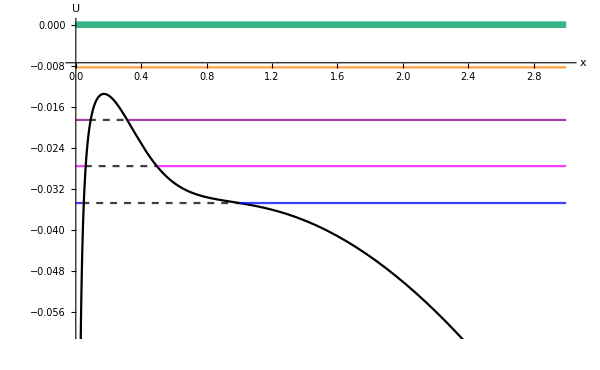

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc1ay=Show[Uc1ay,Energyc1ay,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{-0.06,0}]
```

### Final Plot

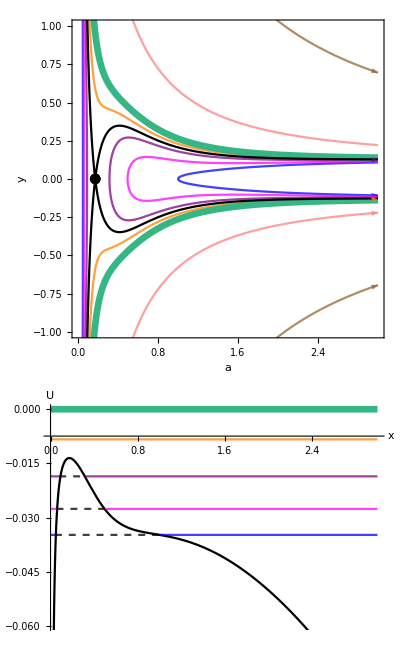

```mathematica
(*Plot the phase space and potential together*)
ayc1=GraphicsColumn[{PhaseSpacec1ay,Potentialc1ay},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\ay_Plots\\ayc1.pdf",ayc1]*)
```

## Two Einstein Points: c2

### Phase Space

```mathematica
(*Trajectories for the phase space*)
trajc2ay[y0_,x0_]:=y^2==xa[a,x0]/3+za[a,x0,c][[2]]/3+va[a,x0,cv]/3-(1/a^2)*(xa[a0,x0]/3+za[a0,x0,c][[2]]/3+va[a0,x0,cv]/3-y0^2);
```

```mathematica
c2trajay[1]=ContourPlot[Evaluate[trajc2ay[0,0.1]],{a,0,aTwoEinsteinPointsc2[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[2]=ContourPlot[Evaluate[trajc2ay[0,0.1]],{a,aTwoEinsteinPointsc2[[2]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[3]=ContourPlot[Evaluate[trajc2ay[0.07,0.1]],{a,0,aTwoEinsteinPointsc2[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[4]=ContourPlot[Evaluate[trajc2ay[0.07,0.1]],{a,aTwoEinsteinPointsc2[[1]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[5]=ContourPlot[Evaluate[trajc2ay[0.09,0.1]],{a,0,aTwoEinsteinPointsc2[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[6]=ContourPlot[Evaluate[trajc2ay[0.09,0.1]],{a,aTwoEinsteinPointsc2[[1]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[7]=ContourPlot[Evaluate[trajc2ay[0.131,0.1]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[8]=ContourPlot[Evaluate[trajc2ay[0.131,0.1]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[9]=ContourPlot[Evaluate[trajc2ay[0.44,0.1]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[10]=ContourPlot[Evaluate[trajc2ay[0.44,0.1]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[11]=ContourPlot[Evaluate[trajc2ay[1,0.1]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[12]=ContourPlot[Evaluate[trajc2ay[1,0.1]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
trajc2ay=Table[c2trajay[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc2ay=Plot[{FFSay[a,0.2][[2]],-FFSay[a,0.1][[2]]},{a,0,1.5},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc2ay=Plot[{CFSay[a,aTwoEinsteinPointsc2,0.1][[2]],-CFSay[a,aTwoEinsteinPointsc2,0.1][[2]]},{a,0,1.5},PlotStyle->{Black},PlotRange->All,PlotPoints->1000];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc2ay=ListPlot[{{aTwoEinsteinPointsc2[[1]],0},{aTwoEinsteinPointsc2[[2]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the Accna = 0 curve for this case*)
Accnc2ay=ContourPlot[Accnay[[2]]==0,{a,0,1.5},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

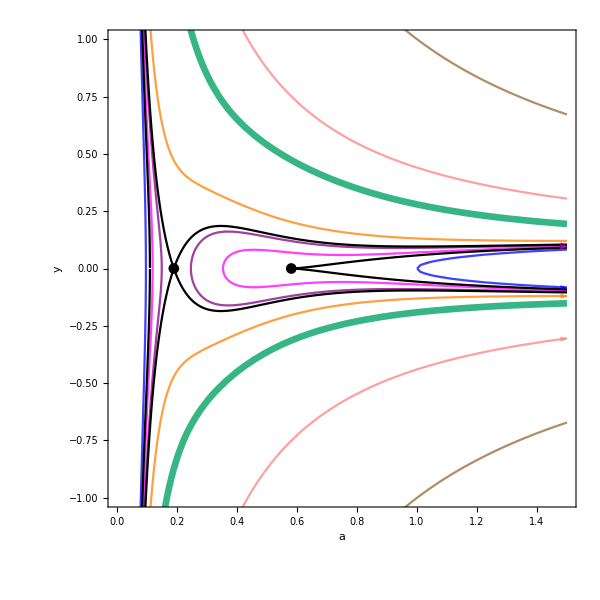

```mathematica
(*Show all components of plots*)
PhaseSpacec2ay=Show[trajc2ay,FFSc2ay,CFSc2ay,Einsteinc2ay,PlotRange->{-1,1},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc2ay=Plot[{Uay[a,0.1][[2]]},{a,0,1.5},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
c2Energyay[1]=Plot[{Energyay[0.1,0][[2]]},{a,0,0.09},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c2Energyay[2]=Plot[{Energyay[0.1,0][[2]]},{a,1,3},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c2Energyay[3]=Plot[{Energyay[0.1,0.07][[2]]},{a,0,0.12},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c2Energyay[4]=Plot[{Energyay[0.1,0.07][[2]]},{a,0.355,3},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c2Energyay[5]=Plot[{Energyay[0.1,0.09][[2]]},{a,0,0.145},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c2Energyay[6]=Plot[{Energyay[0.1,0.09][[2]]},{a,0.245,3},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c2Energyay[7]=Plot[{Energyay[0.1,0.131][[2]]},{a,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c2Energyay[8]=Plot[{Energyay[0.1,0.44][[2]]},{a,0.2,1},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c2Energyay[9]=Plot[{Energyay[0.1,1][[2]]},{a,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c2Energyay[10]=Plot[{0},{a,0.05,1},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c2Energyay[11]=Plot[{Energyay[0.1,0][[2]]},{a,0.09,1},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c2Energyay[12]=Plot[{Energyay[0.1,0.07][[2]]},{a,0.12,0.355},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c2Energyay[13]=Plot[{Energyay[0.1,0.09][[2]]},{a,0.145,0.245},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc2ay=Table[c2Energyay[i],{i,1,13}];
```

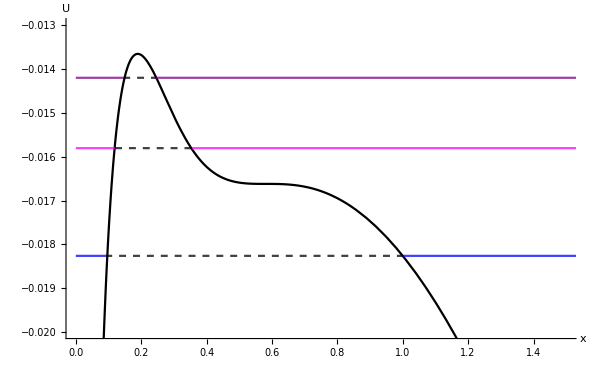

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc2ay=Show[Uc2ay,Energyc2ay,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{{0,1.5},{-0.02,-0.013}}]
```

### Final Plot

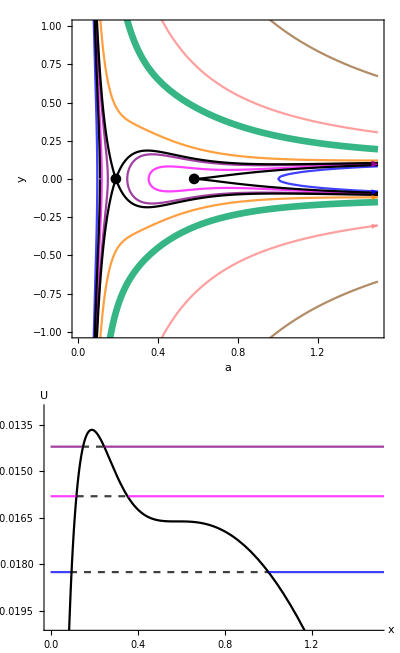

```mathematica
(*Plot the phase space and potential together*)
ayc2=GraphicsColumn[{PhaseSpacec2ay,Potentialc2ay},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\ay_Plots\\ayc2.pdf",ayc2]*)
```

## Three Einstein Points: c3

### Phase Space

```mathematica
(*Trajectories for the phase space*)
trajc3ay[y0_,x0_]:=y^2==xa[a,x0]/3+za[a,x0,c][[3]]/3+va[a,x0,cv]/3-(1/a^2)*(xa[a0,x0]/3+za[a0,x0,c][[3]]/3+va[a0,x0,cv]/3-y0^2);
```

```mathematica
c3trajay[1]=ContourPlot[Evaluate[trajc3ay[0.071,0.08]],{a,0,aThreeEinsteinPointsc3[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[2]=ContourPlot[Evaluate[trajc3ay[0.071,0.08]],{a,aThreeEinsteinPointsc3[[1]],aThreeEinsteinPointsc3[[3]]},{y,-1.5,1.5},PlotPoints->200,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[3]=ContourPlot[Evaluate[trajc3ay[0.071,0.08]],{a,aThreeEinsteinPointsc3[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[4]=ContourPlot[Evaluate[trajc3ay[0.08,0.08]],{a,0,aThreeEinsteinPointsc3[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[5]=ContourPlot[Evaluate[trajc3ay[0.08,0.08]],{a,aThreeEinsteinPointsc3[[1]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[6]=ContourPlot[Evaluate[trajc3ay[0.04,0.08]],{a,0,aThreeEinsteinPointsc3[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[7]=ContourPlot[Evaluate[trajc3ay[0.04,0.08]],{a,aThreeEinsteinPointsc3[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[8]=ContourPlot[Evaluate[trajc3ay[0.121,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[9]=ContourPlot[Evaluate[trajc3ay[0.121,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[10]=ContourPlot[Evaluate[trajc3ay[0.31,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[11]=ContourPlot[Evaluate[trajc3ay[0.31,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[12]=ContourPlot[Evaluate[trajc3ay[0.75,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[13]=ContourPlot[Evaluate[trajc3ay[0.75,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
trajc3ay=Table[c3trajay[i],{i,1,13}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc3ay=Plot[{FFSay[a,0.08][[3]],-FFSay[a,0.08][[3]]},{a,0,1.5},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc3ay=Plot[{CFSay[a,aThreeEinsteinPointsc3,0.08][[3]],-CFSay[a,aThreeEinsteinPointsc3,0.08][[3]]},{a,0,1.5},PlotStyle->{Black},PlotRange->All,PlotPoints->1000];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc3ay=ListPlot[{{aThreeEinsteinPointsc3[[1]],0},{aThreeEinsteinPointsc3[[2]],0},{aThreeEinsteinPointsc3[[3]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the Accna = 0 curve for this case*)
Accnc3ay=ContourPlot[Accna[[3]]==0,{a,0,1.5},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

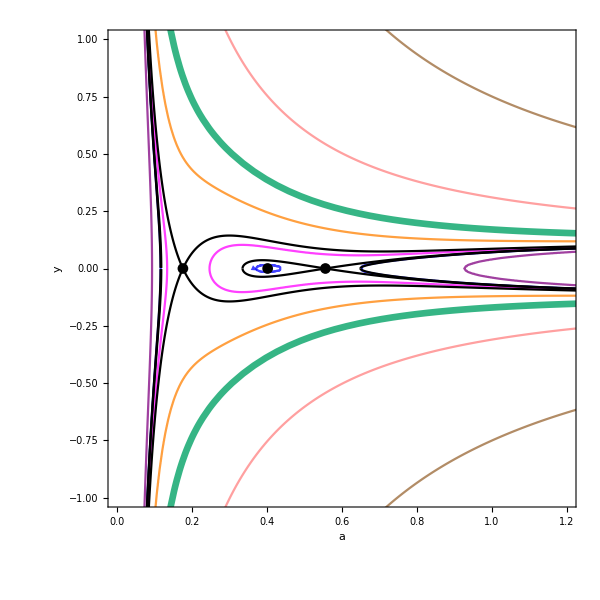

```mathematica
(*Show all components of plots*)
PhaseSpacec3ay=Show[trajc3ay,FFSc3ay,CFSc3ay,Einsteinc3ay,PlotRange->{{0,1.2},{-1,1}},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc3ay=Plot[{Uay[a,0.08][[3]]},{a,0,1.2},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
c3Energyay[1]=Plot[{Energyay[0.08,0.071][[3]]},{a,0,0.115},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c3Energyay[2]=Plot[{Energyay[0.08,0.071][[3]]},{a,0.37,0.43},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c3Energyay[3]=Plot[{Energyay[0.08,0.071][[3]]},{a,0.64,3},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c3Energyay[4]=Plot[{Energyay[0.08,0.08][[3]]},{a,0,0.13},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c3Energyay[5]=Plot[{Energyay[0.08,0.08][[3]]},{a,0.25,3},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c3Energyay[6]=Plot[{Energyay[0.08,0.04][[3]]},{a,0,0.09},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c3Energyay[7]=Plot[{Energyay[0.08,0.04][[3]]},{a,0.925,3},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c3Energyay[8]=Plot[{Energyay[0.08,0.121][[3]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c3Energyay[9]=Plot[{Energyay[0.08,0.31][[3]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c3Energyay[10]=Plot[{Energyay[0.08,0.75][[3]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c3Energyay[11]=Plot[{0},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c3Energyay[12]=Plot[{Energyay[0.08,0.071][[3]]},{a,0.115,0.37},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energyay[13]=Plot[{Energyay[0.08,0.071][[3]]},{a,0.43,0.64},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energyay[14]=Plot[{Energyay[0.08,0.08][[3]]},{a,0.13,0.25},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energyay[15]=Plot[{Energyay[0.08,0.04][[3]]},{a,0.09,0.925},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc3ay=Table[c3Energyay[i],{i,1,15}];
```

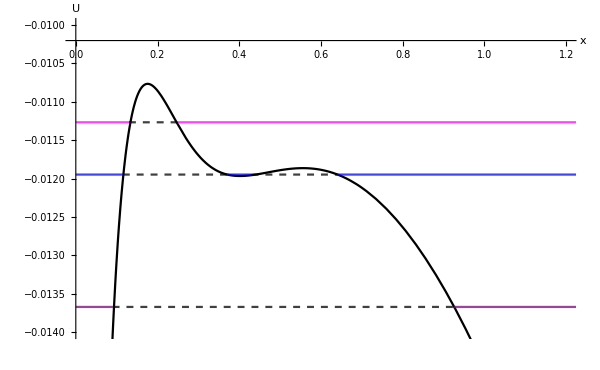

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc3ay=Show[Uc3ay,Energyc3ay,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{{0,1.2},{-0.014,-0.01}}]
```

### Final Plot

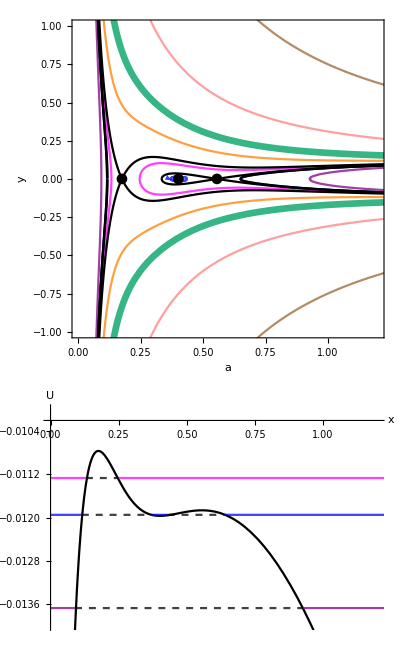

```mathematica
(*Plot the phase space and potential together*)
ayc3=GraphicsColumn[{PhaseSpacec3ay,Potentialc3ay},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\ay_Plots\\ayc3.pdf",ayc3]*)
```

## Three Einstein Points: c4

### Phase Space

```mathematica
(*Trajectories for the phase space*)
trajc4ay[y0_,x0_]:=y^2==xa[a,x0]/3+za[a,x0,c][[4]]/3+va[a,x0,cv]/3-(1/a^2)*(xa[a0,x0]/3+za[a0,x0,c][[4]]/3+va[a0,x0,cv]/3-y0^2);
```

```mathematica
c4trajay[1]=ContourPlot[Evaluate[trajc4ay[0.065,0.08]],{a,0,aThreeEinsteinPointsc4[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,.02,.02,0,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[2]=ContourPlot[Evaluate[trajc4ay[0.065,0.08]],{a,aThreeEinsteinPointsc4[[1]],aThreeEinsteinPointsc4[[3]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,.02,0,0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[3]=ContourPlot[Evaluate[trajc4ay[0.065,0.08]],{a,aThreeEinsteinPointsc4[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[4]=ContourPlot[Evaluate[trajc4ay[0.05,0.08]],{a,0,aThreeEinsteinPointsc4[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[5]=ContourPlot[Evaluate[trajc4ay[0.05,0.08]],{a,aThreeEinsteinPointsc4[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[6]=ContourPlot[Evaluate[trajc4ay[0.11,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[7]=ContourPlot[Evaluate[trajc4ay[0.11,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[8]=ContourPlot[Evaluate[trajc4ay[0.31,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[9]=ContourPlot[Evaluate[trajc4ay[0.31,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[10]=ContourPlot[Evaluate[trajc4ay[0.75,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[11]=ContourPlot[Evaluate[trajc4ay[0.75,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
trajc4ay=Table[c4trajay[i],{i,1,11}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc4ay=Plot[{FFSay[a,0.08][[4]],-FFSay[a,0.08][[4]]},{a,0,1.5},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc4ay=Plot[{CFSay[a,aThreeEinsteinPointsc4,0.08][[4]],-CFSay[a,aThreeEinsteinPointsc4,0.08][[4]]},{a,0,1.5},PlotStyle->{Black},PlotRange->All,PlotPoints->1000];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc4ay=ListPlot[{{aThreeEinsteinPointsc4[[1]],0},{aThreeEinsteinPointsc4[[2]],0},{aThreeEinsteinPointsc4[[3]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the Accna = 0 curve for this case*)
Accnc4ay=ContourPlot[Accnya[[4]]==0,{a,0,1.5},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

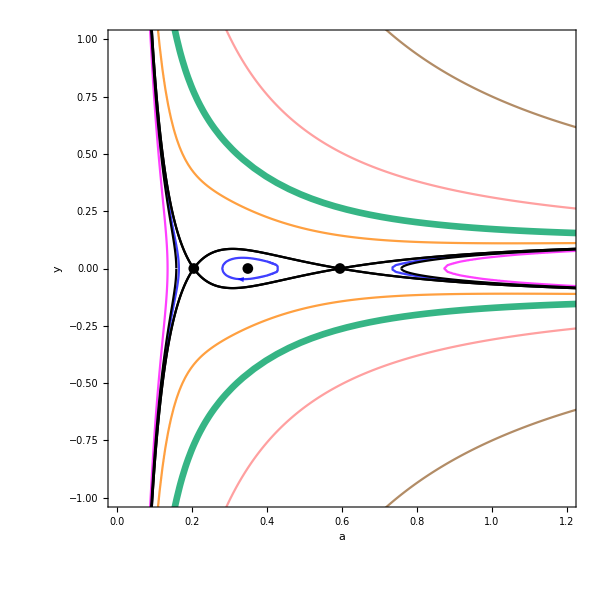

```mathematica
(*Show all components of plots*)
PhaseSpacec4ay=Show[trajc4ay,FFSc4ay,CFSc4ay,Einsteinc4ay,PlotRange->{{0,1.2},{-1,1}},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc4ay=Plot[{Uay[a,0.08][[4]]},{a,0,1.2},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
c4Energyay[1]=Plot[{Energyay[0.08,0.065][[4]]},{a,0,0.16},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c4Energyay[2]=Plot[{Energyay[0.08,0.065][[4]]},{a,0.28,0.435},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c4Energyay[3]=Plot[{Energyay[0.08,0.065][[4]]},{a,0.73,3},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c4Energyay[4]=Plot[{Energyay[0.08,0.05][[4]]},{a,0,0.135},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c4Energyay[5]=Plot[{Energyay[0.08,0.05][[4]]},{a,0.87,3},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c4Energyay[6]=Plot[{Energyay[0.08,0.11][[4]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c4Energyay[7]=Plot[{Energyay[0.08,0.31][[4]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c4Energyay[8]=Plot[{Energyay[0.08,0.75][[4]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c4Energyay[9]=Plot[{0},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c4Energyay[10]=Plot[{Energyay[0.08,0.065][[4]]},{a,0.16,0.28},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c4Energyay[11]=Plot[{Energyay[0.08,0.065][[4]]},{a,0.435,0.73},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c4Energyay[12]=Plot[{Energyay[0.08,0.05][[4]]},{a,0.135,0.87},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc4ay=Table[c4Energyay[i],{i,1,12}];
```

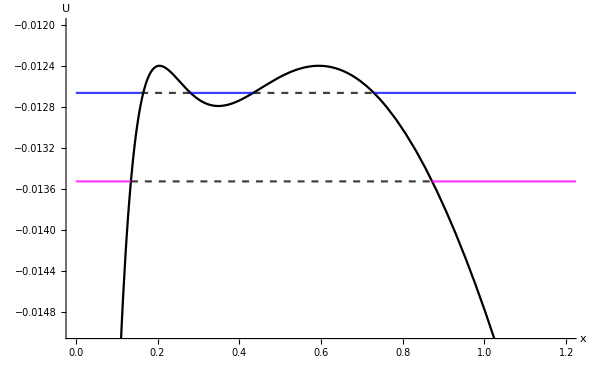

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc4ay=Show[Uc4ay,Energyc4ay,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{{0,1.2},{-0.015,-0.012}}]
```

### Final Plot

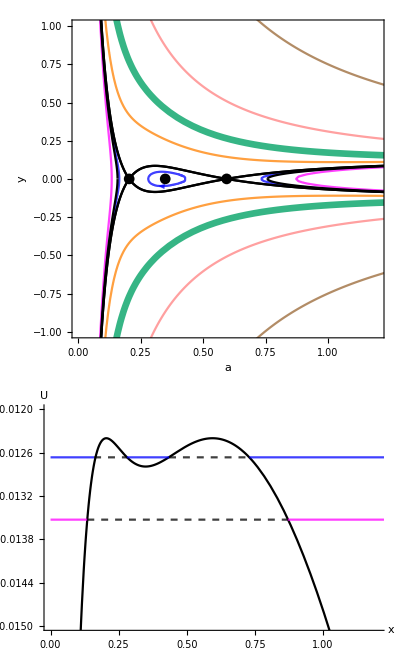

```mathematica
(*Plot the phase space and potential together*)
ayc4=GraphicsColumn[{PhaseSpacec4ay,Potentialc4ay},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\ay_Plots\\ayc4.pdf",ayc4]*)
```

## Three Einstein Points: c5

### Phase Space

```mathematica
(*Trajectories for the phase space*)
trajc5ay[y0_,x0_]:=y^2==xa[a,x0]/3+za[a,x0,c][[5]]/3+va[a,x0,cv]/3-(1/a^2)*(xa[a0,x0]/3+za[a0,x0,c][[5]]/3+va[a0,x0,cv]/3-y0^2);
```

```mathematica
c5trajay[1]=ContourPlot[Evaluate[trajc5ay[0.06,0.08]],{a,0,aThreeEinsteinPointsc5[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[2]=ContourPlot[Evaluate[trajc5ay[0.06,0.08]],{a,aThreeEinsteinPointsc5[[1]],aThreeEinsteinPointsc5[[3]]},{y,-1.5,1.5},PlotPoints->150,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[3]=ContourPlot[Evaluate[trajc5ay[0.06,0.08]],{a,aThreeEinsteinPointsc5[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[4]=ContourPlot[Evaluate[trajc5ay[0.065,0.08]],{a,0,aThreeEinsteinPointsc5[[3]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[5]=ContourPlot[Evaluate[trajc5ay[0.065,0.08]],{a,aThreeEinsteinPointsc5[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[6]=ContourPlot[Evaluate[trajc5ay[0.05,0.08]],{a,0,aThreeEinsteinPointsc5[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[7]=ContourPlot[Evaluate[trajc5ay[0.05,0.08]],{a,aThreeEinsteinPointsc5[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[8]=ContourPlot[Evaluate[trajc5ay[0.11,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[9]=ContourPlot[Evaluate[trajc5ay[0.11,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[10]=ContourPlot[Evaluate[trajc5ay[0.31,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[11]=ContourPlot[Evaluate[trajc5ay[0.31,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[12]=ContourPlot[Evaluate[trajc5ay[0.75,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[13]=ContourPlot[Evaluate[trajc5ay[0.75,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
trajc5ay=Table[c5trajay[i],{i,1,13}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc5ay=Plot[{FFSay[a,0.08][[5]],-FFSay[a,0.08][[5]]},{a,0,1.5},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc5ay=Plot[{CFSay[a,aThreeEinsteinPointsc5,0.08][[5]],-CFSay[a,aThreeEinsteinPointsc5,0.08][[5]]},{a,0,1.5},PlotStyle->{Black},PlotRange->All,PlotPoints->1000];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc5ay=ListPlot[{{aThreeEinsteinPointsc5[[1]],0},{aThreeEinsteinPointsc5[[2]],0},{aThreeEinsteinPointsc5[[3]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the Accna = 0 curve for this case*)
Accnc5ay=ContourPlot[Accnay[[5]]==0,{a,0,1.5},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

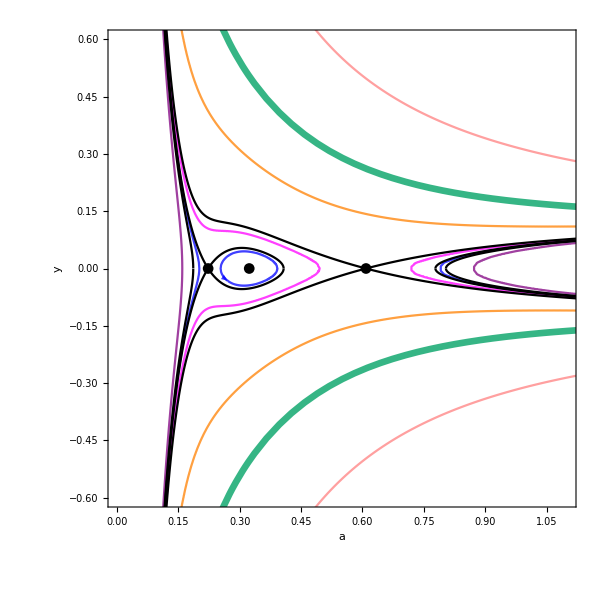

```mathematica
(*Show all components of plots*)
PhaseSpacec5ay=Show[trajc5ay,FFSc5ay,CFSc5ay,Einsteinc5ay,PlotRange->{{0,1.1},{-0.6,0.6}},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc5ay=Plot[{Uay[a,0.08][[5]]},{a,0,1.1},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
c5Energyay[1]=Plot[{Energyay[0.08,0.06][[5]]},{a,0,0.195},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c5Energyay[2]=Plot[{Energyay[0.08,0.06][[5]]},{a,0.26,0.39},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c5Energyay[3]=Plot[{Energyay[0.08,0.06][[5]]},{a,0.785,3},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c5Energyay[4]=Plot[{Energyay[0.08,0.065][[5]]},{a,0,0.495},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c5Energyay[5]=Plot[{Energyay[0.08,0.065][[5]]},{a,0.715,3},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c5Energyay[6]=Plot[{Energyay[0.08,0.05][[5]]},{a,0,0.16},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c5Energyay[7]=Plot[{Energyay[0.08,0.05][[5]]},{a,0.87,3},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c5Energyay[8]=Plot[{Energyay[0.08,0.11][[5]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c5Energyay[9]=Plot[{Energyay[0.08,0.31][[5]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c5Energyay[10]=Plot[{Energyay[0.08,0.75][[5]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c5Energyay[11]=Plot[{0},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c5Energyay[12]=Plot[{Energyay[0.08,0.06][[5]]},{a,0.195,0.26},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c5Energyay[13]=Plot[{Energyay[0.08,0.06][[5]]},{a,0.39,0.785},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c5Energyay[14]=Plot[{Energyay[0.08,0.065][[5]]},{a,0.495,0.715},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c5Energyay[15]=Plot[{Energyay[0.08,0.05][[5]]},{a,0.16,0.87},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc5ay=Table[c5Energyay[i],{i,1,15}];
```

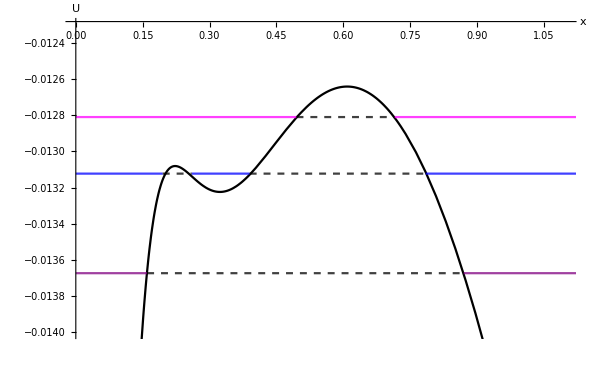

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc5ay=Show[Uc5ay,Energyc5ay,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{{0,1.1},{-0.014,-0.0123}}]
```

### Final Plot

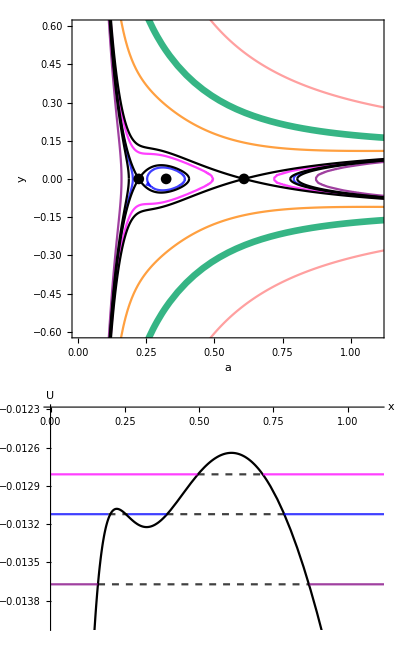

```mathematica
(*Plot the phase space and potential together*)
ayc5=GraphicsColumn[{PhaseSpacec5ay,Potentialc5ay},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\ay_Plots\\ayc5.pdf",ayc5]*)
```

## Two Einstein Points: c6

### Phase Space

```mathematica
(*Trajectories for the phase space*)
trajc6ay[y0_,x0_]:=y^2==xa[a,x0]/3+za[a,x0,c][[6]]/3+va[a,x0,cv]/3-(1/a^2)*(xa[a0,x0]/3+za[a0,x0,c][[6]]/3+va[a0,x0,cv]/3-y0^2);
```

```mathematica
c6trajay[1]=ContourPlot[Evaluate[trajc6ay[0,0.9]],{a,0,aTwoEinsteinPointsc6[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[2]=ContourPlot[Evaluate[trajc6ay[0,0.9]],{a,aTwoEinsteinPointsc6[[2]],10},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[3]=ContourPlot[Evaluate[trajc6ay[0.44,0.9]],{a,0,aTwoEinsteinPointsc6[[2]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[4]=ContourPlot[Evaluate[trajc6ay[0.44,0.9]],{a,aTwoEinsteinPointsc6[[2]],10},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[5]=ContourPlot[Evaluate[trajc6ay[0.75,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[6]=ContourPlot[Evaluate[trajc6ay[0.75,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[7]=ContourPlot[Evaluate[trajc6ay[2.06,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[8]=ContourPlot[Evaluate[trajc6ay[2.06,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[9]=ContourPlot[Evaluate[trajc6ay[7.02,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[10]=ContourPlot[Evaluate[trajc6ay[7.02,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
trajc6ay=Table[c6trajay[i],{i,1,10}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc6ay=Plot[{FFSay[a,0.9][[6]],-FFSay[a,0.9][[6]]},{a,0,10},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc6ay=Plot[{CFSay[a,aTwoEinsteinPointsc6,0.9][[6]],-CFSay[a,aTwoEinsteinPointsc6,0.9][[6]]},{a,0.1,10},PlotStyle->{Black},PlotRange->All,PlotPoints->100];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc6ay=ListPlot[{{aTwoEinsteinPointsc6[[1]],0},{aTwoEinsteinPointsc6[[2]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the Accna = 0 curve for this case*)
Accnac6ay=ContourPlot[Accnay[[6]]==0,{a,0,10},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

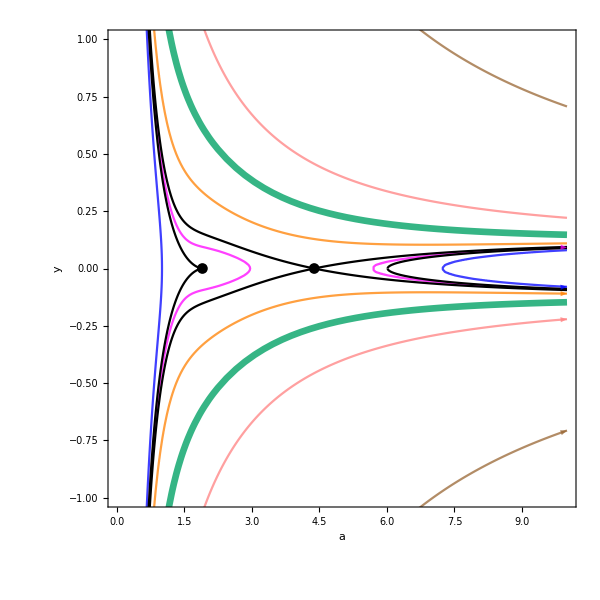

```mathematica
(*Show all components of plots*)
PhaseSpacec6ay=Show[trajc6ay,FFSc6ay,CFSc6ay,Einsteinc6ay,PlotRange->{-1,1},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc6ay=Plot[{Uay[a,0.9][[6]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
c6Energyay[1]=Plot[{Energyay[0.9,0][[6]]},{a,0,1},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c6Energyay[2]=Plot[{Energyay[0.9,0][[6]]},{a,7.2,10},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c6Energyay[3]=Plot[{Energyay[0.9,0.44][[6]]},{a,0,2.95},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c6Energyay[4]=Plot[{Energyay[0.9,0.44][[6]]},{a,5.65,10},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c6Energyay[5]=Plot[{Energyay[0.9,0.75][[6]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c6Energyay[6]=Plot[{Energyay[0.9,2.06][[6]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Pink,Dashed,Opacity[0.75]}];
```

```mathematica
c6Energyay[7]=Plot[{Energyay[0.9,7.02][[6]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c6Energyay[8]=Plot[{0},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c6Energyay[9]=Plot[{Energyay[0.9,0][[6]]},{a,1,7.2},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c6Energyay[10]=Plot[{Energyay[0.9,0.44][[6]]},{a,2.95,5.65},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc6ay=Table[c6Energyay[i],{i,1,10}];
```

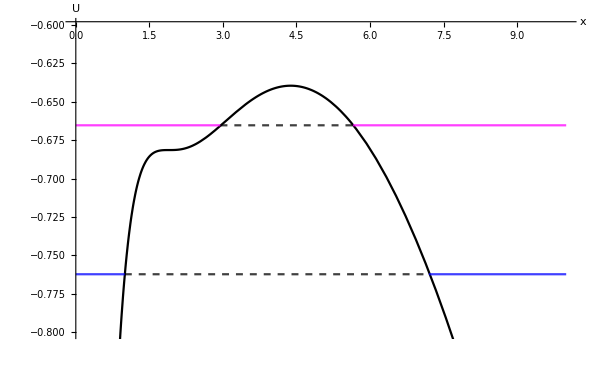

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc6ay=Show[Uc6ay,Energyc6ay,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{-0.8,-0.6}]
```

### Final Plot

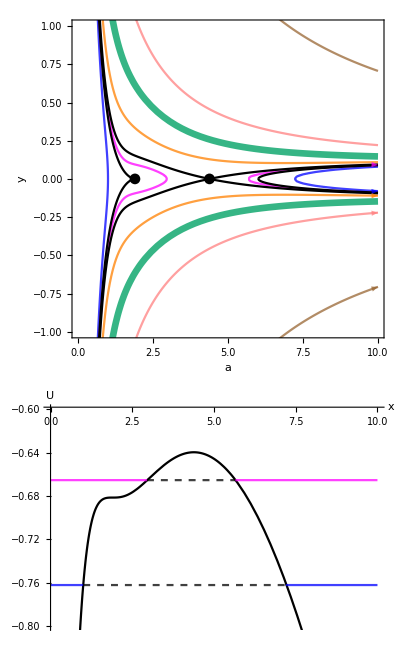

```mathematica
(*Plot the phase space and potential together*)
ayc6=GraphicsColumn[{PhaseSpacec6ay,Potentialc6ay},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\ay_Plots\\ayc6.pdf",ayc6]*)
```

## One Einstein Point: c7

### Phase Space

```mathematica
(*Trajectories for the phase space*)
trajc7ay[y0_,x0_]:=y^2==xa[a,x0]/3+za[a,x0,c][[7]]/3+va[a,x0,cv]/3-(1/a^2)*(xa[a0,x0]/3+za[a0,x0,c][[7]]/3+va[a0,x0,cv]/3-y0^2);
```

```mathematica
c7trajay[1]=ContourPlot[Evaluate[trajc7ay[0,0.9]],{a,0,aOneEinsteinPointc7},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[2]=ContourPlot[Evaluate[trajc7ay[0,0.9]],{a,aOneEinsteinPointc7,10},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[3]=ContourPlot[Evaluate[trajc7ay[0.58,0.9]],{a,0,aOneEinsteinPointc7},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[4]=ContourPlot[Evaluate[trajc7ay[0.58,0.9]],{a,aOneEinsteinPointc7,10},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[5]=ContourPlot[Evaluate[trajc7ay[0.68,0.9]],{a,0,aOneEinsteinPointc7},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[6]=ContourPlot[Evaluate[trajc7ay[0.68,0.9]],{a,aOneEinsteinPointc7,10},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[7]=ContourPlot[Evaluate[trajc7ay[0.98,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[8]=ContourPlot[Evaluate[trajc7ay[0.98,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[9]=ContourPlot[Evaluate[trajc7ay[2.35,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[10]=ContourPlot[Evaluate[trajc7ay[2.35,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[11]=ContourPlot[Evaluate[trajc7ay[7.02,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[12]=ContourPlot[Evaluate[trajc7ay[7.02,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
trajc7ay=Table[c7trajay[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc7ay=Plot[{FFSay[a,0.9][[7]],-FFSay[a,0.9][[7]]},{a,0,10},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc7ay=Plot[{CFSay[a,aOneEinsteinPointc7,0.9][[7]],-CFSay[a,aOneEinsteinPointc7,0.9][[7]]},{a,0,10},PlotStyle->{Black},PlotRange->All];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc7ay=ListPlot[{{aOneEinsteinPointc7,0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the Accna = 0 curve for this case*)
Accnc7ay=ContourPlot[Accnay[[7]]==0,{a,0,3},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

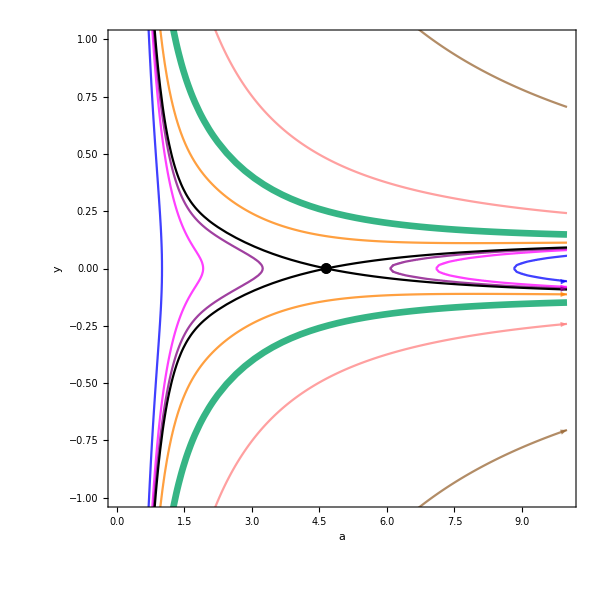

```mathematica
(*Show all components of plots*)
PhaseSpacec7ay=Show[trajc7ay,FFSc7ay,CFSc7ay,Einsteinc7ay,PlotRange->{-1,1},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc7ay=Plot[{Uay[a,0.9][[7]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
c7Energyay[1]=Plot[{Energyay[0.9,0][[7]]},{a,0,1},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c7Energyay[2]=Plot[{Energyay[0.9,0][[7]]},{a,8.8,10},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c7Energyay[3]=Plot[{Energyay[0.9,0.58][[7]]},{a,0,1.95},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c7Energyay[4]=Plot[{Energyay[0.9,0.58][[7]]},{a,7.05,10},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c7Energyay[5]=Plot[{Energyay[0.9,0.68][[7]]},{a,0,3.3},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c7Energyay[6]=Plot[{Energyay[0.9,0.68][[7]]},{a,6,10},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c7Energyay[7]=Plot[{Energyay[0.9,0.98][[7]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c7Energyay[8]=Plot[{Energyay[0.9,2.35][[7]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c7Energyay[9]=Plot[{Energyay[0.9,7.02][[7]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c7Energyay[10]=Plot[{0},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c7Energyay[11]=Plot[{Energyay[0.9,0][[7]]},{a,1,8.8},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c7Energyay[12]=Plot[{Energyay[0.9,0.58][[7]]},{a,1.95,7.05},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c7Energyay[13]=Plot[{Energyay[0.9,0.68][[7]]},{a,3.3,6},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc7ay=Table[c7Energyay[i],{i,1,13}];
```

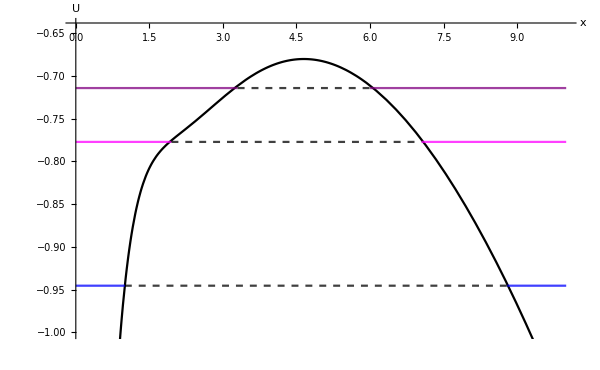

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc7ay=Show[Uc7ay,Energyc7ay,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{-1,-0.64}]
```

### Final Plot

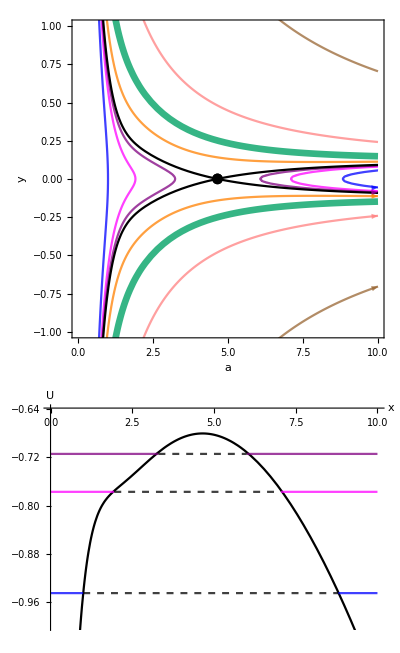

```mathematica
(*Plot the phase space and potential together*)
ayc7=GraphicsColumn[{PhaseSpacec7ay,Potentialc7ay},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\ay_Plots\\ayc7.pdf",ayc7]*)
```